# Heart Curve

### Author

Eric W. Weisstein
October 18, 2021

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneCurves/HeartCurve.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/HeartCurve.html.

©2021 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

"Pointy" heart contributed by H. Dascanio, June 21, 2003

Squished heart contributed by Pavel Kuriscak, February 12, 2006

"Greeting card" cube root card from Judith Schroeder, October 16, 2021

## All

```mathematica
eqn=(x^2+9/4y^2+z^2-1)^3-x^2z^3-9/80y^2z^3/.{y->0,z->y}
```

-x^2 y^3+(-1+x^2+y^2)^3

```mathematica
Expand[eqn]
```

-1+3 x^2-3 x^4+x^6+3 y^2-6 x^2 y^2+3 x^4 y^2-x^2 y^3-3 y^4+3 x^2 y^4+y^6

### Typesetting

```mathematica
MakeBoxes[label,TraditionalForm]:=GridBox[{{RowBox[{RowBox[{"x","==",RowBox[{"sin"," ","t"," ","cos"," ","t"," ","ln",RowBox[{"|","t","|"}]}]}]," "}]},{RowBox[{"y","==",RowBox[{SuperscriptBox[RowBox[{"|","t","|"}],"0.3"]," ",SuperscriptBox[RowBox[{"(",RowBox[{"cos"," ","t"}],")"}],RowBox[{"1","/","2"}]]}]}]}}]
```

```mathematica
MakeBoxes[label,TraditionalForm]:=GridBox[{{RowBox[{RowBox[{"x","==",RowBox[{
   RowBox[{"sin", "", "t"}], " ", 
   RowBox[{"cos", "", "t"}], " ", 
   RowBox[{"ln", "", 
    TemplateBox[{"t"},
     "Abs"]}]}]}]," "}]},{RowBox[{"y","==",RowBox[{SuperscriptBox[RowBox[{"|","t","|"}],"0.3"]," ",SuperscriptBox[RowBox[{"(",RowBox[{"cos"," ","t"}],")"}],RowBox[{"1","/","2"}]]}]}]}}]
```

### Graphics Array

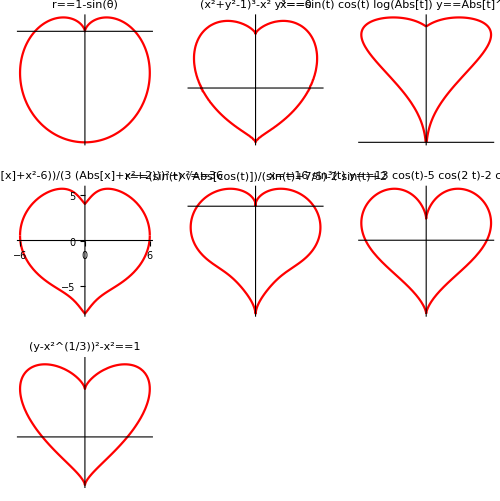

```mathematica
With[{style=Directive[9,Black,FontFamily->"Times"]},GraphicsGrid[
Partition[
{
(*0*)
PolarPlot[1-Sin[t],{t,0,2π},Ticks->None,PlotStyle->Red,
PlotLabel->r==1-Sin[θ],LabelStyle->style
],

(*1*)
ContourPlot[-x^2 y^3+(-1+x^2+y^2)^3==0,{x,-1.2,1.2},{y,-1,1.3},Frame->False,PlotLabel->-x^2 y^3+(-1+x^2+y^2)^3==0,ContourStyle->Red,Axes->True,Ticks->None,LabelStyle->style
],

(*2*)
ParametricPlot[{Log[Abs[t]]Sin[t]Cos[t],Abs[t]^.3Sqrt[Cos[t]]},{t,-1,1},
AspectRatio->Automatic,
PlotPoints->100,PlotStyle->Red,PlotRange->All,Ticks->False,PlotLabel->Column@Thread[{x,y}=={Log[Abs[t]]Sin[t]Cos[t],Abs[t]^.3Sqrt[Cos[t]]}],LabelStyle->style
],

(*3*)
Plot[2/3((x^2+Abs[x]-6)/(x^2+Abs[x]+2))+#(36-x^2)^(1/2)&/@{-1,1},{x,-6,6},PlotStyle->Red,AspectRatio->Automatic,Ticks->False,PlotLabel->(y-(2/3((x^2+Abs[x]-6)/(x^2+Abs[x]+2))))^2+x^2==36,LabelStyle->style
],

(*4*)
PolarPlot[2-2Sin[t]+Sin[t](√Abs[Cos[t]])/(Sin[t]+7/5),{t,0,2π},PlotStyle->Red,Ticks->False,PlotLabel->r==2-2Sin[t]+Sin[t](√Abs[Cos[t]])/(Sin[t]+7/5),LabelStyle->style
],

(*5*)
ParametricPlot[par={16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]},{t,-π,π},
AspectRatio->Automatic,
PlotPoints->100,PlotStyle->Red,PlotRange->All,Ticks->False,PlotLabel->TextCell[Column[Thread[{x,y}=={16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]}],Alignment->Left],PageWidth->500/3],LabelStyle->style
],

(*6*)

ContourPlot[x^2+(y-(x^2)^(1/3))^2==1,{x,-1,1},{y,-1,1.6},Frame->False,PlotLabel->-x^2+(y-(x^2)^(1/3))^2==1,ContourStyle->Red,Axes->True,Ticks->None,LabelStyle->style]
},UpTo[3]],ImageSize->500,Alignment->Center]]
```

## Cardioid

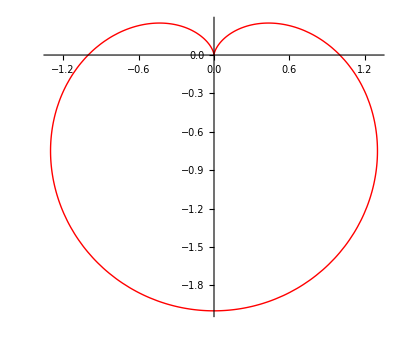

```mathematica
PolarPlot[1-Sin[θ],{θ,0,2π},PlotStyle->Red]
```

```mathematica
Area[1-Sin[θ],{θ,0,2π}]
```

(3 π)/2

## HeartCurve1

```mathematica
eqn=(x^2+y^2-a^2)^3==a x^2 y^3;
```

```mathematica
Expand[Subtract@@eqn]
```

-a^6+3 a^4 x^2-3 a^2 x^4+x^6+3 a^4 y^2-6 a^2 x^2 y^2+3 x^4 y^2-a x^2 y^3-3 a^2 y^4+3 x^2 y^4+y^6

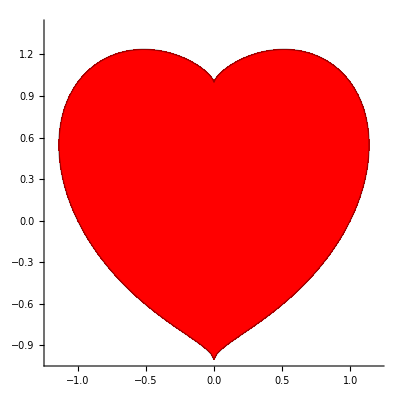

```mathematica
RegionPlot[-x^2 y^3+(-1+x^2+y^2)^3<0,{x,-1.2,1.2},{y,-1,1.4},Frame->False,Axes->True,PlotStyle->Red]
```

```mathematica
FullSimplify[-x^2 y^3+(-1+x^2+y^2)^3/.{x->r Cos[t],y->r Sin[t]}]
```

(-1+r^2)^3-r^5 Cos[t]^2 Sin[t]^3

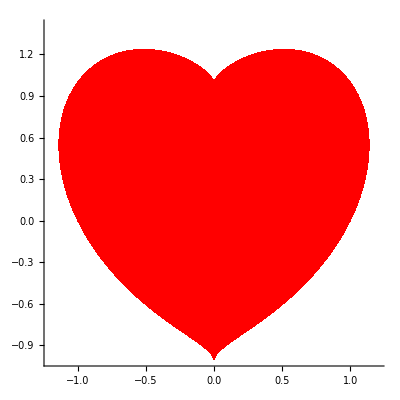

```mathematica
With[{a=1},RegionPlot[(x^2+y^2-a^2)^3<a x^2 y^3,{x,-1.2,1.2},{y,-1,1.4},Frame->False,Axes->True,PlotStyle->Red,BoundaryStyle->None]]
```

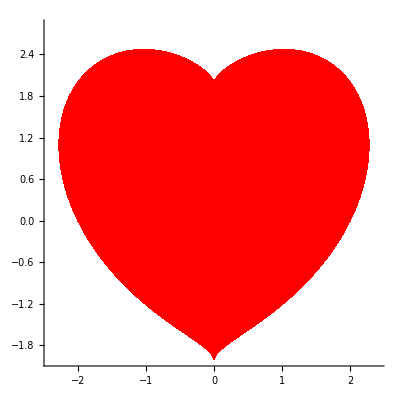

```mathematica
With[{a=2},RegionPlot[(x^2+y^2-a^2)^3<a x^2 y^3,{x,-1.2 2,1.2 2},{y,-1 2,1.4 2},Frame->False,Axes->True,PlotStyle->Red,BoundaryStyle->None]]
```

### Area

```mathematica
Integrate[Boole[(x^2+y^2-1)^3<x^2 y^3],{x,-∞,∞},{y,-∞,∞}]
```

∫_-1^0 (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx+∫_0^1 (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx+∫_1^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx+∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^-1 (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx

```mathematica
Integrate[Boole[(x^2+y^2-1)^3<x^2 y^3],{y,-∞,∞},{x,-∞,∞}]
```

$Aborted

```mathematica
N[%]//Chop
```

3.66197

```mathematica
NIntegrate[Boole[-x^2 y^3+(-1+x^2+y^2)^3<0],{x,-∞,∞},{y,-∞,∞}]
```

3.66197

```mathematica
Integrate[Boole[-x^2 y^3+(-1+x^2+y^2)^3<0],{x,0,∞},{y,-∞,∞}]
```

∫_0^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx

```mathematica
2NIntegrate[Boole[-x^2 y^3+(-1+x^2+y^2)^3<0],{x,0,∞},{y,-∞,∞}]
```

3.66197

```mathematica
2NIntegrate[Boole[-x^2 y^3+(-1+x^2+y^2)^3<0],{x,0,∞},{y,-∞,∞},WorkingPrecision->20]
```

3.6619727258184536655

```mathematica
Maximize[{#,-x^2 y^3+(-1+x^2+y^2)^3==0},{x,y}]&/@{x,y}
```

{{-Root[-64+192 #1^2-193 #1^4+64 #1^6&,1],{x→-Root[-64+192 #1^2-193 #1^4+64 #1^6&,1],y→Root[-1-#1^2+8 #1^3&,1]}},{-Root[27-54 #1^2+4 #1^3+27 #1^4&,1],{x→Root[-1-6 #1^2-12 #1^4-8 #1^6+729 #1^8&,1],y→-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]}}}

```mathematica
N[%]
```

{{1.13903,{x→1.13903,y→0.54533}},{1.23666,{x→-0.514454,y→1.23666}}}

```mathematica
ImplicitPlot[-x^2 z^3+(-1+x^2+z^2)^3==0,{x,-2,2},PlotRange->All,PlotStyle->Red,
PlotLabel->TraditionalForm[-x^2 y^3+(-1+x^2+y^2)^3==0]
]
```

⁃Graphics⁃

```mathematica
Solve[-x2 y^3+(-1+x2+y^2)^3==0,x2]
```

{{x2→1-y^2+((2/3)^(1/3) y^3)/((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))+((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2^(1/3) 3^(2/3))},{x2→1-y^2-((1+ⅈ √3) y^3)/(2^(2/3) 3^(1/3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))-((1-ⅈ √3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2 2^(1/3) 3^(2/3))},{x2→1-y^2-((1-ⅈ √3) y^3)/(2^(2/3) 3^(1/3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))-((1+ⅈ √3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
Plot[1-y^2+((2/3)^(1/3) y^3)/((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))+((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2^(1/3) 3^(2/3)),{y,-1,1.2366}]
```

⁃Graphics⁃

```mathematica
Plot[1-y^2-((1-ⅈ √3) y^3)/(2^(2/3) 3^(1/3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))-((1+ⅈ √3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2 2^(1/3) 3^(2/3)),{y,1.001,1.236}]
```

Plot::plnr: 1 - y^2 - (1 - ⅈ\ √3)\ y^3/2^2 « 1 » « 5 » « 1 » « 1 »]\ 3^« 1 »\ « 1 » - (1 + ⅈ\ √3)\ (9\ y^3 - 9\ « 1 » + √3\ « 1 »)^1/3/2\ 2^1\ Power[« 2 »]\ 3^2\ Power[« 2 »] is not a machine-size real number at y = 1.001. More…

Plot::plnr: 1 - y^2 - (1 - ⅈ\ √3)\ y^3/2^2 « 1 » « 5 » « 1 » « 1 »]\ 3^« 1 »\ « 1 » - (1 + ⅈ\ √3)\ (9\ y^3 - 9\ « 1 » + √3\ « 1 »)^1/3/2\ 2^1\ Power[« 2 »]\ 3^2\ Power[« 2 »] is not a machine-size real number at y = 1.00564. More…

Plot::plnr: 1 - y^2 - (1 - ⅈ\ √3)\ y^3/2^2 « 1 » « 5 » « 1 » « 1 »]\ 3^« 1 »\ « 1 » - (1 + ⅈ\ √3)\ (9\ y^3 - 9\ « 1 » + √3\ « 1 »)^1/3/2\ 2^1\ Power[« 2 »]\ 3^2\ Power[« 2 »] is not a machine-size real number at y = 1.00622. More…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. More…

⁃Graphics⁃

```mathematica
-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]//N
```

1.23666

```mathematica
2(NIntegrate[√(1-y^2+((2/3)^(1/3) y^3)/((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))+((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2^(1/3) 3^(2/3))),{y,-1,-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]}]-NIntegrate[√(1-y^2-((1-ⅈ √3) y^3)/(2^(2/3) 3^(1/3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))-((1+ⅈ √3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2 2^(1/3) 3^(2/3))),{y,1,-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]}])//Chop
```

3.66197

```mathematica
(a=2(Integrate[√(1-y^2+((2/3)^(1/3) y^3)/((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))+((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2^(1/3) 3^(2/3))),{y,-1,-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]}]-Integrate[√(1-y^2-((1-ⅈ √3) y^3)/(2^(2/3) 3^(1/3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))-((1+ⅈ √3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2 2^(1/3) 3^(2/3))),{y,1,-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]}]))//Timing
```

{835.028 Second,2 (∫_-1^(-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]) √(1-y^2+((2/3)^(1/3) y^3)/((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))+((9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2^(1/3) 3^(2/3)))ⅆy-∫_1^(-Root[27-54 #1^2+4 #1^3+27 #1^4&,1]) √(1-y^2-((1-ⅈ √3) y^3)/(2^(2/3) 3^(1/3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))-((1+ⅈ √3) (9 y^3-9 y^5+√3 √(27 y^6-54 y^8-4 y^9+27 y^10))^(1/3))/(2 2^(1/3) 3^(2/3)))ⅆy)}

### AreaInertiaTensor

```mathematica
AreaInertiaTensor[-x^2 y^3+(-1+x^2+y^2)^3<0,{x,y}]
```

{{∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] 1/3 (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]^3+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2]^3)ⅆx,∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] 1/2 x (Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]^2-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2]^2)ⅆx},{∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] 1/2 x (Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]^2-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2]^2)ⅆx,∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] x^2 (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx}}

```mathematica
N[%]//Chop
```

{{1.32996,0},{0,1.20243}}

```mathematica
AreaInertiaTensor[-x^2 y^3+(-1+x^2+y^2)^3<0,{y,x}]
```

{{∫_-1^1 1/3 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^3+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^3)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/3 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^3+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^3)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/3 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,3]^3+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,4]^3)ⅆy,∫_-1^1 1/2 y (Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^2-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^2)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/2 y (Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^2-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^2)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/2 y (Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,3]^2-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,4]^2)ⅆy},{∫_-1^1 1/2 y (Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^2-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^2)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/2 y (Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^2-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^2)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/2 y (Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,3]^2-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,4]^2)ⅆy,∫_-1^1 y^2 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2])ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] y^2 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2])ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] y^2 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,3]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,4])ⅆy}}

```mathematica
N[%]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00387517}. NIntegrate obtained 3.04919×10^-16 and 2.89247×10^-16 for the integral and error estimates.

{{1.20243,0},{0,1.32996}}

### Centroid

```mathematica
Centroid[-x^2 y^3+(-1+x^2+y^2)^3<0,{x,y}]
```

{∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] x (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2])ⅆx,∫_Root[-64+192 #1^2-193 #1^4+64 #1^6&,1]^Root[-64+192 #1^2-193 #1^4+64 #1^6&,2] 1/2 (-Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]^2+Root[-1+3 x^2-3 x^4+x^6+(3-6 x^2+3 x^4) #1^2-x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2]^2)ⅆx}

```mathematica
N[%]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00441392}. NIntegrate obtained 0.  + 0.\ ⅈ and 5.39248×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0,1.07472}

```mathematica
Centroid[-x^2 y^3+(-1+x^2+y^2)^3<0,{y,x}]
```

{∫_-1^1 y (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2])ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] y (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2])ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] y (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,3]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,4])ⅆy,∫_-1^1 1/2 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^2+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^2)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/2 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,1]^2+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,2]^2)ⅆy+∫_1^Root[27-54 #1^2-4 #1^3+27 #1^4&,2] 1/2 (-Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,3]^2+Root[-1+3 y^2-3 y^4+y^6+(3-6 y^2-y^3+3 y^4) #1^2+(-3+3 y^2) #1^4+#1^6&,4]^2)ⅆy}

```mathematica
N[%]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00387517}. NIntegrate obtained -5.93377×10^-12 and 6.17829×10^-12 for the integral and error estimates.

{1.07472,0}

### Curvature

```mathematica
SortBy[FullSimplify[Curvature[eqn,{x,y}],(x|y)∈Reals&&a>0],ByteCount]
```

{-((6 a^2 y^4 (3 a^4 (a^2-x^2)^2+2 a^2 (-2 a^4+a^2 x^2-17 x^4) y^2+a x^2 (3 a^2-2 x^2) y^3-3 (2 a^4-6 a^2 x^2+3 x^4) y^4+5 a x^2 y^5+2 (6 a^2-7 x^2) y^6-5 y^8))/(a y^3 (-24 a^6+12 a^2 (x^2-6 y^2) (x^2+y^2)+24 y^2 (x^2+y^2)^2+12 a^4 (x^2+6 y^2)+a (9 x^4 y-20 x^2 y^3)))^(3/2)),(9 y^2 (a x^2 y-2 (-a^2+x^2+y^2)^2)^2 (-2 a y^3+24 x^2 (-a^2+x^2+y^2)+6 (-a^2+x^2+y^2)^2)+6 (-a x^2 y+4 y^2 (-a^2+x^2+y^2)+(-a^2+x^2+y^2)^2) (2 a x y^3-6 x (-a^2+x^2+y^2)^2)^2-12 x y (-4 a^2-a y+4 (x^2+y^2)) (-2 a x y^3+6 x (-a^2+x^2+y^2)^2) (-3 a x^2 y^2+6 y (-a^2+x^2+y^2)^2))/((2 a x y^3-6 x (-a^2+x^2+y^2)^2)^2+(3 a x^2 y^2-6 y (-a^2+x^2+y^2)^2)^2)^(3/2),(6 a ((a^2-x^2)^3 (4 a^4+25 a^2 x^2+7 x^4)+a x^2 (a^2-x^2)^3 y-6 (a^2-x^2)^2 (2 a^4+13 a^2 x^2+3 x^4) y^2+a x^2 (a^4+31 a^2 x^2+4 x^4) y^3+(8 a^6+81 a^4 x^2-77 a^2 x^4-11 x^6) y^4+3 a x^2 (a^2-2 x^2) y^5))/((4 a (a^2-x^2)^3-24 (a^2-x^2)^3 y-12 a (a^2-x^2)^2 y^2+4 (3 a^4-14 a^2 x^2+12 x^4) y^3+3 a (4 a^2-9 x^2) y^4+12 (a^2+2 x^2) y^5) √(a y^3 (-24 a^6+12 a^2 (x^2-6 y^2) (x^2+y^2)+24 y^2 (x^2+y^2)^2+12 a^4 (x^2+6 y^2)+a (9 x^4 y-20 x^2 y^3))))}

```mathematica
ByteCount/@%
```

{6216,8280,10504}

### Inflection Points

```mathematica
infl=InflectionPoints[eqn,{x,y}]
```

{{-√Root[-4096-73728 #1-1030784 #1^2-975360 #1^3+2167120771 #1^4+32956054 #1^5-9794748 #1^6+1308296 #1^7-92435 #1^8+4096 #1^9&,3],Root[46629+11664 #1-92556 #1^2-11644 #1^3+46026 #1^4+7336 #1^5+316 #1^6-1004 #1^7-31 #1^8+64 #1^9&,3]},{√Root[-4096-73728 #1-1030784 #1^2-975360 #1^3+2167120771 #1^4+32956054 #1^5-9794748 #1^6+1308296 #1^7-92435 #1^8+4096 #1^9&,3],Root[46629+11664 #1-92556 #1^2-11644 #1^3+46026 #1^4+7336 #1^5+316 #1^6-1004 #1^7-31 #1^8+64 #1^9&,3]}}

### Singular Points

```mathematica
pts=Union[SingularPoints[eqn,{x,y}]]
```

{{-1,0},{0,-1},{0,1},{1,0}}

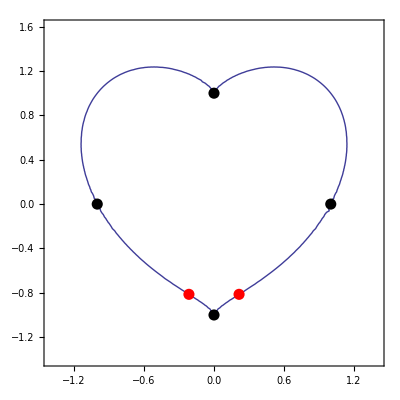

```mathematica
ContourPlot[eqn==0,{x,-1.4,1.4},{y,-1.4,1.6},Epilog->{PointSize[.02],Point[pts],Red,Point[infl]}]
```

### Slope

```mathematica
SortBy[FullSimplify[Slope[eqn,{x,y}],a>0],ByteCount]
```

{-(-2 a x y^3+6 x (-a^2+x^2+y^2)^2)/(-3 a x^2 y^2+6 y (-a^2+x^2+y^2)^2),-x/y+(a (-3 x^3+2 x y^2))/(6 a^4-3 a x^2 y-12 a^2 (x^2+y^2)+6 (x^2+y^2)^2)}

```mathematica
ByteCount/@%
```

{1664,1768}

## HeartCurve2

### Equation

```mathematica
par[t_]:=a{Sin[t]Cos[t]Log[Abs[t]],Sqrt[t^2]^(3/10)√Cos[t]}
```

```mathematica
Solve[And@@Thread[{x,y}==par[t]],{x,y},t]
```

{{}}

```mathematica
FullSimplify[par[t]^2,0<t<1]
```

{Cos[t]^2 Log[t]^2 Sin[t]^2,t^(3/5) Cos[t]}

```mathematica
Eliminate[{x^2==Cos[t]^2 Log[t]^2 Sin[t]^2,y^2==t^(3/5) Cos[t]},t]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

t^3 Cos[t]==(t^2)^(3/2) Cos[t]&&Cos[t]^2 (-1+Cos[t]^2) Log[t]^2==Cos[t]^2 (-1+Cos[t]^2) Log[√(t^2)]^2

```mathematica
Solve[x^2==Cos[t]^2 Log[t]^2 Sin[t]^2&&-1<t<1,t]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
Solve[y^2==t^(3/5) Cos[t]&&-1<t<1,t]
```

$Aborted

### Plot

```mathematica
Limit[par[t],t->1]
```

{0,√Cos[1]}

```mathematica
Limit[par[t],t->0]
```

{0,0}

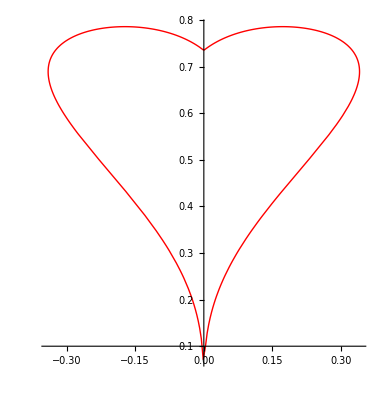

```mathematica
ParametricPlot[par[t],{t,-1,1},PlotStyle->Red,PlotRange->All]
```

```mathematica
curve={Sin[t]Cos[t]Log[Abs[t]],Sqrt[t^2]^(3/10)√Cos[t]};
```

```mathematica
plot=ParametricPlot[par[t],{t,-1,1},PlotStyle->Red,PlotRange->All];
```

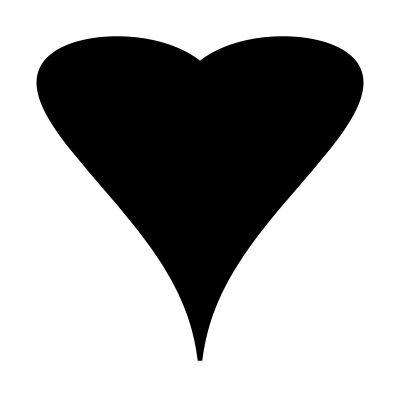

```mathematica
Graphics[Polygon[Flatten[Cases[plot,Line[x_]:>x,∞],1]]]
```

### Top part

```mathematica
Plot[Sin[t]Cos[t]Log[Abs[t]],{t,-1,1}]
```

-Graphics-

```mathematica
Minimize[{Sin[t]Cos[t]Log[Abs[t]],Abs[t]<1},t]//FullSimplify
```

{1/2 Log[Root[{Sin[2 #1]+2 Cos[2 #1] Log[#1] #1&,0.31450905197322821290713}]] Sin[2 Root[{Sin[2 #1]+2 Cos[2 #1] Log[#1] #1&,0.31450905197322821290713}]],{t→Root[{Sin[2 #1]+2 Cos[2 #1] Log[#1] #1&,0.31450905197322821290713}]}}

```mathematica
N[%]
```

{-0.340285,{t→0.314509}}

```mathematica
N[t0=Root[{Sin[2 #1]+2 Cos[2 #1] Log[#1] #1&,0.31450905197322821290712809469216814072`23.6}]]
```

0.314509

```mathematica
N[x0=-1/2 Log[t0]Sin[2t0]]
```

0.340285

```mathematica
N[y0=Sqrt[t0^2]^(3/10)√Cos[t0]]
```

0.689237

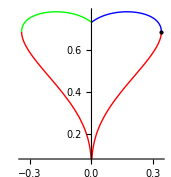

```mathematica
Show[{
ParametricPlot[par[t],{t,-t0,t0},PlotStyle->Red,PlotRange->All],
ParametricPlot[par[t],{t,-1,-t0},PlotStyle->Blue,PlotRange->All],
ParametricPlot[par[t],{t,t0,1},PlotStyle->Green,PlotRange->All],
Graphics[Point[{x0,y0}]]
}]
```

```mathematica
bot=ParametricPlot[par[t],{t,-t0,t0},PlotRange->All];
```

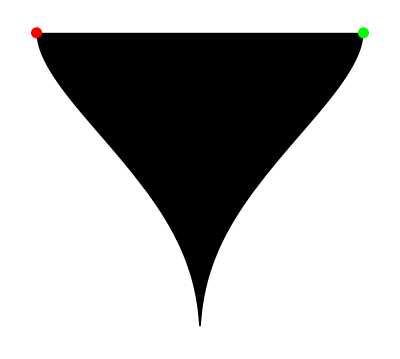

```mathematica
Graphics[{
Polygon[Join@@Cases[bot,Line[x_]:>x,∞]],
PointSize[.02],
Green,Point[par[-t0]],
Red,Point[par[t0]]
}
]
```

```mathematica
left=ParametricPlot[par[t],{t,t0,1},PlotRange->All];
```

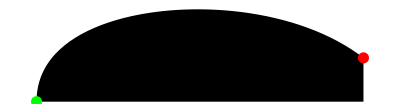

```mathematica
Graphics[{
Polygon[Prepend[Cases[left,Line[x_]:>x,∞][[1]],{0,y0}]],
PointSize[.02],
Green,Point[par[t0]],
Red,Point[par[1]]
}]
```

```mathematica
right=ParametricPlot[par[t],{t,-t0,-1},PlotRange->All];
```

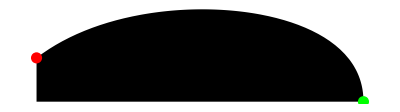

```mathematica
Graphics[{
Polygon[Prepend[Cases[right,Line[x_]:>x,∞][[1]],{0,y0}]],
PointSize[.02],
Green,Point[par[-t0]],
Red,Point[par[-1]]
}]
```

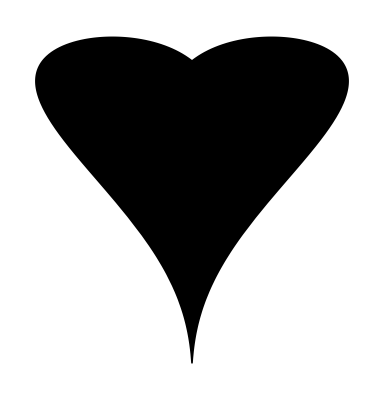

```mathematica
Graphics[{Polygon[poly=Join[
Join@@Cases[right,Line[x_]:>x,∞],
Join@@Cases[bot,Line[x_]:>x,∞],
Join@@Cases[left,Line[x_]:>x,∞]
]]}]
```

```mathematica
Graphics[Polygon[poly=Join@@((Join@@Cases[#,Line[x_]:>x,∞])&/@{right,bot,left})]]
```

-Graphics-

```mathematica
Graphics[Polygon[Flatten[Cases[#,Line[x_]:>x,∞]&/@{right,bot,left},2]]]
```

-Graphics-

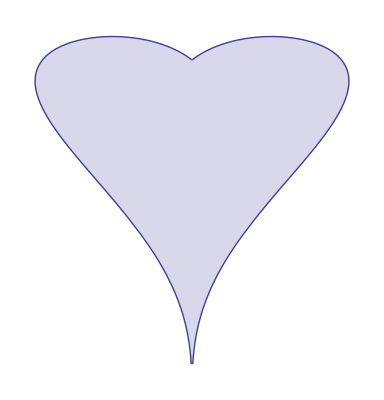

```mathematica
Graphics[{EdgeForm[$plotstyle[[1]]],FaceForm[Directive[Hue[0.67,0.6,0.6],Opacity[0.2]]],Polygon[Flatten[Cases[#,Line[x_]:>x,∞]&/@{right,bot,left},2]]}]
```

### Arc Length

```mathematica
ArcLength[par[t]/.Abs[t]:>Sqrt[t^2],{t,-1,1}]//Timing
```

{3987.79,∫_-1^1 √(((3 t √Cos[t])/(10 (t^2)^(17/20))-((t^2)^(3/20) Sin[t])/(2 √Cos[t]))^2+(Cos[t]^2 Log[√(t^2)]+(Cos[t] Sin[t])/t-Log[√(t^2)] Sin[t]^2)^2)ⅆt}

### Arc Length Function

```mathematica
ArcLength[par[t]/.Abs[t]:>Sqrt[t^2],t]//Timing
```

$Aborted

### Area

#### Parametric

```mathematica
Area[curve,{t,-1,1}]//Timing
```

{1788.5261,-∫_-1^1 (t^2)^(3/20) √Cos[t] (Cos[t]^2 Log[Abs[t]]-Log[Abs[t]] Sin[t]^2+(Cos[t] Sin[t] Abs'[t])/Abs[t])ⅆt}

```mathematica
area[{f_,g_},{t_,t0_,t1_},assum___?OptionQ]:=integrate[f D[g,t]-g D[f,t],{t,t0,t1},assum]/2
```

```mathematica
FullSimplify[area[{Sin[t]Cos[t]Log[Sqrt[t^2]],Sqrt[t^2]^(3/10)√Cos[t]},{t,-1,1}],-1<t<1]
```

1/2 integrate[(t √Cos[t] (-5 t (1+3 Cos[2 t]) Log[t^2]+(-20+Log[t^6]) Sin[2 t]))/(40 Abs[t]^(17/10)),{t,-1,1}]

```mathematica
1/2 NIntegrate[(t √Cos[t] (-5 t (1+3 Cos[2 t]) Log[t^2]+(-20+Log[t^6]) Sin[2 t]))/(40 Abs[t]^(17/10)),{t,-1,1}]
```

-0.237154

```mathematica
Area[{Sin[t]Cos[t]Log[Sqrt[t^2]],Sqrt[t^2]^(3/10)√Cos[t]},{t,-1,1}]//Timing
```

{103.99 Second,1/2 ∫_-1^1 (Cos[t] Log[√(t^2)] Sin[t] ((3 t √Cos[t])/(10 (t^2)^(17/20))-((t^2)^(3/20) Sin[t])/(2 √Cos[t]))-(t^2)^(3/20) √Cos[t] (Cos[t]^2 Log[√(t^2)]+(Cos[t] Sin[t])/t-Log[√(t^2)] Sin[t]^2))ⅆt}

```mathematica
Last[%]/.Integrate:>NIntegrate
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, highly oscillatory integrand, or insufficient WorkingPrecision.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in t near {t} = {0.00193758}. NIntegrate obtained -0.474307 and 5.30265×10^-6 for the integral and error estimates.

-0.237154

#### Numeric

```mathematica
-1/2 NIntegrate[(t √Cos[t] (-5 t (1+3 Cos[2 t]) Log[t^2]+(-20+Log[t^6]) Sin[2 t]))/(40 Abs[t]^(17/10)),{t,-1,1},WorkingPrecision->20]
```

0.23715384547599173447

### AreaMomentOfInertia

### Centroid

### Curvature

```mathematica
Curvature[par[t]/.Abs[c_]:>Sqrt[c^2],t]
```

(-((3 a t √Cos[t])/(10 (t^2)^(17/20))-(a (t^2)^(3/20) Sin[t])/(2 √Cos[t])) ((2 a Cos[t]^2)/t-(a Cos[t] Sin[t])/t^2-4 a Cos[t] Log[√(t^2)] Sin[t]-(2 a Sin[t]^2)/t)+(-(51 a t^2 √Cos[t])/(100 (t^2)^(37/20))+(3 a √Cos[t])/(10 (t^2)^(17/20))-1/2 a (t^2)^(3/20) √Cos[t]-(3 a t Sin[t])/(10 (t^2)^(17/20) √Cos[t])-(a (t^2)^(3/20) Sin[t]^2)/(4 Cos[t]^(3/2))) (a Cos[t]^2 Log[√(t^2)]+(a Cos[t] Sin[t])/t-a Log[√(t^2)] Sin[t]^2))/(((3 a t √Cos[t])/(10 (t^2)^(17/20))-(a (t^2)^(3/20) Sin[t])/(2 √Cos[t]))^2+(a Cos[t]^2 Log[√(t^2)]+(a Cos[t] Sin[t])/t-a Log[√(t^2)] Sin[t]^2)^2)^(3/2)

```mathematica
Simplify[%,-1<t<1&&a>0]
```

-((5 t (4 t Cos[t]^4 (120+(21+50 t^2) Log[t^2])-8 Cos[t]^3 (9+50 t^2+45 t^2 Log[t^2]) Sin[t]-40 t^2 Cos[t] (-25+3 Log[t^2]) Sin[t]^3-100 t^3 Log[t^2] Sin[t]^4+t (40+7 (-3+25 t^2) Log[t^2]) Sin[2 t]^2))/(4 a Abs[t]^(7/10) (25 Abs[t]^(13/5) Sin[t]^2+3 Abs[t]^(3/5) Cos[t] (3 Cos[t]-10 t Sin[t])+25 Cos[t] (t Cos[2 t] Log[t^2]+Sin[2 t])^2)^(3/2)))

```mathematica
FullSimplify[%,-1<t<1&&a>0]
```

(5 t (-200 t+18 Sin[2 t]+9 Sin[4 t]+t (-(21+125 t^2) Log[t^2]+Cos[4 t] (-40+3 (-7+25 t^2) Log[t^2])-6 Cos[2 t] (40+(7+25 t^2) Log[t^2])+6 t (-25+Log[t^40]) Sin[2 t]+t (175+Log[t^60]) Sin[4 t])))/(4 a Abs[t]^(7/10) (25 Abs[t]^(13/5) Sin[t]^2+3 Abs[t]^(3/5) Cos[t] (3 Cos[t]-10 t Sin[t])+25 Cos[t] (t Cos[2 t] Log[t^2]+Sin[2 t])^2)^(3/2))

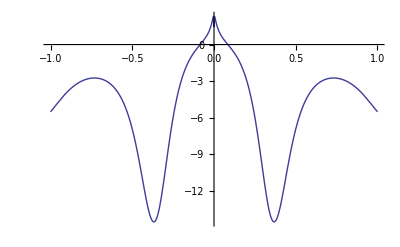

```mathematica
Plot[κ,{t,-1,1}]
```

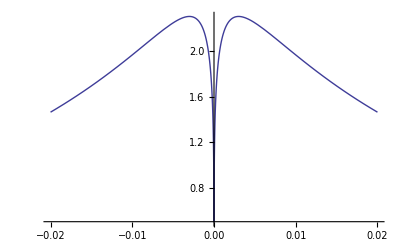

```mathematica
Plot[κ,{t,-.02,.02}]
```

### Inflection Points

```mathematica
Numerator[κ]
```

-5 Abs[t]^(13/10) (4 t Cos[t]^4 (120+(21+50 t^2) Log[t^2])-8 Cos[t]^3 (9+50 t^2+45 t^2 Log[t^2]) Sin[t]-40 t^2 Cos[t] (-25+3 Log[t^2]) Sin[t]^3-100 t^3 Log[t^2] Sin[t]^4+t (40+7 (-3+25 t^2) Log[t^2]) Sin[2 t]^2)

```mathematica
expr=-5 Abs[t]^(13/10) (4 t Cos[t]^4 (120+(21+50 t^2) Log[t^2])-8 Cos[t]^3 (9+50 t^2+45 t^2 Log[t^2]) Sin[t]-40 t^2 Cos[t] (-25+3 Log[t^2]) Sin[t]^3-100 t^3 Log[t^2] Sin[t]^4+t (40+7 (-3+25 t^2) Log[t^2]) Sin[2 t]^2);
```

```mathematica
FindInstance[expr==0&&0<t<.1,t]
```

$Aborted

...hangs...

```mathematica
root=t/.FindRoot[expr==0,{t,.1},WorkingPrecision->40]
```

0.08471706208448236459147188893984802117242

```mathematica
κ/.t->root
```

0.

```mathematica
Root[{Function[t,Evaluate[expr]],root}]
```

Root[{-5 #1^(13/10) (-40 Cos[#1] (-25+6 Log[#1]) Sin[#1]^3 #1^2-200 Log[#1] Sin[#1]^4 #1^3-8 Cos[#1]^3 Sin[#1] (9+50 #1^2+90 Log[#1] #1^2)+Sin[2 #1]^2 #1 (40+14 Log[#1] (-3+25 #1^2))+4 Cos[#1]^4 #1 (120+2 Log[#1] (21+50 #1^2)))&,0.08471706208448236459147188893984802117242}]

```mathematica
FullSimplify[%]
```

Root[{-5 #1^(13/10) (8 Cos[#1]^2 (40+Cos[2 #1] (20+21 Log[#1])) #1+50 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1] #1^3-6 Sin[2 #1] (3+5 (-5+8 Log[#1]) #1^2)-Sin[4 #1] (9+5 (35+12 Log[#1]) #1^2))&,0.08471706208448236459147188893984802117242}]

```mathematica
pts={{-1,1}#,#}&@par[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242277659503120813605607299500953204206`40.}]]
```

{{-Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Log[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Sin[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]],√Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]^(3/10)},{Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Log[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Sin[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]],√Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]^(3/10)}}

```mathematica
FullSimplify[pts]
```

{{-1/2 Log[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Sin[2 Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]],√Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]^(3/10)},{1/2 Log[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Sin[2 Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]],√Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]^(3/10)}}

```mathematica
ExpToTrig[%%]
```

{{-1/2 Log[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Sin[2 Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]],√Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]^(3/10)},{1/2 Log[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Sin[2 Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]],√Cos[Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]] Root[{-5 (#1^2)^(13/10) (-72 Cos[#1]^3 Sin[#1]+4 Cos[#1]^2 (80+Cos[2 #1] (40+21 Log[#1^2])) #1+5 #1^2 (-6 (-5+2 (2+Cos[2 #1]) Log[#1^2]) Sin[2 #1]-35 Sin[4 #1]+5 (5+6 Cos[2 #1]-3 Cos[4 #1]) Log[#1^2] #1))&,0.08471706208448236459147188893984802117242}]^(3/10)}}

```mathematica
pts//N
```

{{0.20812,0.476005},{-0.20812,0.476005}}

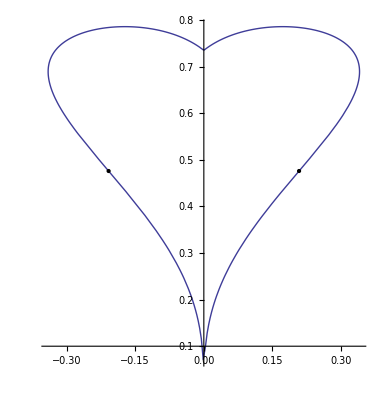

```mathematica
ParametricPlot[par[t],{t,-1,1},PlotRange->All,Epilog->{Point[pts//N]}]
```

```mathematica
InflectionPoints[par[t],t]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::dinv: The expression t^(-1 + Tan[t]) (1 + Tan[t]) involves unknowns in more than one argument, so inverse functions cannot be used.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction will be suppressed during this calculation.

Solve::dinv: The expression (t^2)^t^2 involves unknowns in more than one argument, so inverse functions cannot be used.

ReplaceAll::reps: {Solve[(-21/100 Power[« 2 »] Power[« 2 »] - 1/2 Power[« 2 »] Power[« 2 »] - 3/10 t Power[« 2 »] Power[« 2 »] Sin[« 1 »] - 1/4 Power[« 2 »] Power[« 2 »] Power[« 2 »]) (« 1 ») - « 1 » == 0, t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{Cos[t] Log[Abs[t]] Sin[t],(t^2)^(3/20) √Cos[t]}/.Solve[(-(21 √Cos[t])/(100 (t^2)^(17/20))-1/2 (t^2)^(3/20) √Cos[t]-(3 t Sin[t])/(10 (t^2)^(17/20) √Cos[t])-((t^2)^(3/20) Sin[t]^2)/(4 Cos[t]^(3/2))) (Cos[t]^2 Log[Abs[t]]-Log[Abs[t]] Sin[t]^2+(Cos[t] Sin[t] Abs'[t])/Abs[t])-((3 t √Cos[t])/(10 (t^2)^(17/20))-((t^2)^(3/20) Sin[t])/(2 √Cos[t])) (-4 Cos[t] Log[Abs[t]] Sin[t]+(2 Cos[t]^2 Abs'[t])/Abs[t]-(2 Sin[t]^2 Abs'[t])/Abs[t]-(Cos[t] Sin[t] Abs'[t]^2)/Abs[t]^2+(Cos[t] Sin[t] Abs''[t])/Abs[t])==0,t]

### Singular Points

```mathematica
par/@{-1,0,1}
```

∞::indet: Indeterminate expression 0 (-∞) encountered.

{{0,√Cos[1]},{Indeterminate,0},{0,√Cos[1]}}

```mathematica
N[%]
```

{{0.,0.735053},{Indeterminate,0.},{0.,0.735053}}

```mathematica
Limit[par[t],t->0]
```

{0,0}

```mathematica
ParametricPlot[par[t],{t,-1,1},PlotStyle->Red,PlotRange->All]
```

-Graphics-

### Slope

```mathematica
FullSimplify[Slope[par[t],t],-1<t<1&&a>0]
```

(Abs[t]^(3/10) (3 Cos[t]-5 t Sin[t]))/(5 √Cos[t] (t Cos[2 t] Log[t^2]+Sin[2 t]))

### SpecialAffineCurvature

```mathematica
ByteCount[k=SpecialAffineCurvature[par[t],t]]//Timing
```

{0.00391,159928}

```mathematica
Simplify[k,-1<t<1&&a>0]//Timing
```

$Aborted

### Tangential Angle

```mathematica
TangentialAngle[par[t]/.Abs[c_]:>Sqrt[c^2],t]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

### Vector Properties

```mathematica
parm=a{Sin[t] Cos[t] Log[Abs[t]],Sqrt[t^2]^(3/10) Sqrt[Cos[t]]};
assum=-1<t<1&&a>0;
xform={Abs[x_]^(n_/;Mod[n,2]==0):>x^n};
```

#### VectorLength

```mathematica
Assuming[assum,FullSimplify[Norm[parm]/.xform]]
```

a √(Cos[t] (Abs[t]^(3/5)+Cos[t] Log[Abs[t]]^2 Sin[t]^2))

#### NormalVector

```mathematica
Assuming[assum,FullSimplify[NormalVector[parm,t]/.xform]]
```

{(t (-3 Cos[t]+5 t Sin[t]))/(Abs[t]^(7/10) √(Cos[t] (Abs[t]^(3/5) (9 Cos[t]-30 t Sin[t])+25 (t Cos[2 t] Log[t^2]+Sin[2 t])^2+25 Abs[t]^(13/5) Sin[t] Tan[t]))),(5 (Abs[t] Cos[2 t] Log[t^2]+Sign[t] Sin[2 t]))/(√(Abs[t]^(3/5) (9 Cos[t]-30 t Sin[t])+25 (t Cos[2 t] Log[t^2]+Sin[2 t])^2+25 Abs[t]^(13/5) Sin[t] Tan[t]))}

#### TangentVector

```mathematica
Assuming[assum,FullSimplify[TangentVector[parm,t]/.xform]]
```

{(5 (Abs[t] Cos[2 t] Log[t^2]+Sign[t] Sin[2 t]))/(√(Abs[t]^(3/5) (9 Cos[t]-30 t Sin[t])+25 (t Cos[2 t] Log[t^2]+Sin[2 t])^2+25 Abs[t]^(13/5) Sin[t] Tan[t])),(t (3 Cos[t]-5 t Sin[t]))/(Abs[t]^(7/10) √(Cos[t] (Abs[t]^(3/5) (9 Cos[t]-30 t Sin[t])+25 (t Cos[2 t] Log[t^2]+Sin[2 t])^2+25 Abs[t]^(13/5) Sin[t] Tan[t])))}

## HeartCurve3

### Equation

```mathematica
(y-(2 (Abs[x]+x^2-6))/(3 (Abs[x]+x^2+2)))^2+x^2==36
```

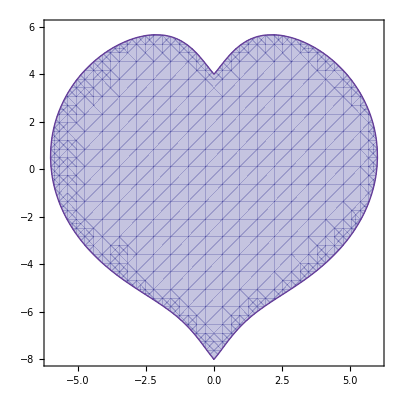

```mathematica
RegionPlot[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36,{x,-6,6},{y,-8,6}]
```

```mathematica
eqn=x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2-36/.Abs[x]:>Sqrt[x^2]
```

-36+x^2+(-(2 (-6+x^2+√(x^2)))/(3 (2+x^2+√(x^2)))+y)^2

```mathematica
Simplify[Numerator[Factor[Expand[eqn]]],x∈Reals]
```

9 x^6+36 (-32+4 y+y^2)+x^4 (-275-12 y+9 y^2)+x^2 (-1628+36 y+45 y^2)+2 (9 x^4+6 (-112+4 y+3 y^2)+x^2 (-302-12 y+9 y^2)) Abs[x]

```mathematica
Solve[9 x^6+36 (-32+4 y+y^2)+x^4 (-275-12 y+9 y^2)+x^2 (-1628+36 y+45 y^2)+2 (9 x^4+6 (-112+4 y+3 y^2)+x^2 (-302-12 y+9 y^2)) Abs[x]==0,Abs[x]]
```

{{Abs[x]→(1152+1628 x^2+275 x^4-9 x^6-144 y-36 x^2 y+12 x^4 y-36 y^2-45 x^2 y^2-9 x^4 y^2)/(2 (-672-302 x^2+9 x^4+24 y-12 x^2 y+18 y^2+9 x^2 y^2))}}

```mathematica
Numerator[Factor[x^2-((1152+1628 x^2+275 x^4-9 x^6-144 y-36 x^2 y+12 x^4 y-36 y^2-45 x^2 y^2-9 x^4 y^2)/(2 (-672-302 x^2+9 x^4+24 y-12 x^2 y+18 y^2+9 x^2 y^2)))^2]]
```

-(-1152+1344 x-1628 x^2+604 x^3-275 x^4-18 x^5+9 x^6+144 y-48 x y+36 x^2 y+24 x^3 y-12 x^4 y+36 y^2-36 x y^2+45 x^2 y^2-18 x^3 y^2+9 x^4 y^2) (-1152-1344 x-1628 x^2-604 x^3-275 x^4+18 x^5+9 x^6+144 y+48 x y+36 x^2 y-24 x^3 y-12 x^4 y+36 y^2+36 x y^2+45 x^2 y^2+18 x^3 y^2+9 x^4 y^2)

```mathematica
Numerator[Factor[Expand[x^2-((1152+1628 x^2+275 x^4-9 x^6-144 y-36 x^2 y+12 x^4 y-36 y^2-45 x^2 y^2-9 x^4 y^2)/(2 (-672-302 x^2+9 x^4+24 y-12 x^2 y+18 y^2+9 x^2 y^2)))^2]]]
```

-(-1152+1344 x-1628 x^2+604 x^3-275 x^4-18 x^5+9 x^6+144 y-48 x y+36 x^2 y+24 x^3 y-12 x^4 y+36 y^2-36 x y^2+45 x^2 y^2-18 x^3 y^2+9 x^4 y^2) (-1152-1344 x-1628 x^2-604 x^3-275 x^4+18 x^5+9 x^6+144 y+48 x y+36 x^2 y-24 x^3 y-12 x^4 y+36 y^2+36 x y^2+45 x^2 y^2+18 x^3 y^2+9 x^4 y^2)

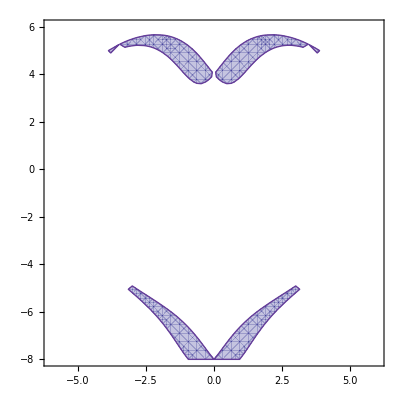

```mathematica
RegionPlot[-(-1152+1344 x-1628 x^2+604 x^3-275 x^4-18 x^5+9 x^6+144 y-48 x y+36 x^2 y+24 x^3 y-12 x^4 y+36 y^2-36 x y^2+45 x^2 y^2-18 x^3 y^2+9 x^4 y^2) (-1152-1344 x-1628 x^2-604 x^3-275 x^4+18 x^5+9 x^6+144 y+48 x y+36 x^2 y-24 x^3 y-12 x^4 y+36 y^2+36 x y^2+45 x^2 y^2+18 x^3 y^2+9 x^4 y^2)>0,{x,-6,6},{y,-8,6}]
```

### Plot

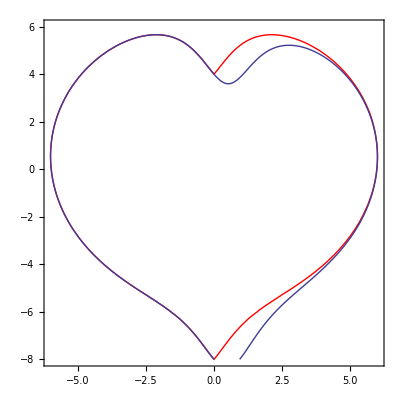
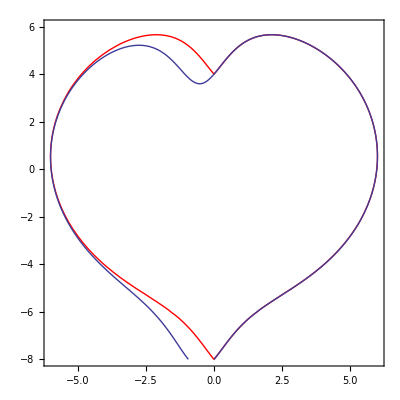

```mathematica
Show[{ContourPlot[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2==36,{x,-6,6},{y,-8,6},ContourStyle->{Thick,Red}],ContourPlot[#==0,{x,-6,6},{y,-8,6},PlotPoints->50,MaxRecursion->3]}]&/@{(-1152+1344 x-1628 x^2+604 x^3-275 x^4-18 x^5+9 x^6+144 y-48 x y+36 x^2 y+24 x^3 y-12 x^4 y+36 y^2-36 x y^2+45 x^2 y^2-18 x^3 y^2+9 x^4 y^2) ,(-1152-1344 x-1628 x^2-604 x^3-275 x^4+18 x^5+9 x^6+144 y+48 x y+36 x^2 y-24 x^3 y-12 x^4 y+36 y^2+36 x y^2+45 x^2 y^2+18 x^3 y^2+9 x^4 y^2)}
```

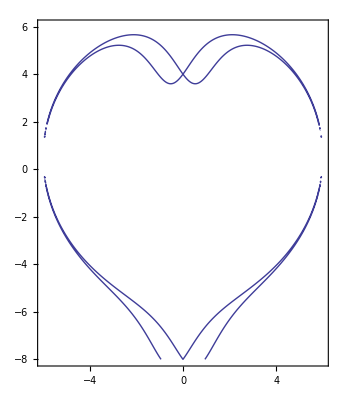

```mathematica
ContourPlot[-(-1152+1344 x-1628 x^2+604 x^3-275 x^4-18 x^5+9 x^6+144 y-48 x y+36 x^2 y+24 x^3 y-12 x^4 y+36 y^2-36 x y^2+45 x^2 y^2-18 x^3 y^2+9 x^4 y^2) (-1152-1344 x-1628 x^2-604 x^3-275 x^4+18 x^5+9 x^6+144 y+48 x y+36 x^2 y-24 x^3 y-12 x^4 y+36 y^2+36 x y^2+45 x^2 y^2+18 x^3 y^2+9 x^4 y^2)==0,{x,-6,6},{y,-8,6},AspectRatio->Automatic,PlotPoints->50,MaxRecursion->3]
```

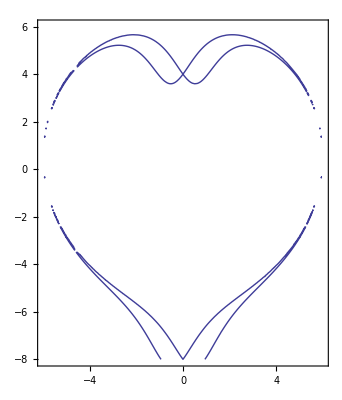

```mathematica
ContourPlot[x^2==((1152+1628 x^2+275 x^4-9 x^6-144 y-36 x^2 y+12 x^4 y-36 y^2-45 x^2 y^2-9 x^4 y^2)/(2 (-672-302 x^2+9 x^4+24 y-12 x^2 y+18 y^2+9 x^2 y^2)))^2,{x,-6,6},{y,-8,6},AspectRatio->Automatic,PlotPoints->50]
```

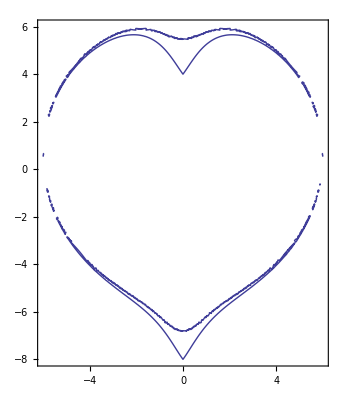

```mathematica
ContourPlot[Abs[x]==(1152+1628 x^2+275 x^4-9 x^6-144 y-36 x^2 y+12 x^4 y-36 y^2-45 x^2 y^2-9 x^4 y^2)/(2 (-672-302 x^2+9 x^4+24 y-12 x^2 y+18 y^2+9 x^2 y^2)),{x,-6,6},{y,-8,6},AspectRatio->Automatic,PlotPoints->50]
```

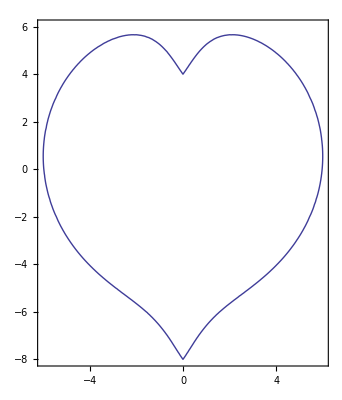

```mathematica
ContourPlot[9 x^6+36 (-32+4 y+y^2)+x^4 (-275-12 y+9 y^2)+x^2 (-1628+36 y+45 y^2)+2 (9 x^4+6 (-112+4 y+3 y^2)+x^2 (-302-12 y+9 y^2)) Abs[x]==0,{x,-6,6},{y,-8,6},AspectRatio->Automatic]
```

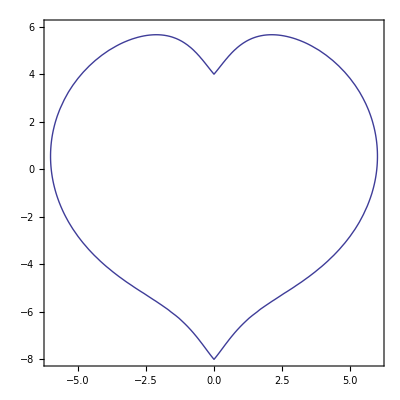

```mathematica
ContourPlot[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2==36,{x,-6,6},{y,-8,6}]
```

### Area

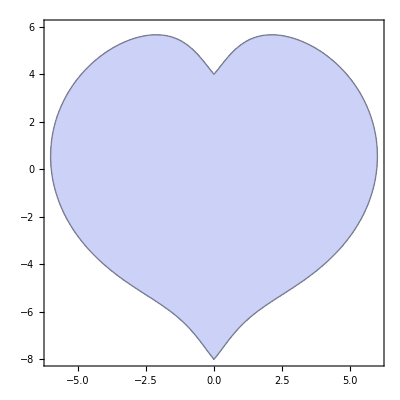

```mathematica
RegionPlot[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36,{x,-6,6},{y,-8,6}]
```

```mathematica
Integrate[Boole[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36],{x,-∞,∞},{y,-∞,∞}]
```

36 π

```mathematica
Area[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36,{x,y}]//Timing
```

{0.916328,36 π}

### AreaInertiaTensor

```mathematica
AreaInertiaTensor[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36,{x,y}]//Timing
```

{816.41,{{1/(441 √11)2 (-10752 √11+78106 √11 π+21 ⅈ √(75-ⅈ √7) π-47 √(7 (75-ⅈ √7)) π-21 ⅈ √(75+ⅈ √7) π-47 √(7 (75+ⅈ √7)) π+84 ⅈ √(75-ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75-ⅈ √7)) ArcTan[(3 √7)/47]-84 ⅈ √(75+ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75+ⅈ √7)) ArcTan[(3 √7)/47]+84 √(75+ⅈ √7) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-188 ⅈ √(7 (75+ⅈ √7)) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-84 √(75-ⅈ √7) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]-188 ⅈ √(7 (75-ⅈ √7)) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]+42 √(75+ⅈ √7) Log[9/2]-94 ⅈ √(7 (75+ⅈ √7)) Log[9/2]+42 √(75+ⅈ √7) Log[64]-94 ⅈ √(7 (75+ⅈ √7)) Log[64]-42 √(75+ⅈ √7) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]+94 ⅈ √(7 (75+ⅈ √7)) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]-42 √(75-ⅈ √7) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]-94 ⅈ √(7 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]),0},{0,324 π}}}

```mathematica
expr=1/(441 √11)2 (-10752 √11+78106 √11 π+21 ⅈ √(75-ⅈ √7) π-47 √(7 (75-ⅈ √7)) π-21 ⅈ √(75+ⅈ √7) π-47 √(7 (75+ⅈ √7)) π+84 ⅈ √(75-ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75-ⅈ √7)) ArcTan[(3 √7)/47]-84 ⅈ √(75+ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75+ⅈ √7)) ArcTan[(3 √7)/47]+84 √(75+ⅈ √7) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-188 ⅈ √(7 (75+ⅈ √7)) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-84 √(75-ⅈ √7) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]-188 ⅈ √(7 (75-ⅈ √7)) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]+42 √(75+ⅈ √7) Log[9/2]-94 ⅈ √(7 (75+ⅈ √7)) Log[9/2]+42 √(75+ⅈ √7) Log[64]-94 ⅈ √(7 (75+ⅈ √7)) Log[64]-42 √(75+ⅈ √7) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]+94 ⅈ √(7 (75+ⅈ √7)) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]-42 √(75-ⅈ √7) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]-94 ⅈ √(7 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]);
```

```mathematica
FullSimplify//@expr
```

$Aborted

```mathematica
Together[expr]
```

1/(441 √11)2 (-10752 √11+78106 √11 π+21 ⅈ √(75-ⅈ √7) π-47 √(7 (75-ⅈ √7)) π-21 ⅈ √(75+ⅈ √7) π-47 √(7 (75+ⅈ √7)) π+84 ⅈ √(75-ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75-ⅈ √7)) ArcTan[(3 √7)/47]-84 ⅈ √(75+ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75+ⅈ √7)) ArcTan[(3 √7)/47]+84 √(75+ⅈ √7) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-188 ⅈ √(7 (75+ⅈ √7)) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-84 √(75-ⅈ √7) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]-188 ⅈ √(7 (75-ⅈ √7)) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]+42 √(75+ⅈ √7) Log[9/2]-94 ⅈ √(7 (75+ⅈ √7)) Log[9/2]+42 √(75+ⅈ √7) Log[64]-94 ⅈ √(7 (75+ⅈ √7)) Log[64]-42 √(75+ⅈ √7) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]+94 ⅈ √(7 (75+ⅈ √7)) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]-42 √(75-ⅈ √7) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]-94 ⅈ √(7 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)])

```mathematica
FullSimplify[expr]
```

1/4851 4 ((429583+8 √(154 (3105+2 √(766250-77532 ⅈ √154)))) π+16 (-3696+√(77 (-621+91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]]+√(77 (-621-91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]]))

```mathematica
expr=1/4851 4 ((429583+8 √(154 (3105+2 √(766250-77532 ⅈ √154)))) π+16 (-3696+√(77 (-621+91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]]+√(77 (-621-91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]]));
```

```mathematica
{{expr,0},{0,324 π}}
```

{{1/4851 4 ((429583+8 √(154 (3105+2 √(766250-77532 ⅈ √154)))) π+16 (-3696+√(77 (-621+91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]]+√(77 (-621-91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]])),0},{0,324 π}}

```mathematica
expr//N//Chop
```

1073.65

```mathematica
TrigToExp/@expr
```

1/4851 4 (-59136+429583 π+8 √(154 (3105+2 √(766250-77532 ⅈ √154))) π+16 √(77 (-621+91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]]+16 √(77 (-621-91 ⅈ √7)) Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]])

```mathematica
expr2=1/4851 4 (-59136+429583 π+8 √(154 (3105+2 √(766250-77532 ⅈ √154))) π+ Log[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]^(16 √(77 (-621-91 ⅈ √7)))Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]^(16 √(77 (-621+91 ⅈ √7)))]);
```

```mathematica
N[expr2]
```

1073.65-1.72525 ⅈ

```mathematica
RootReduce[Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]^(16 √(77 (-621-91 ⅈ √7)))Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]^(16 √(77 (-621+91 ⅈ √7)))]
```

Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,4]^Root[172369630461952+24482304 #1^2+#1^4&,4] Root[1+1732 #1^2+29199750 #1^4+1732 #1^6+#1^8&,6]^Root[172369630461952+24482304 #1^2+#1^4&,3]

```mathematica
N[{{1/(441 √11)2 (-10752 √11+78106 √11 π+21 ⅈ √(75-ⅈ √7) π-47 √(7 (75-ⅈ √7)) π-21 ⅈ √(75+ⅈ √7) π-47 √(7 (75+ⅈ √7)) π+84 ⅈ √(75-ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75-ⅈ √7)) ArcTan[(3 √7)/47]-84 ⅈ √(75+ⅈ √7) ArcTan[(3 √7)/47]-188 √(7 (75+ⅈ √7)) ArcTan[(3 √7)/47]+84 √(75+ⅈ √7) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-188 ⅈ √(7 (75+ⅈ √7)) ArcTanh[(175 (3 ⅈ+√7))/(-91 ⅈ+39 √7)]-84 √(75-ⅈ √7) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]-188 ⅈ √(7 (75-ⅈ √7)) ArcTanh[(525 ⅈ-175 √7)/(91 ⅈ+39 √7)]+42 √(75+ⅈ √7) Log[9/2]-94 ⅈ √(7 (75+ⅈ √7)) Log[9/2]+42 √(75+ⅈ √7) Log[64]-94 ⅈ √(7 (75+ⅈ √7)) Log[64]-42 √(75+ⅈ √7) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]+94 ⅈ √(7 (75+ⅈ √7)) Log[-72 (147 ⅈ+√7+12 ⅈ √(150-2 ⅈ √7))]-42 √(75-ⅈ √7) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]-94 ⅈ √(7 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]),0},{0,324 π}}]//Chop
```

{{1073.65,0},{0,1017.88}}

```mathematica
AreaInertiaTensor[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36,{y,x}]//Timing
```

{7.72114,{{∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] 1/3 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^3+Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2]^3)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] 1/3 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^3+Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2]^3)ⅆy+∫_-8^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2] 1/3 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^3+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2]^3)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] 1/3 (-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,1]^3+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2]^3)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2]^4 1/3 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^3+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4]^3)ⅆy+∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] 1/3 (-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,3]^3+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4]^3)ⅆy,∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2]^2)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2]^2)ⅆy+∫_-8^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2] 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2]^2)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] 1/2 y (Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2]^2)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2]^4 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4]^2)ⅆy+∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] 1/2 y (Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,3]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4]^2)ⅆy},{∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2]^2)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2]^2)ⅆy+∫_-8^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2] 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2]^2)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] 1/2 y (Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2]^2)ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2]^4 1/2 y (Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4]^2)ⅆy+∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] 1/2 y (Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,3]^2-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4]^2)ⅆy,∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] y^2 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]+Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2])ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] y^2 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]+Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,2])ⅆy+∫_-8^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2] y^2 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2])ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3]^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,4] y^2 (-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,1]+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,2])ⅆy+∫_Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,2]^4 y^2 (-Root[-1152+144 y+36 y^2+(1344-48 y-36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(604+24 y-18 y^2) #1^3+(-275-12 y+9 y^2) #1^4-18 #1^5+9 #1^6&,1]+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4])ⅆy+∫_4^Root[-421153257444096+36757680414112 #1+61758806839096 #1^2-2744795314140 #1^3-3585962715210 #1^4+62429606577 #1^5+100904657634 #1^6-294597162 #1^7-1366710246 #1^8-2005479 #1^9+7072758 #1^10&,3] y^2 (-Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,3]+Root[-1152+144 y+36 y^2+(-1344+48 y+36 y^2) #1+(-1628+36 y+45 y^2) #1^2+(-604-24 y+18 y^2) #1^3+(-275-12 y+9 y^2) #1^4+18 #1^5+9 #1^6&,4])ⅆy}}}

```mathematica
N[%]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {2.75887}. NIntegrate obtained 1.25219×10^-16 and 2.51915×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.72459}. NIntegrate obtained 4.56326×10^-17 and 2.53689×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {2.75887}. NIntegrate obtained 1.25219×10^-16 and 2.51915×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{7.72114,{{1017.88+1.11999×10^-17 ⅈ,7.10543×10^-15+2.58416×10^-17 ⅈ},{7.10543×10^-15+2.58416×10^-17 ⅈ,1073.65+5.58391×10^-17 ⅈ}}}

```mathematica
Chop[Rest[%]]
```

{{{1017.88,0},{0,1073.65}}}

### Centroid

```mathematica
Centroid[x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36,{x,y}]//Timing
```

{288.326,{0,1/462 (16016 π+7 ⅈ √(11 (75-ⅈ √7)) π+75 √(77 (75-ⅈ √7)) π-7 ⅈ √(11 (75+ⅈ √7)) π+75 √(77 (75+ⅈ √7)) π-28 ⅈ √(11 (75-ⅈ √7)) ArcTan[(√7)/75]-300 √(77 (75-ⅈ √7)) ArcTan[(√7)/75]+28 ⅈ √(11 (75+ⅈ √7)) ArcTan[(√7)/75]-300 √(77 (75+ⅈ √7)) ArcTan[(√7)/75]+28 ⅈ √(11 (75+ⅈ √7)) ArcTan[(259 (3-ⅈ √7))/(41 (-7 ⅈ+3 √7))]-300 √(77 (75+ⅈ √7)) ArcTan[(259 (3-ⅈ √7))/(41 (-7 ⅈ+3 √7))]-28 ⅈ √(11 (75-ⅈ √7)) ArcTan[(259 (3+ⅈ √7))/(41 (7 ⅈ+3 √7))]-300 √(77 (75-ⅈ √7)) ArcTan[(259 (3+ⅈ √7))/(41 (7 ⅈ+3 √7))]-14 √(11 (75+ⅈ √7)) Log[-(147 ⅈ)/4-(√7)/4-3 ⅈ √(150-2 ⅈ √7)]-150 ⅈ √(77 (75+ⅈ √7)) Log[-(147 ⅈ)/4-(√7)/4-3 ⅈ √(150-2 ⅈ √7)]-14 √(11 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]+150 ⅈ √(77 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)])}}

```mathematica
c={0,1/462 (16016 π+7 ⅈ √(11 (75-ⅈ √7)) π+75 √(77 (75-ⅈ √7)) π-7 ⅈ √(11 (75+ⅈ √7)) π+75 √(77 (75+ⅈ √7)) π-28 ⅈ √(11 (75-ⅈ √7)) ArcTan[(√7)/75]-300 √(77 (75-ⅈ √7)) ArcTan[(√7)/75]+28 ⅈ √(11 (75+ⅈ √7)) ArcTan[(√7)/75]-300 √(77 (75+ⅈ √7)) ArcTan[(√7)/75]+28 ⅈ √(11 (75+ⅈ √7)) ArcTan[(259 (3-ⅈ √7))/(41 (-7 ⅈ+3 √7))]-300 √(77 (75+ⅈ √7)) ArcTan[(259 (3-ⅈ √7))/(41 (-7 ⅈ+3 √7))]-28 ⅈ √(11 (75-ⅈ √7)) ArcTan[(259 (3+ⅈ √7))/(41 (7 ⅈ+3 √7))]-300 √(77 (75-ⅈ √7)) ArcTan[(259 (3+ⅈ √7))/(41 (7 ⅈ+3 √7))]-14 √(11 (75+ⅈ √7)) Log[-(147 ⅈ)/4-(√7)/4-3 ⅈ √(150-2 ⅈ √7)]-150 ⅈ √(77 (75+ⅈ √7)) Log[-(147 ⅈ)/4-(√7)/4-3 ⅈ √(150-2 ⅈ √7)]-14 √(11 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)]+150 ⅈ √(77 (75-ⅈ √7)) Log[(147 ⅈ)/4-(√7)/4+3 ⅈ √(150+2 ⅈ √7)])};
```

```mathematica
c//N//Chop
```

{0,-15.1681}

```mathematica
FullSimplify[c]//Timing
```

{99.6329,{0,1/462 (176 (91+(14 ⅈ)/(√(75+16 √22))) π-352 √7 (√(75+16 √22) (2 π-ArcTan[3 √7])+√(-150-2 ⅈ √7) Log[Root[16-165880 #1^2+467195937 #1^4+172808 #1^6+16 #1^8&,2]]+(1+ⅈ) √(75 ⅈ+√7) Log[Root[16-165880 #1^2+467195937 #1^4+172808 #1^6+16 #1^8&,8]]))}}

```mathematica
N[%]
```

{99.6329,{0.,-15.1681-4.92151×10^-16 ⅈ}}

### ImplicitCurvature

```mathematica
Simplify[Curvature[eqn,{x,y}],(x|y)∈Reals]
```

(8 (2 x^2 (243 x^12+27 x^10 (124-12 y+9 y^2)+27 x^8 (549-80 y+120 y^2)+864 (132+164 y+61 y^2+6 y^3)+18 x^4 (2476-924 y+2079 y^2+1512 y^3)+3 x^6 (8302+2916 y+1485 y^2+1728 y^3)+16 x^2 (-3394+5436 y+8262 y^2+2079 y^3))+(81 x^14-1728 (2+y)^2 (5+4 y)+9 x^12 (247-12 y+9 y^2)+9 x^10 (1799-228 y+243 y^2)+3 x^8 (14699-108 y+3537 y^2+864 y^3)+36 x^4 (248+1292 y+5403 y^2+2016 y^3)+x^6 (65344+12996 y+28053 y^2+30240 y^3)) Abs[x]+144 (1136+2636 y+1563 y^2+252 y^3) Abs[x]^3))/(81 Abs[x] (2+x^2+Abs[x])^6 ((4 (3 (39 x^4+9 x^6+x^2 (68-48 y)-32 (2+y))+(81 x^4+9 x^6-40 (7+6 y)) Abs[x]+(226-96 y) Abs[x]^3)^2)/(81 (2+x^2+Abs[x])^6)+4 (y-(2 (-6+x^2+Abs[x]))/(3 (2+x^2+Abs[x])))^2)^(3/2))

```mathematica
FullSimplify[%,(x|y)∈Reals]
```

(8 (2 x^2 (243 x^12+27 x^10 (124+3 y (-4+3 y))+27 x^8 (549+40 y (-2+3 y))+864 (2+y) (66+y (49+6 y))+18 x^4 (2476+21 y (-44+9 y (11+8 y)))+3 x^6 (8302+27 y (108+y (55+64 y)))+16 x^2 (-3394+9 y (604+3 y (306+77 y))))+(81 x^14-1728 (2+y)^2 (5+4 y)+9 x^12 (247+3 y (-4+3 y))+9 x^10 (1799+3 y (-76+81 y))+x^6 (65344+9 y (1444+3117 y+3360 y^2))+3 x^8 (14699+27 y (-4+y (131+32 y)))+144 x^2 (1136+y (2636+3 y (521+84 y)))+36 x^4 (248+y (1292+3 y (1801+672 y)))) Abs[x]))/(81 Abs[x] (2+x^2+Abs[x])^6 ((4 (3 (39 x^4+9 x^6+x^2 (68-48 y)-32 (2+y))+(x^2 (226+9 x^2 (9+x^2)-96 y)-40 (7+6 y)) Abs[x])^2)/(81 (2+x^2+Abs[x])^6)+4 (y+2/3 (-1+8/(2+x^2+Abs[x])))^2)^(3/2))

### Inflection Points

```mathematica
InflectionPoints[eqn,{x,y}]
```

$Aborted

```mathematica
x^2+(y-(2(x^2+Abs[x]-6))/(3(x^2+Abs[x]+2)))^2<36
```

```mathematica
solns=Solve[Refine[eqn,x>0]==0,y]
```

{{y→1/(3 (4+4 x+5 x^2+2 x^3+x^4))(-24-8 x-6 x^2+4 x^3+2 x^4-3 √(576+1152 x+2000 x^2+1984 x^3+1708 x^4+952 x^5+455 x^6+116 x^7+22 x^8-4 x^9-x^10))},{y→1/(3 (4+4 x+5 x^2+2 x^3+x^4))(-24-8 x-6 x^2+4 x^3+2 x^4+3 √(576+1152 x+2000 x^2+1984 x^3+1708 x^4+952 x^5+455 x^6+116 x^7+22 x^8-4 x^9-x^10))}}

```mathematica
Block[{y=solns[[2,1,2]]},Reduce[D[y,x,x]==0&&eqn==0,x,Reals]]
```

x==Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,4]

```mathematica
infl1=RootReduce[{x,1/(3 (4+4 x+5 x^2+2 x^3+x^4))(-24-8 x-6 x^2+4 x^3+2 x^4+3 √(576+1152 x+2000 x^2+1984 x^3+1708 x^4+952 x^5+455 x^6+116 x^7+22 x^8-4 x^9-x^10))}/.x->Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,4]]
```

{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,4],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,6]}

```mathematica
N[%]
```

{0.222575,4.31524}

```mathematica
Block[{y=solns[[1,1,2]]},Reduce[D[y,x,x]==0&&eqn==0,x,Reals]]
```

x==Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,5]||x==Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,6]

```mathematica
N[%]
```

x==0.310051||x==2.48101

```mathematica
infl2=RootReduce[{x,(1/(3 (4+4 x+5 x^2+2 x^3+x^4)))(-24-8 x-6 x^2+4 x^3+2 x^4-3 Sqrt[576+1152 x+2000 x^2+1984 x^3+1708 x^4+952 x^5+455 x^6+116 x^7+22 x^8-4 x^9-x^10])}/.x->#]&/@{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,5],Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,6]}
```

{{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,5],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,1]},{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,6],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,3]}}

```mathematica
N[infl2]
```

{{0.310051,-7.54183},{2.48101,-5.29778}}

```mathematica
infl=Sort[Flatten[{#,{-#[[1]],#[[2]]}}&/@Join[{infl1},infl2],1]]
```

{{-Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,4],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,6]},{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,4],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,6]},{-Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,5],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,1]},{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,5],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,1]},{-Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,6],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,3]},{Root[-2939328+18055872 #1-8394192 #1^2-54774144 #1^3-25565652 #1^4+5054076 #1^5+2642365 #1^6+142014 #1^7+80139 #1^8+59472 #1^9+20259 #1^10+4374 #1^11+729 #1^12&,6],Root[392306542375124391541-45083735106017182296 #1-66976301308928197311 #1^2+6230574433580979373 #1^3+4681667935932634563 #1^4-337541035325460297 #1^5-171565622259389399 #1^6+9034985729185491 #1^7+3491005230985500 #1^8-119999654152371 #1^9-37565312625918 #1^10+634764313260 #1^11+167737528728 #1^12&,3]}}

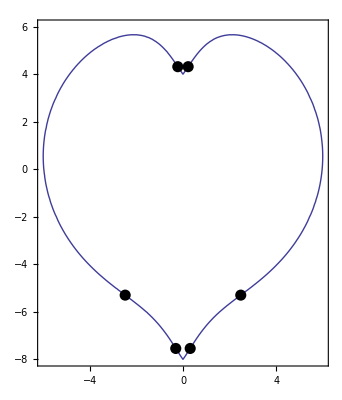

```mathematica
ContourPlot[9 x^6+36 (-32+4 y+y^2)+x^4 (-275-12 y+9 y^2)+x^2 (-1628+36 y+45 y^2)+2 (9 x^4+6 (-112+4 y+3 y^2)+x^2 (-302-12 y+9 y^2)) Abs[x]==0,{x,-6,6},{y,-8,6},AspectRatio->Automatic,Epilog->{PointSize[.02],Point[infl]}]
```

### Singular Points

```mathematica
SingularPoints[eqn,{x,y}]
```

{}

```mathematica
Solve[eqn==0/.x->0,y]
```

{{y→-8},{y→4}}

### Slope

```mathematica
eqn=FullSimplify[Slope[x^2+(y-(2(x^2+√(x^2)-6))/(3(x^2+√(x^2)+2)))^2==36,{x,y}],x∈Reals]
```

Piecewise[{{(16 (-1+2 x))/(3 (2+(-1+x) x)^2)-(3 x (2+(-1+x) x))/(6 (2+y)+(-1+x) x (-2+3 y)), x<0}, {(16 (1+2 x))/(3 (2+x+x^2)^2)-(3 x (2+x+x^2))/(6 (2+y)+x (1+x) (-2+3 y)), True}}]

```mathematica
FullSimplify[eqn,x<0]
```

(16 (-1+2 x))/(3 (2+(-1+x) x)^2)-(3 x (2+(-1+x) x))/(6 (2+y)+(-1+x) x (-2+3 y))

```mathematica
FullSimplify[eqn,x>0]
```

(16 (1+2 x))/(3 (2+x+x^2)^2)-(3 x (2+x+x^2))/(6 (2+y)+x (1+x) (-2+3 y))

```mathematica
FullSimplify[Slope[(-1152+1344 x-1628 x^2+604 x^3-275 x^4-18 x^5+9 x^6+144 y-48 x y+36 x^2 y+24 x^3 y-12 x^4 y+36 y^2-36 x y^2+45 x^2 y^2-18 x^3 y^2+9 x^4 y^2) (-1152-1344 x-1628 x^2-604 x^3-275 x^4+18 x^5+9 x^6+144 y+48 x y+36 x^2 y-24 x^3 y-12 x^4 y+36 y^2+36 x y^2+45 x^2 y^2+18 x^3 y^2+9 x^4 y^2)==0,{x,y}]]
```

{(x (-243 x^10+45 x^8 (293+3 (4-3 y) y)-2 x^6 (68065+3 y (2704+9 y (-172+y (-8+3 y))))-3 x^4 (279116+27 y (-164+y (-637+y (8+9 y))))-36 (27008+y (-5872+y (-1612+3 y (56+9 y))))+x^2 (-1660432+3 y (58432-9 y (-3520+y (184+51 y))))))/(3 (12 (2+y)+x^4 (-2+3 y)+x^2 (10+9 y)) (9 x^6+36 (-4+y) (8+y)+x^4 (-293+3 y (-4+3 y))+x^2 (-988+3 y (20+9 y)))),(x (-243 x^10+45 x^8 (293+3 (4-3 y) y)-2 x^6 (68065+3 y (2704+9 y (-172+y (-8+3 y))))-3 x^4 (279116+27 y (-164+y (-637+y (8+9 y))))-36 (27008+y (-5872+y (-1612+3 y (56+9 y))))+x^2 (-1660432+3 y (58432-9 y (-3520+y (184+51 y))))))/(3 (12 (2+y)+x^4 (-2+3 y)+x^2 (10+9 y)) (9 x^6+36 (-4+y) (8+y)+x^4 (-293+3 y (-4+3 y))+x^2 (-988+3 y (20+9 y))))}

## HeartCurve4

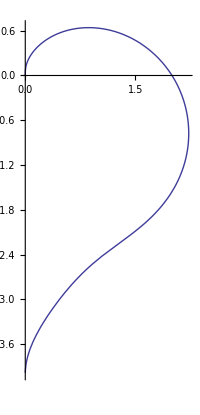

```mathematica
PolarPlot[2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5),{t,0,2π}]
```

### ArcLength

```mathematica
(s=ArcLength[2-2Sin[t]+Sin[t](√Abs[Cos[t]])/(Sin[t]+7/5),{t,0,2π}])//Timing
```

$Aborted

### Area

```mathematica
PolarPlot[2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5),{t,-π/2,π/2}]
```

-Graphics-

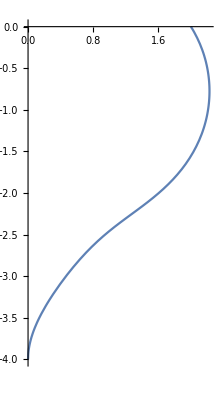
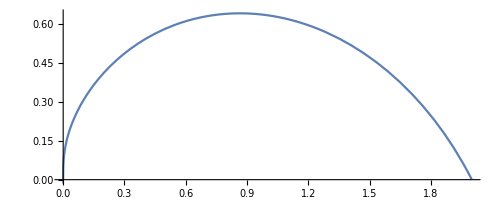

```mathematica
{PolarPlot[2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5),{t,-Pi/2,0}],PolarPlot[2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5),{t,0,π/2}]}
```

#### Numeric

```mathematica
NIntegrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,0,π/2},PrecisionGoal->20,WorkingPrecision->50]
```

12.523038095382442467082986344570414249633439259172

#### V4.1.5

```mathematica
Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}]//Timing
```

∞::indet: Indeterminate expression 0 encountered.

{29. Second,∫_(-π/2)^(π/2) (2-2 Sin[t]+(√Cos[t] Sin[t])/(7/5+Sin[t]))^2 ⅆt}

#### V4.2.1

```mathematica
Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}]//Timing
```

∞::indet: Indeterminate expression 0 encountered.

{29.73 Second,∫_(-π/2)^(π/2) (2-2 Sin[t]+(√Cos[t] Sin[t])/(7/5+Sin[t]))^2 ⅆt}

#### V5.2 [CORRECT]

```mathematica
Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}]//Timing
```

{158.678 Second,1/1260(7665+(7560-(882-294 ⅈ) √5 6^(3/4)) π-588 √5 6^(3/4) ArcTan[1-(√5)/6^(1/4)]+588 √5 6^(3/4) ArcTan[1+(√5)/6^(1/4)]+√π (-(6650 Gamma[7/4] Hypergeometric2F1[3/4,1,9/4,-25/24])/Gamma[9/4]-(2625 Gamma[3/4] Hypergeometric2F1[1,3/4,1/2,49/24])/Gamma[5/4])+7200 Hypergeometric2F1[1,1,5/4,24/49]-3528 Log[6]+294 √5 6^(3/4) Log[12+5 √6-2 √5 6^(3/4)]-294 √5 6^(3/4) Log[12+5 √6+2 √5 6^(3/4)])}

...correct...

```mathematica
FullSimplify[Last[%]]
```

(6-(21-7 ⅈ)/(√5 6^(1/4))) π-(5 π^(3/2) (25 Hypergeometric2F1[3/4,1,1/2,49/24]+38 Hypergeometric2F1[3/4,1,9/4,-25/24]))/(96 √2 Gamma[5/4] Gamma[9/4])+1/420 (2555+196 √5 6^(3/4) ArcTan[1+(√5)/6^(1/4)]-196 √5 6^(3/4) ArcTan[1+Root[-25+6 #1^4&,1]]+2400 Hypergeometric2F1[1,1,5/4,24/49]-1176 Log[6]+98 √5 6^(3/4) Log[12+5 √6-2 √5 6^(3/4)]-98 √5 6^(3/4) Log[12+5 √6+2 √5 6^(3/4)])

```mathematica
N[%]
```

12.523-3.55271×10^-15 ⅈ

```mathematica
ToRadicals[%3]//TraditionalForm
```

(6-(21-7 ⅈ)/(√5 6^(1/4))) π-(5 π^(3/2) (25 _2 F_1(3/4,1;1/2;49/24)+38 _2 F_1(3/4,1;9/4;-25/24)))/(96 √2 Γ(5/4) Γ(9/4))+1/420 (2555-196 √5 6^(3/4) tan^-1(1-(√5)/6^(1/4))+196 √5 6^(3/4) tan^-1(1+(√5)/6^(1/4))+2400 _2 F_1(1,1;5/4;24/49)-1176 log(6)+98 √5 6^(3/4) log(12+5 √6-2 √5 6^(3/4))-98 √5 6^(3/4) log(12+5 √6+2 √5 6^(3/4)))

#### V6 [WRONG]

```mathematica
Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}]//Timing
```

{183.85,1/(132300 Gamma[9/4])(793800 π Gamma[9/4]-8 √π Gamma[11/4] (-468195+69041 Hypergeometric2F1[-1/2,1,1/4,25/49]+152304 Hypergeometric2F1[1/2,1,1/4,25/49])-441 Gamma[9/4] (-225+392 √5 6^(3/4) ArcCot[1-(2 6^(1/4))/(√5)]-392 √5 6^(3/4) ArcCot[1+(2 6^(1/4))/(√5)]+840 Log[2]+840 Log[3]-168 √5 6^(3/4) Log[12+5 √6-2 √5 6^(3/4)]+168 √5 6^(3/4) Log[12+5 √6+2 √5 6^(3/4)]-28 √5 6^(3/4) Log[12 √5-10 6^(3/4)+5 √30]+28 √5 6^(3/4) Log[12 √5+10 6^(3/4)+5 √30]))}

```mathematica
N[%]
```

{183.85,18.1549}

#### V7 [WRONG]

```mathematica
Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}]//Timing
```

{178.94,1/(132300 Gamma[9/4])(793800 π Gamma[9/4]-8 √π Gamma[11/4] (-468195+69041 Hypergeometric2F1[-1/2,1,1/4,25/49]+152304 Hypergeometric2F1[1/2,1,1/4,25/49])-441 Gamma[9/4] (-225+392 √5 6^(3/4) ArcCot[1-(2 6^(1/4))/(√5)]-392 √5 6^(3/4) ArcCot[1+(2 6^(1/4))/(√5)]+840 Log[2]+840 Log[3]-196 √5 6^(3/4) Log[12+5 √6-2 √5 6^(3/4)]+196 √5 6^(3/4) Log[12+5 √6+2 √5 6^(3/4)]))}

#### V8 [CORRECT]

```mathematica
$Version
```

8.0 for Linux x86 (64-bit) (September 21, 2010)

```mathematica
(i=Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}])//Timing
```

{202.827,6 π-(√π Gamma[3/4] (-468195+69041 Hypergeometric2F1[-1/2,1,1/4,25/49]+152304 Hypergeometric2F1[1/2,1,1/4,25/49]))/(7350 Gamma[9/4])+1/300 (1825+336 ⅈ √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12 ⅈ-√5 6^(3/4))]+336 √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12-√5 6^(3/4))]+336 ⅈ √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12 ⅈ+√5 6^(3/4))]+336 √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12+√5 6^(3/4))]-840 Log[2]-840 Log[3]+168 √5 6^(3/4) Log[12+5 √6-2 √5 6^(3/4)]-168 ⅈ √5 6^(3/4) Log[12-5 √6-2 ⅈ √5 6^(3/4)]+168 ⅈ √5 6^(3/4) Log[12-5 √6+2 ⅈ √5 6^(3/4)]-168 √5 6^(3/4) Log[12+5 √6+2 √5 6^(3/4)])}

```mathematica
N[i]//Chop
```

12.523

```mathematica
(i2=FullSimplify[i])//Timing
```

{537.286,1/(14700 Gamma[9/4])(89425 Gamma[9/4]-2 √π Gamma[3/4] (-468195+69041 Hypergeometric2F1[-1/2,1,1/4,25/49]+152304 Hypergeometric2F1[1/2,1,1/4,25/49])-1176 Gamma[9/4] ((-75+14 √5 6^(3/4)) π+7 (2 √5 6^(3/4) ArcCot[1-(2 6^(1/4))/(√5)]-2 ⅈ √5 6^(3/4) ArcCot[1+(2 ⅈ 6^(1/4))/(√5)]-2 √5 6^(3/4) ArcCot[1+(2 6^(1/4))/(√5)]+2 ⅈ √5 6^(3/4) ArcCot[1+Root[-96+25 #1^4&,3]]-2 √5 6^(3/4) ArcTan[2 √(600+245 √6)]+2 √5 6^(3/4) ArcTanh[2 √5 6^(1/4) (5-2 √6)]+5 Log[6])))}

```mathematica
N[i2]//Chop
```

12.523

#### V13 [CORRECT]

```mathematica
$Version
```

13.0.0 for Mac OS X x86 (64-bit) (October 17, 2021)

```mathematica
(a=Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,π/2}])//Timing
```

{252.128,6 π-(3 √π Gamma[3/4] (-468195+69041 Hypergeometric2F1[-1/2,1,1/4,25/49]+152304 Hypergeometric2F1[1/2,1,1/4,25/49]))/(9800 Gamma[13/4])+1/300 (1825+336 ⅈ √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12 ⅈ-√5 6^(3/4))]+336 √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12-√5 6^(3/4))]+336 ⅈ √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12 ⅈ+√5 6^(3/4))]+336 √5 6^(3/4) ArcTan[(√5 6^(3/4))/(12+√5 6^(3/4))]+840 Log[2]-840 Log[12]+168 √5 6^(3/4) Log[12+5 √6-2 √5 6^(3/4)]-168 ⅈ √5 6^(3/4) Log[12-5 √6-2 ⅈ √5 6^(3/4)]+168 ⅈ √5 6^(3/4) Log[12-5 √6+2 ⅈ √5 6^(3/4)]-168 √5 6^(3/4) Log[12+5 √6+2 √5 6^(3/4)])}

```mathematica
N[a,20]//Chop
```

12.523038095382442467

```mathematica
(a2=FullSimplify[a])//Timing
```

$Aborted

#### Indefinite V13 [WRONG]

```mathematica
$Version
```

```mathematica
i=Integrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,t]
```

6 t+8 Cos[t]+8/3 Cos[t]^(3/2)-14/5 Log[1+(5 Sin[t])/7]+Sin[t]-49/(5 (7+5 Sin[t]))+1/(75 (7+5 Sin[t]))2 (250 AppellF1[3/4,-1/2,1,7/4,Cos[t]^2,-25/24 Cos[t]^2] Cos[t]^(3/2)+21 √5 6^(3/4) (2 ArcTan[1-(√5 √Cos[t])/6^(1/4)]-2 ArcTan[1+(√5 √Cos[t])/6^(1/4)]-Log[12-2 √5 6^(3/4) √Cos[t]+5 √6 Cos[t]]+Log[12+2 √5 6^(3/4) √Cos[t]+5 √6 Cos[t]])) (7+5 √(Sin[t]^2))-Sin[2 t]

...wrong...

```mathematica
f[x_?NumericQ]:=NIntegrate[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5))^2,{t,-π/2,x}]
```

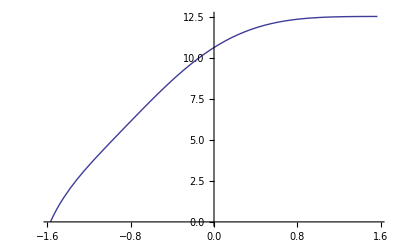

```mathematica
Plot[f[x],{x,-π/2,π/2}]
```

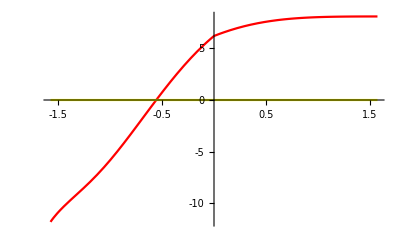

```mathematica
Plot[Through[{Re,Im}[i]],{t,-π/2,π/2},PlotStyle->{Red,Yellow},Evaluated->True]
```

```mathematica
Limit[i,t->π/2,Direction->"FromBelow"]-Limit[i,t->-π/2,Direction->"FromAbove"]
```

73/12+6 π-14/5 Log[12/7]-14/5 Log[7/2]

```mathematica
N[%,20]
```

19.915962741033538762

...wrong...

### AreaInertiaTensor

```mathematica
AreaInertiaTensor[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5)),{t,-π/2,π/2}]//Timing
```

### Centroid

```mathematica
Centroid[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5)),{t,-π/2,π/2}]//Timing
```

$Aborted

### Curvature

#### Parametric

```mathematica
abs[x_]:=Sqrt[x^2]
```

```mathematica
Simplify[Curvature[(2-2Sin[t]+Sin[t](√abs[Cos[t]])/(Sin[t]+7/5))a,t],a>0&&0<t<2π]
```

(150 Abs[Cos[t]]^(5/2) Sin[t]^2 (7+5 Sin[t])+32 Abs[Cos[t]]^(7/2) (7+5 Sin[t])^3+16 Abs[Cos[t]]^(3/2) (-1+Sin[t]) (-1+2 Sin[t]) (7+5 Sin[t])^3+25 √Abs[Cos[t]] (56 Cos[t]^4+3 Sin[t]^4 (7+5 Sin[t]))-5/8 (-1+Sin[t]) (516-9200 Cos[2 t]+620 Cos[4 t]+6202 Sin[t]-4323 Sin[3 t]-125 Sin[5 t]))/(4 a Abs[Cos[t]]^(3/2) (7+5 Sin[t])^3 ((2-2 Sin[t]+(√Abs[Cos[t]] Sin[t])/(7/5+Sin[t]))^2+((-70 Cos[t]^2+5 Sin[t]^2 (7+5 Sin[t])+4 Abs[Cos[t]]^(3/2) (7+5 Sin[t])^2)^2)/(4 Abs[Cos[t]] (7+5 Sin[t])^4))^(3/2))

#### Polar

```mathematica
FullSimplify[Curvature[2-2 Sin[q]+Sin[q] Sqrt[abs[Cos[q]]]/(Sin[q]+7/5),q],a>0&&0<q<2π]
```

$Aborted

### Equation

```mathematica
PolarPlot[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5)),{t,0,2π}]
```

-Graphics-

```mathematica
r=(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5));
```

```mathematica
eq=Numerator[Factor[{x-r Cos[t],y-r Sin[t]}]]
```

{7 x-14 Cos[t]+5 x Sin[t]+4 Cos[t] Sin[t]-5 Cos[t]^(3/2) Sin[t]+10 Cos[t] Sin[t]^2,7 y-14 Sin[t]+5 y Sin[t]+4 Sin[t]^2-5 √Cos[t] Sin[t]^2+10 Sin[t]^3}

```mathematica
eq2={(7 x-14 Cos[t]+5 x Sin[t]+4 Cos[t] Sin[t]+10 Cos[t] Sin[t]^2)^2-25 Cos[t]^3 Sin[t]^2,(7 y-14 Sin[t]+5 y Sin[t]+4 Sin[t]^2+10 Sin[t]^3)^2-25Cos[t] Sin[t]^4}
```

{-25 Cos[t]^3 Sin[t]^2+(7 x-14 Cos[t]+5 x Sin[t]+4 Cos[t] Sin[t]+10 Cos[t] Sin[t]^2)^2,-25 Cos[t] Sin[t]^4+(7 y-14 Sin[t]+5 y Sin[t]+4 Sin[t]^2+10 Sin[t]^3)^2}

```mathematica
eq3=TrigExpand[eq2]/.{Cos[t]->(1-s^2)/(1+s^2),Sin[t]->2 s/(1+s^2)};
```

```mathematica
eq4=Factor[Together[eq3]]
```

{1/((1+s^2)^6)(196-224 s-764 s^2+416 s^3+1604 s^4-192 s^5-1872 s^6-192 s^7+1204 s^8+416 s^9-564 s^10-224 s^11+196 s^12-196 x-168 s x-64 s^2 x+296 s^3 x+460 s^4 x+464 s^5 x-464 s^7 x-460 s^8 x-296 s^9 x+64 s^10 x+168 s^11 x+196 s^12 x+49 x^2+140 s x^2+394 s^2 x^2+700 s^3 x^2+1135 s^4 x^2+1400 s^5 x^2+1580 s^6 x^2+1400 s^7 x^2+1135 s^8 x^2+700 s^9 x^2+394 s^10 x^2+140 s^11 x^2+49 s^12 x^2),1/((1+s^2)^6)(784 s^2-896 s^3-1488 s^4-128 s^5+2656 s^6-128 s^7-688 s^8-896 s^9+784 s^10-392 s y-336 s^2 y-520 s^3 y+256 s^4 y+400 s^5 y+1184 s^6 y+400 s^7 y+256 s^8 y-520 s^9 y-336 s^10 y-392 s^11 y+49 y^2+140 s y^2+394 s^2 y^2+700 s^3 y^2+1135 s^4 y^2+1400 s^5 y^2+1580 s^6 y^2+1400 s^7 y^2+1135 s^8 y^2+700 s^9 y^2+394 s^10 y^2+140 s^11 y^2+49 s^12 y^2)}

```mathematica
eq5=Numerator[eq4];
```

```mathematica
GroebnerBasis[eq5,{x,y},s]
```

$Aborted

```mathematica
soln=Factor[Resultant[Sequence@@eq5,s,Method->Modular]]
```

6125288180133018059450980761600000000000000000000 (38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12) (-78675968000000 x+683601963520000 x^2-1945109398937600 x^3+1660567782340096 x^4+841537238796800 x^5-916842798360048 x^6-49894839097600 x^7+104579917271256 x^8-9734835292000 x^9+2480978810625 x^10+78032500000 x^11+15006250000 x^12+51982336000000 x y-1539794941440000 x^2 y+5211507394867200 x^3 y-3161294945806592 x^4 y-1249087358220800 x^5 y+706654000993248 x^6 y-34960744224000 x^7 y+42705898324600 x^8 y+5175286900000 x^9 y+567707875000 x^10 y+33417216000000 x y^2+543503100000000 x^2 y^2-1567754329131200 x^3 y^2-759263754477200 x^4 y^2-480241854339800 x^5 y^2+696163946616824 x^6 y^2+19712580636000 x^7 y^2+21328253611875 x^8 y^2-1592500000 x^9 y^2+74725000000 x^10 y^2-453173575680000 y^3-6182591219302400 x y^3-2545738797080192 x^2 y^3+504830541801600 x^3 y^3+2218202695230144 x^4 y^3-32723885435500 x^5 y^3+256988260243400 x^6 y^3+7783673800000 x^7 y^3+2040670625000 x^8 y^3+299418255360000 y^4+3722578839564800 x y^4+1459819836872319 x^2 y^4+209996465462000 x^3 y^4+1468035569807936 x^4 y^4+40380139988000 x^5 y^4+37440742981875 x^6 y^4-447882500000 x^7 y^4+152437500000 x^8 y^4+192483164160000 y^5+4051110261512000 x y^5+3667626861505544 x^2 y^5-86492326527000 x^3 y^5+326413421547600 x^4 y^5-2241857500000 x^5 y^5+3799625625000 x^6 y^5+1848848569860096 y^6+630810749211200 x y^6+1548708579885424 x^2 y^6-24100030600000 x^3 y^6+48751768130625 x^4 y^6-635017500000 x^5 y^6+162625000000 x^6 y^6+1469480777883648 y^7-89109400315500 x y^7+287536314518400 x^2 y^7-7249213800000 x^3 y^7+3384856875000 x^4 y^7+453538757293056 y^8-30629754660000 x y^8+28051750710000 x^2 y^8-322920000000 x^3 y^8+95406250000 x^4 y^8+68631978009600 y^9-2398969400000 x y^9+1403730000000 x^2 y^9+5462150760000 y^10-56160000000 x y^10+29100000000 x^2 y^10+220536000000 y^11+3600000000 y^12)

```mathematica
solns=Rest[FactorList[soln]][[All,1]]
```

{38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12,-78675968000000 x+683601963520000 x^2-1945109398937600 x^3+1660567782340096 x^4+841537238796800 x^5-916842798360048 x^6-49894839097600 x^7+104579917271256 x^8-9734835292000 x^9+2480978810625 x^10+78032500000 x^11+15006250000 x^12+51982336000000 x y-1539794941440000 x^2 y+5211507394867200 x^3 y-3161294945806592 x^4 y-1249087358220800 x^5 y+706654000993248 x^6 y-34960744224000 x^7 y+42705898324600 x^8 y+5175286900000 x^9 y+567707875000 x^10 y+33417216000000 x y^2+543503100000000 x^2 y^2-1567754329131200 x^3 y^2-759263754477200 x^4 y^2-480241854339800 x^5 y^2+696163946616824 x^6 y^2+19712580636000 x^7 y^2+21328253611875 x^8 y^2-1592500000 x^9 y^2+74725000000 x^10 y^2-453173575680000 y^3-6182591219302400 x y^3-2545738797080192 x^2 y^3+504830541801600 x^3 y^3+2218202695230144 x^4 y^3-32723885435500 x^5 y^3+256988260243400 x^6 y^3+7783673800000 x^7 y^3+2040670625000 x^8 y^3+299418255360000 y^4+3722578839564800 x y^4+1459819836872319 x^2 y^4+209996465462000 x^3 y^4+1468035569807936 x^4 y^4+40380139988000 x^5 y^4+37440742981875 x^6 y^4-447882500000 x^7 y^4+152437500000 x^8 y^4+192483164160000 y^5+4051110261512000 x y^5+3667626861505544 x^2 y^5-86492326527000 x^3 y^5+326413421547600 x^4 y^5-2241857500000 x^5 y^5+3799625625000 x^6 y^5+1848848569860096 y^6+630810749211200 x y^6+1548708579885424 x^2 y^6-24100030600000 x^3 y^6+48751768130625 x^4 y^6-635017500000 x^5 y^6+162625000000 x^6 y^6+1469480777883648 y^7-89109400315500 x y^7+287536314518400 x^2 y^7-7249213800000 x^3 y^7+3384856875000 x^4 y^7+453538757293056 y^8-30629754660000 x y^8+28051750710000 x^2 y^8-322920000000 x^3 y^8+95406250000 x^4 y^8+68631978009600 y^9-2398969400000 x y^9+1403730000000 x^2 y^9+5462150760000 y^10-56160000000 x y^10+29100000000 x^2 y^10+220536000000 y^11+3600000000 y^12}

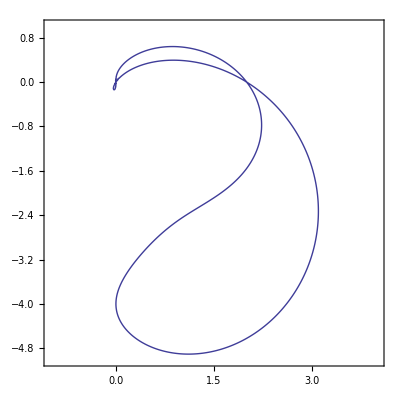
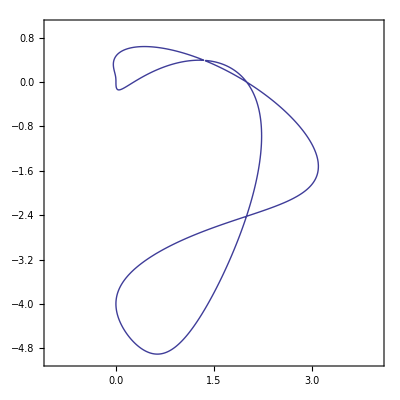

```mathematica
ContourPlot[#==0,{x,-1,4},{y,-5,1},Contours->{0},MaxRecursion->4]&/@solns
```

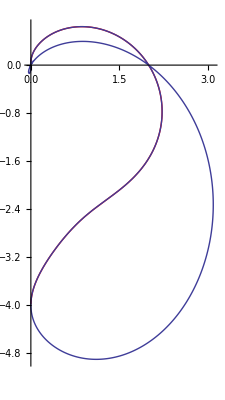
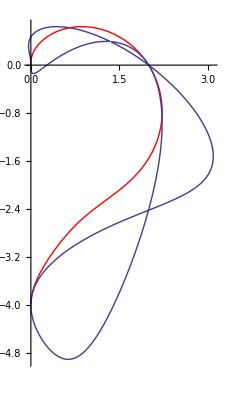

```mathematica
Show[{
PolarPlot[(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5)),{t,0,2π},PlotStyle->{Thick,Red}],
ContourPlot[#==0,{x,-1,4},{y,-5,1},Contours->{0},MaxRecursion->4]
}]&/@solns
```

```mathematica
right=38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12;
```

```mathematica
both=right(right/.x->-x);
```

```mathematica
Factor[both]
```

(38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2+9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2+5600 x^5 y^3-152096 x^6 y^3-3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4+20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4+7200 x^3 y^5-93696 x^4 y^5-10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6+11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6+1600 x y^7-18432 x^2 y^7-10500 x^3 y^7+89480 x^4 y^7+800 x y^8+51456 x^2 y^8+15265 x^4 y^8-3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12) (38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12)

```mathematica
eqn=(38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2+9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2+5600 x^5 y^3-152096 x^6 y^3-3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4+20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4+7200 x^3 y^5-93696 x^4 y^5-10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6+11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6+1600 x y^7-18432 x^2 y^7-10500 x^3 y^7+89480 x^4 y^7+800 x y^8+51456 x^2 y^8+15265 x^4 y^8-3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12) (38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12);
```

```mathematica
expanded=Factor[(#a^(24-Exponent[#/.y->x,x]))&/@Expand[eqn]]
```

```mathematica
expanded=(38416 a^4 x^8-19208 a^2 x^10+2401 x^12-76832 a^3 x^8 y+19208 a x^10 y+37632 a^4 x^6 y^2+9800 a^3 x^7 y^2-18816 a^2 x^8 y^2+11956 x^10 y^2+5600 a^4 x^5 y^3-152096 a^3 x^6 y^3-3500 a^2 x^7 y^3+76440 a x^8 y^3+8591 a^4 x^4 y^4+20400 a^3 x^5 y^4+53016 a^2 x^6 y^4+24390 x^8 y^4+7200 a^4 x^3 y^5-93696 a^3 x^4 y^5-10500 a^2 x^5 y^5+118680 a x^6 y^5-625 a^4 x^2 y^6+11400 a^3 x^3 y^6+94864 a^2 x^4 y^6+26020 x^6 y^6+1600 a^4 x y^7-18432 a^3 x^2 y^7-10500 a^2 x^3 y^7+89480 a x^4 y^7+800 a^3 x y^8+51456 a^2 x^2 y^8+15265 x^4 y^8-3500 a^2 x y^9+32640 a x^2 y^9+9216 a^2 y^10+4656 x^2 y^10+4608 a y^11+576 y^12) (38416 a^4 x^8-19208 a^2 x^10+2401 x^12-76832 a^3 x^8 y+19208 a x^10 y+37632 a^4 x^6 y^2-9800 a^3 x^7 y^2-18816 a^2 x^8 y^2+11956 x^10 y^2-5600 a^4 x^5 y^3-152096 a^3 x^6 y^3+3500 a^2 x^7 y^3+76440 a x^8 y^3+8591 a^4 x^4 y^4-20400 a^3 x^5 y^4+53016 a^2 x^6 y^4+24390 x^8 y^4-7200 a^4 x^3 y^5-93696 a^3 x^4 y^5+10500 a^2 x^5 y^5+118680 a x^6 y^5-625 a^4 x^2 y^6-11400 a^3 x^3 y^6+94864 a^2 x^4 y^6+26020 x^6 y^6-1600 a^4 x y^7-18432 a^3 x^2 y^7+10500 a^2 x^3 y^7+89480 a x^4 y^7-800 a^3 x y^8+51456 a^2 x^2 y^8+15265 x^4 y^8+3500 a^2 x y^9+32640 a x^2 y^9+9216 a^2 y^10+4656 x^2 y^10+4608 a y^11+576 y^12);
```

```mathematica
FullSimplify[expanded/.Thread[{x,y}->(2-2Sin[t]+Sin[t](√Cos[t])/(Sin[t]+7/5)){Cos[t],Sin[t]}],t∈Reals&&a>0]//Timing
```

{1559.90386,(2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^16 (38416 a^4 Cos[t]^8+37632 a^4 Cos[t]^6 Sin[t]^2+5600 a^4 Cos[t]^5 Sin[t]^3+8591 a^4 Cos[t]^4 Sin[t]^4+7200 a^4 Cos[t]^3 Sin[t]^5-625 a^4 Cos[t]^2 Sin[t]^6+1600 a^4 Cos[t] Sin[t]^7-76832 a^3 Cos[t]^8 Sin[t] (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))+9800 a^3 Cos[t]^7 Sin[t]^2 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-152096 a^3 Cos[t]^6 Sin[t]^3 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))+20400 a^3 Cos[t]^5 Sin[t]^4 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-93696 a^3 Cos[t]^4 Sin[t]^5 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))+11400 a^3 Cos[t]^3 Sin[t]^6 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-18432 a^3 Cos[t]^2 Sin[t]^7 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))+800 a^3 Cos[t] Sin[t]^8 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-19208 a^2 Cos[t]^10 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2-18816 a^2 Cos[t]^8 Sin[t]^2 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2-3500 a^2 Cos[t]^7 Sin[t]^3 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+53016 a^2 Cos[t]^6 Sin[t]^4 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2-10500 a^2 Cos[t]^5 Sin[t]^5 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+94864 a^2 Cos[t]^4 Sin[t]^6 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2-10500 a^2 Cos[t]^3 Sin[t]^7 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+51456 a^2 Cos[t]^2 Sin[t]^8 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2-3500 a^2 Cos[t] Sin[t]^9 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+9216 a^2 Sin[t]^10 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+19208 a Cos[t]^10 Sin[t] (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+76440 a Cos[t]^8 Sin[t]^3 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+118680 a Cos[t]^6 Sin[t]^5 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+89480 a Cos[t]^4 Sin[t]^7 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+32640 a Cos[t]^2 Sin[t]^9 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+4608 a Sin[t]^11 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+2401 Cos[t]^12 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+11956 Cos[t]^10 Sin[t]^2 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+24390 Cos[t]^8 Sin[t]^4 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+26020 Cos[t]^6 Sin[t]^6 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+15265 Cos[t]^4 Sin[t]^8 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+4656 Cos[t]^2 Sin[t]^10 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+576 Sin[t]^12 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4) (38416 a^4 Cos[t]^8+37632 a^4 Cos[t]^6 Sin[t]^2-5600 a^4 Cos[t]^5 Sin[t]^3+8591 a^4 Cos[t]^4 Sin[t]^4-7200 a^4 Cos[t]^3 Sin[t]^5-625 a^4 Cos[t]^2 Sin[t]^6-1600 a^4 Cos[t] Sin[t]^7-76832 a^3 Cos[t]^8 Sin[t] (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-9800 a^3 Cos[t]^7 Sin[t]^2 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-152096 a^3 Cos[t]^6 Sin[t]^3 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-20400 a^3 Cos[t]^5 Sin[t]^4 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-93696 a^3 Cos[t]^4 Sin[t]^5 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-11400 a^3 Cos[t]^3 Sin[t]^6 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-18432 a^3 Cos[t]^2 Sin[t]^7 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-800 a^3 Cos[t] Sin[t]^8 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))-19208 a^2 Cos[t]^10 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2-18816 a^2 Cos[t]^8 Sin[t]^2 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+3500 a^2 Cos[t]^7 Sin[t]^3 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+53016 a^2 Cos[t]^6 Sin[t]^4 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+10500 a^2 Cos[t]^5 Sin[t]^5 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+94864 a^2 Cos[t]^4 Sin[t]^6 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+10500 a^2 Cos[t]^3 Sin[t]^7 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+51456 a^2 Cos[t]^2 Sin[t]^8 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+3500 a^2 Cos[t] Sin[t]^9 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+9216 a^2 Sin[t]^10 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^2+19208 a Cos[t]^10 Sin[t] (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+76440 a Cos[t]^8 Sin[t]^3 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+118680 a Cos[t]^6 Sin[t]^5 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+89480 a Cos[t]^4 Sin[t]^7 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+32640 a Cos[t]^2 Sin[t]^9 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+4608 a Sin[t]^11 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^3+2401 Cos[t]^12 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+11956 Cos[t]^10 Sin[t]^2 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+24390 Cos[t]^8 Sin[t]^4 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+26020 Cos[t]^6 Sin[t]^6 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+15265 Cos[t]^4 Sin[t]^8 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+4656 Cos[t]^2 Sin[t]^10 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4+576 Sin[t]^12 (2+Sin[t] (-2+(√Cos[t])/(7/5+Sin[t])))^4)}

```mathematica
AlgebraicDegree[both,{x,y}]
```

24

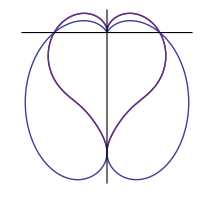

```mathematica
Show[{
PolarPlot[(2-2Sin[t]+Sin[t](√Abs[Cos[t]])/(Sin[t]+7/5)),{t,0,2π},PlotStyle->{Thick,Red},Ticks->None],
ContourPlot[both==0,{x,-4,4},{y,-5,1},Contours->{0},MaxRecursion->4,Ticks->None]
},ImageSize->200]
```

### Slope

```mathematica
Slope[(2-2 Sin[t]+Sin[t] Sqrt[Sqrt[Cos[t]^2]]/(Sin[t]+7/5)) {Cos[t],Sin[t]},t]//FullSimplify[#,t>0]&
```

(Cos[t] (-32 Abs[Cos[t]]^(3/2) (-1+2 Sin[t]) (7+5 Sin[t])^2+5 (-5+20 Cos[2 t]-15 Cos[4 t]+14 Sin[t]+70 Sin[3 t])))/(8 (70 Cos[t]^4+(7+5 Sin[t]) (-15 Cos[t]^2 Sin[t]^2-4 Abs[Cos[t]]^(7/2) (7+5 Sin[t])+4 Abs[Cos[t]]^(3/2) (-1+Sin[t]) Sin[t] (7+5 Sin[t]))))

```mathematica
Slope[2-2 Sin[q]+Sin[q] Sqrt[Sqrt[Cos[q]^2]]/(Sin[q]+7/5),q]//FullSimplify[#,0<q<2π]&
```

-((Cos[q/2]+Sin[q/2]) (-32 Abs[Cos[q]]^(3/2) (-1+2 Sin[q]) (7+5 Sin[q])^2+5 (-5+20 Cos[2 q]-15 Cos[4 q]+14 Sin[q]+70 Sin[3 q])))/((Cos[q/2]-Sin[q/2]) (365-1000 Cos[2 q]+75 Cos[4 q]+940 Sin[q]+32 Abs[Cos[q]]^(3/2) (1+2 Sin[q]) (7+5 Sin[q])^2-500 Sin[3 q]))

```mathematica
Slope[(38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2+9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2+5600 x^5 y^3-152096 x^6 y^3-3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4+20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4+7200 x^3 y^5-93696 x^4 y^5-10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6+11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6+1600 x y^7-18432 x^2 y^7-10500 x^3 y^7+89480 x^4 y^7+800 x y^8+51456 x^2 y^8+15265 x^4 y^8-3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12) (38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12)==0,{x,y}]//FullSimplify
```

(x (-34588806 x^22-5176556 x^20 (-98+y (98+61 y))-48020 x^18 (57624+y (-115248+y (-18816+y (86044+27079 y))))-1764 x^16 (-3764768+y (11294304+y (-2881200+y (-15885016+5 y (920514+y (1701378+361307 y))))))-8 y^14 (-160000+y (-160000+y (-60000+y (-21243664+y (47849855+3456 y (19072+y (8064+y (1456+97 y))))))))-x^2 y^12 (-22649375+192 y (-130000+y (2601708+y (-18171375+y (11771285+18 y (1621248+7 y (114080+y (22640+1623 y))))))))-3 x^4 y^10 (-40249375+y (-218989312+y (2487289680+y (-7374077864+y (-78213625+48 y (171530752+35 y (2955360+y (656624+51227 y))))))))-2 x^6 y^8 (-53874719+y (-3259830720+y (20329558704+y (-31858053312+y (-17291979050+y (28562307328+35 y (655831584+y (167097008+14383307 y))))))))-10 x^8 y^6 (141803256+y (-2838744160+y (10722515220+y (-8526229240+y (-11946150337+2 y (3460745608+7 y (633827722+y (191359682+18487207 y))))))))-12 x^10 y^4 (519057784+y (-5019022960+y (12037438980+y (-2256233056+y (-16039453805+y (2292554128+7 y (1318796976+y (494861964+54848833 y))))))))-8 x^14 (737894528+y (-2951578112+y (1505907200+y (8026485376+y (-8228287025+y (-6616925504+5 y (1020811120+y (799588664+129036487 y))))))))-7 x^12 y^2 (1445670912+y (-8734261760+y (12801382888+y (8223342680+y (-23351532365+4 y (-1237599664+y (3139657170+y (1581243910+207078799 y))))))))))/(663552 y^19 (4+y)^3 (10+3 y)+470596 x^22 (49+61 y)+9604 x^20 (-28812+y (-9408+y (64533+27079 y)))+588 x^18 (1882384+y (-960400+y (-7942508+5 y (613676+y (1417815+361307 y)))))+2 x^16 (-737894528+y (752953600+y (6019864032+5 y (-1645657405+2 y (-827115688+y (765608340+y (699640081+129036487 y)))))))+8 x^2 y^13 (-1120000+y (-1200000+y (-480000+y (-180571144+9 y (47849855+384 y (181184+y (80640+y (15288+1067 y))))))))+3 x^4 y^11 (-22649375+16 y (-1690000+y (36423912+y (-272570625+8 y (23542570+9 y (6890304+35 y (102672+y (21508+1623 y))))))))+x^6 y^9 (-201246875+y (-1204441216+y (14923738080+y (-47931506116+5 y (-109499075+48 y (257296128+7 y (23642880+y (5581304+461043 y))))))))+2 x^8 y^7 (-53874719+y (-3667309560+y (25411948380+y (-43804823304+y (-25937968575+2 y (23206874704+35 y (573852636+y (156653445+14383307 y))))))))+4 x^12 y^3 (519057784+y (-6273778700+y (18056158470+y (-3948407848+y (-32078907610+3 y (1719415596+7 y (1098997480+y (453623467+54848833 y))))))))+2 x^10 y^5 (425409768+y (-9935604560+y (42890060880+y (-38368031580+y (-59730751685+2 y (19034100844+7 y (3802966332+y (1243837933+129410449 y))))))))+x^14 y (1445670912+y (-13101392640+y (25602765776+y (20558356700+y (-70054597095+4 y (-4331598824+5 y (2511725736+y (1423119519+207078799 y)))))))))

```mathematica
Slope[(38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2+9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2+5600 x^5 y^3-152096 x^6 y^3-3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4+20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4+7200 x^3 y^5-93696 x^4 y^5-10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6+11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6+1600 x y^7-18432 x^2 y^7-10500 x^3 y^7+89480 x^4 y^7+800 x y^8+51456 x^2 y^8+15265 x^4 y^8-3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12) (38416 x^8-19208 x^10+2401 x^12-76832 x^8 y+19208 x^10 y+37632 x^6 y^2-9800 x^7 y^2-18816 x^8 y^2+11956 x^10 y^2-5600 x^5 y^3-152096 x^6 y^3+3500 x^7 y^3+76440 x^8 y^3+8591 x^4 y^4-20400 x^5 y^4+53016 x^6 y^4+24390 x^8 y^4-7200 x^3 y^5-93696 x^4 y^5+10500 x^5 y^5+118680 x^6 y^5-625 x^2 y^6-11400 x^3 y^6+94864 x^4 y^6+26020 x^6 y^6-1600 x y^7-18432 x^2 y^7+10500 x^3 y^7+89480 x^4 y^7-800 x y^8+51456 x^2 y^8+15265 x^4 y^8+3500 x y^9+32640 x^2 y^9+9216 y^10+4656 x^2 y^10+4608 y^11+576 y^12)==0,{x,y}]//FullSimplify
```

{(x (-34588806 x^22-5176556 x^20 (-98+y (98+61 y))-48020 x^18 (57624+y (-115248+y (-18816+y (86044+27079 y))))-1764 x^16 (-3764768+y (11294304+y (-2881200+y (-15885016+5 y (920514+y (1701378+361307 y))))))-8 y^14 (-160000+y (-160000+y (-60000+y (-21243664+y (47849855+3456 y (19072+y (8064+y (1456+97 y))))))))-x^2 y^12 (-22649375+192 y (-130000+y (2601708+y (-18171375+y (11771285+18 y (1621248+7 y (114080+y (22640+1623 y))))))))-3 x^4 y^10 (-40249375+y (-218989312+y (2487289680+y (-7374077864+y (-78213625+48 y (171530752+35 y (2955360+y (656624+51227 y))))))))-2 x^6 y^8 (-53874719+y (-3259830720+y (20329558704+y (-31858053312+y (-17291979050+y (28562307328+35 y (655831584+y (167097008+14383307 y))))))))-10 x^8 y^6 (141803256+y (-2838744160+y (10722515220+y (-8526229240+y (-11946150337+2 y (3460745608+7 y (633827722+y (191359682+18487207 y))))))))-12 x^10 y^4 (519057784+y (-5019022960+y (12037438980+y (-2256233056+y (-16039453805+y (2292554128+7 y (1318796976+y (494861964+54848833 y))))))))-8 x^14 (737894528+y (-2951578112+y (1505907200+y (8026485376+y (-8228287025+y (-6616925504+5 y (1020811120+y (799588664+129036487 y))))))))-7 x^12 y^2 (1445670912+y (-8734261760+y (12801382888+y (8223342680+y (-23351532365+4 y (-1237599664+y (3139657170+y (1581243910+207078799 y))))))))))/(663552 y^19 (4+y)^3 (10+3 y)+470596 x^22 (49+61 y)+9604 x^20 (-28812+y (-9408+y (64533+27079 y)))+588 x^18 (1882384+y (-960400+y (-7942508+5 y (613676+y (1417815+361307 y)))))+2 x^16 (-737894528+y (752953600+y (6019864032+5 y (-1645657405+2 y (-827115688+y (765608340+y (699640081+129036487 y)))))))+8 x^2 y^13 (-1120000+y (-1200000+y (-480000+y (-180571144+9 y (47849855+384 y (181184+y (80640+y (15288+1067 y))))))))+3 x^4 y^11 (-22649375+16 y (-1690000+y (36423912+y (-272570625+8 y (23542570+9 y (6890304+35 y (102672+y (21508+1623 y))))))))+x^6 y^9 (-201246875+y (-1204441216+y (14923738080+y (-47931506116+5 y (-109499075+48 y (257296128+7 y (23642880+y (5581304+461043 y))))))))+2 x^8 y^7 (-53874719+y (-3667309560+y (25411948380+y (-43804823304+y (-25937968575+2 y (23206874704+35 y (573852636+y (156653445+14383307 y))))))))+4 x^12 y^3 (519057784+y (-6273778700+y (18056158470+y (-3948407848+y (-32078907610+3 y (1719415596+7 y (1098997480+y (453623467+54848833 y))))))))+2 x^10 y^5 (425409768+y (-9935604560+y (42890060880+y (-38368031580+y (-59730751685+2 y (19034100844+7 y (3802966332+y (1243837933+129410449 y))))))))+x^14 y (1445670912+y (-13101392640+y (25602765776+y (20558356700+y (-70054597095+4 y (-4331598824+5 y (2511725736+y (1423119519+207078799 y))))))))),(x (-34588806 x^22-5176556 x^20 (-98+y (98+61 y))-48020 x^18 (57624+y (-115248+y (-18816+y (86044+27079 y))))-1764 x^16 (-3764768+y (11294304+y (-2881200+y (-15885016+5 y (920514+y (1701378+361307 y))))))-8 y^14 (-160000+y (-160000+y (-60000+y (-21243664+y (47849855+3456 y (19072+y (8064+y (1456+97 y))))))))-x^2 y^12 (-22649375+192 y (-130000+y (2601708+y (-18171375+y (11771285+18 y (1621248+7 y (114080+y (22640+1623 y))))))))-3 x^4 y^10 (-40249375+y (-218989312+y (2487289680+y (-7374077864+y (-78213625+48 y (171530752+35 y (2955360+y (656624+51227 y))))))))-2 x^6 y^8 (-53874719+y (-3259830720+y (20329558704+y (-31858053312+y (-17291979050+y (28562307328+35 y (655831584+y (167097008+14383307 y))))))))-10 x^8 y^6 (141803256+y (-2838744160+y (10722515220+y (-8526229240+y (-11946150337+2 y (3460745608+7 y (633827722+y (191359682+18487207 y))))))))-12 x^10 y^4 (519057784+y (-5019022960+y (12037438980+y (-2256233056+y (-16039453805+y (2292554128+7 y (1318796976+y (494861964+54848833 y))))))))-8 x^14 (737894528+y (-2951578112+y (1505907200+y (8026485376+y (-8228287025+y (-6616925504+5 y (1020811120+y (799588664+129036487 y))))))))-7 x^12 y^2 (1445670912+y (-8734261760+y (12801382888+y (8223342680+y (-23351532365+4 y (-1237599664+y (3139657170+y (1581243910+207078799 y))))))))))/(663552 y^19 (4+y)^3 (10+3 y)+470596 x^22 (49+61 y)+9604 x^20 (-28812+y (-9408+y (64533+27079 y)))+588 x^18 (1882384+y (-960400+y (-7942508+5 y (613676+y (1417815+361307 y)))))+2 x^16 (-737894528+y (752953600+y (6019864032+5 y (-1645657405+2 y (-827115688+y (765608340+y (699640081+129036487 y)))))))+8 x^2 y^13 (-1120000+y (-1200000+y (-480000+y (-180571144+9 y (47849855+384 y (181184+y (80640+y (15288+1067 y))))))))+3 x^4 y^11 (-22649375+16 y (-1690000+y (36423912+y (-272570625+8 y (23542570+9 y (6890304+35 y (102672+y (21508+1623 y))))))))+x^6 y^9 (-201246875+y (-1204441216+y (14923738080+y (-47931506116+5 y (-109499075+48 y (257296128+7 y (23642880+y (5581304+461043 y))))))))+2 x^8 y^7 (-53874719+y (-3667309560+y (25411948380+y (-43804823304+y (-25937968575+2 y (23206874704+35 y (573852636+y (156653445+14383307 y))))))))+4 x^12 y^3 (519057784+y (-6273778700+y (18056158470+y (-3948407848+y (-32078907610+3 y (1719415596+7 y (1098997480+y (453623467+54848833 y))))))))+2 x^10 y^5 (425409768+y (-9935604560+y (42890060880+y (-38368031580+y (-59730751685+2 y (19034100844+7 y (3802966332+y (1243837933+129410449 y))))))))+x^14 y (1445670912+y (-13101392640+y (25602765776+y (20558356700+y (-70054597095+4 y (-4331598824+5 y (2511725736+y (1423119519+207078799 y)))))))))}

```mathematica
ByteCount/@%
```

{28728,28728}

### SpecialAffineCurvature

```mathematica
ByteCount[k=SpecialAffineCurvature[(2-2 Sin[t]+Sin[t] Sqrt[Sqrt[Cos[t]^2]]/(Sin[t]+7/5)) {Cos[t],Sin[t]},t]]//Timing
```

{0.007,638024}

```mathematica
ByteCount[k2=Simplify[k,0<t<2π]]//Timing
```

{5996.08746,26720}

```mathematica
k2
```

(61440000 Abs[Cos[t]]^(5/2) (59+25 Cos[2 t]-58 Sin[t]) Sin[t]^7 (7+5 Sin[t])^4+358400000 Abs[Cos[t]]^3 Sin[t]^8 (7+5 Sin[t])^3 (37+15 Sin[t])+1310720 Abs[Cos[t]]^(7/2) (-1+Sin[t]) Sin[t]^3 (7+5 Sin[t])^7 (-105+81 Cos[2 t]+100 Sin[t])+5120 Abs[Cos[t]]^(3/2) (Cos[t/2]-Sin[t/2])^4 (7+5 Sin[t])^3 (-334850830+73276450 Cos[2 t]-126493016 Cos[4 t]+69386781 Cos[6 t]-3786650 Cos[8 t]+50625 Cos[10 t]-422256474 Sin[t]+34354052 Sin[3 t]-128807556 Sin[5 t]+21893455 Sin[7 t]-471375 Sin[9 t])+64000 √Abs[Cos[t]] Cos[t]^4 (-1166809378+317121602 Cos[2 t]-181383720 Cos[4 t]+66905245 Cos[6 t]-3616950 Cos[8 t]+590625 Cos[10 t]-1455264580 Sin[t]+83828550 Sin[3 t]-158730265 Sin[5 t]+14038360 Sin[7 t]-2165500 Sin[9 t]+15625 Sin[11 t])-400 (Cos[t/2]-Sin[t/2])^4 (Cos[t/2]+Sin[t/2])^2 (-1274054356540+201996832032 Cos[2 t]+231602932778 Cos[4 t]+12973889360 Cos[6 t]+20994450780 Cos[8 t]-1116710000 Cos[10 t]-21906250 Cos[12 t]-1686869516684 Sin[t]-414519200733 Sin[3 t]+9552150325 Sin[5 t]-19703214022 Sin[7 t]+7904299750 Sin[9 t]+56903125 Sin[11 t]+1171875 Sin[13 t])+Abs[Cos[t]] (517817555977756+672058248640683 Cos[2 t]+80532966952582 Cos[4 t]-127762730071095 Cos[6 t]-60565826429500 Cos[8 t]-5144642953125 Cos[10 t]+1092485156250 Cos[12 t]-8068359375 Cos[14 t]+333295785922848 Sin[t]+606779827574872 Sin[3 t]+339085905232424 Sin[5 t]+56564811920400 Sin[7 t]-13441978410000 Sin[9 t]-3992846375000 Sin[11 t]+146864375000 Sin[13 t]))/(8192 2^(2/3) Abs[Cos[t]]^(4/3) (150 Abs[Cos[t]]^3 Sin[t]^2 (7+5 Sin[t])+48 (Cos[t/2]-Sin[t/2])^4 (Cos[t/2]+Sin[t/2])^2 (7+5 Sin[t])^3+25 Abs[Cos[t]] (56 Cos[t]^4+3 Sin[t]^4 (7+5 Sin[t]))-10 √Abs[Cos[t]] (168 Cos[t]^4 (3+5 Sin[t])+(-1+Sin[t]) Sin[t]^3 (7+5 Sin[t])^2)+15 Abs[Cos[t]]^(5/2) Sin[t] (438+150 Cos[2 t]+121 Sin[t]+25 Sin[3 t]))^2 (Sec[t]^2 (150 Abs[Cos[t]]^(5/2) Sin[t]^2 (7+5 Sin[t])-784 Abs[Cos[t]]^(3/2) (-7+6 Sin[t])+25 √Abs[Cos[t]] (56 Cos[t]^4+3 Sin[t]^4 (7+5 Sin[t]))+2 Abs[Cos[t]]^(7/2) Sec[t]^2 (1843+4020 Cos[2 t]-375 Cos[4 t]+4560 Sin[t]+2400 Sin[3 t])-5/8 (-1+Sin[t]) (516-9200 Cos[2 t]+620 Cos[4 t]+6202 Sin[t]-4323 Sin[3 t]-125 Sin[5 t])))^(2/3))

```mathematica
ByteCount[k2=FullSimplify[k2,0<t<2π]]//Timing
```

Ran overnight

### TangentialAngle

```mathematica
FullSimplify[TangentialAngle[(2-2Sin[t]+Sin[t](√Abs[Cos[t]])/(Sin[t]+7/5))a,t],a>0&&0<t<2π]
```

-ArcTan[(2 √Abs[Cos[t]] (7+5 Sin[t]) (9+5 Cos[2 t]+(-4+5 √Abs[Cos[t]]) Sin[t]))/(-70 Abs[Cos[t]] Cos[t]+5 Sign[Cos[t]] Sin[t]^2 (7+5 Sin[t])+4 √Abs[Cos[t]] Cos[t] (7+5 Sin[t])^2)]

### Vector Properties

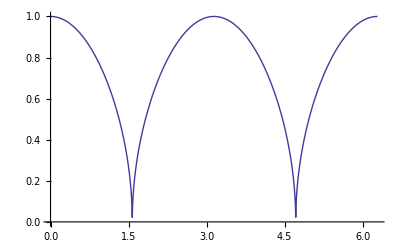
{-Graphics-,-Graphics-}

```mathematica
{Plot[Sqrt[Abs[Cos[t]]],{t,0,2π}],Plot[(Cos[t]^2)^(1/4),{t,0,2π}]}
```

```mathematica
parm=(2-2 Sin[t]+Sin[t] (Cos[t]^2)^(1/4)/(Sin[t]+7/5)) {Cos[t],Sin[t]};
assum=0<t<2π;
xform={Abs[x_]^(n_/;Mod[n,2]==0):>x^n};
```

#### VectorLength

```mathematica
Assuming[assum,FullSimplify[Norm[parm]/.xform]]
```

Abs[9+5 Cos[2 t]+(-4+5 √Abs[Cos[t]]) Sin[t]]/(7+5 Sin[t])

#### NormalVector

```mathematica
Assuming[assum,FullSimplify[NormalVector[parm,t]/.xform]]
```

{(64 Abs[Cos[t]]^(3/2) (7+5 Sin[t])^2 (-Cos[t]+Sin[2 t])-5 (10 Cos[t]+5 Cos[3 t]-15 Cos[5 t]+84 Sin[2 t]+70 Sin[4 t]))/(8 √2 Abs[Cos[t]]^(7/4) √(Sec[t]^2 (1000 Abs[Cos[t]]^(5/2) Sin[t]^3 (7+5 Sin[t])-64 Abs[Cos[t]]^(3/2) (-1+Sin[t]) (7+5 Sin[t])^4+50 √Abs[Cos[t]] (196 Cos[t]^4+Sin[t]^4 (7+5 Sin[t])^2)+5 (14 Cos[t]+5 Sin[2 t])^2 (-22-34 Cos[2 t]+41 Sin[t]+5 Sin[3 t])))),(√2 (70 Cos[t]^4+(7+5 Sin[t]) (-15 Cos[t]^2 Sin[t]^2-4 Abs[Cos[t]]^(7/2) (7+5 Sin[t])+4 Abs[Cos[t]]^(3/2) (-1+Sin[t]) Sin[t] (7+5 Sin[t]))))/(Abs[Cos[t]]^(7/4) √(Sec[t]^2 (1000 Abs[Cos[t]]^(5/2) Sin[t]^3 (7+5 Sin[t])-64 Abs[Cos[t]]^(3/2) (-1+Sin[t]) (7+5 Sin[t])^4+50 √Abs[Cos[t]] (196 Cos[t]^4+Sin[t]^4 (7+5 Sin[t])^2)+5 (14 Cos[t]+5 Sin[2 t])^2 (-22-34 Cos[2 t]+41 Sin[t]+5 Sin[3 t]))))}

#### TangentVector

```mathematica
Assuming[assum,FullSimplify[TangentVector[parm,t]/.xform]]
```

{(√2 (70 Cos[t]^4+(7+5 Sin[t]) (-15 Cos[t]^2 Sin[t]^2-4 Abs[Cos[t]]^(7/2) (7+5 Sin[t])+4 Abs[Cos[t]]^(3/2) (-1+Sin[t]) Sin[t] (7+5 Sin[t]))))/(Abs[Cos[t]]^(7/4) √(Sec[t]^2 (1000 Abs[Cos[t]]^(5/2) Sin[t]^3 (7+5 Sin[t])-64 Abs[Cos[t]]^(3/2) (-1+Sin[t]) (7+5 Sin[t])^4+50 √Abs[Cos[t]] (196 Cos[t]^4+Sin[t]^4 (7+5 Sin[t])^2)+5 (14 Cos[t]+5 Sin[2 t])^2 (-22-34 Cos[2 t]+41 Sin[t]+5 Sin[3 t])))),(64 Abs[Cos[t]]^(3/2) (7+5 Sin[t])^2 (Cos[t]-Sin[2 t])+5 (10 Cos[t]+5 Cos[3 t]-15 Cos[5 t]+84 Sin[2 t]+70 Sin[4 t]))/(8 √2 Abs[Cos[t]]^(7/4) √(Sec[t]^2 (1000 Abs[Cos[t]]^(5/2) Sin[t]^3 (7+5 Sin[t])-64 Abs[Cos[t]]^(3/2) (-1+Sin[t]) (7+5 Sin[t])^4+50 √Abs[Cos[t]] (196 Cos[t]^4+Sin[t]^4 (7+5 Sin[t])^2)+5 (14 Cos[t]+5 Sin[2 t])^2 (-22-34 Cos[2 t]+41 Sin[t]+5 Sin[3 t]))))}

## HeartCurve5

### Equation

```mathematica
par[x_]:={16 Sin[x]^3,13 Cos[x]-5 Cos[2 x]-2 Cos[3 x]-Cos[4 x]}
```

```mathematica
Solve[And@@Thread[{x,y}==par[t]],{x,y},t]
```

{{}}

```mathematica
FullSimplify[12 Sin[x]-4 Sin[3 x]]
```

16 Sin[x]^3

### Plot

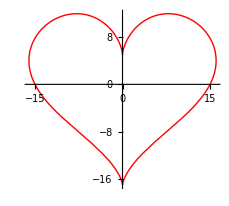

```mathematica
ParametricPlot[{16 Sin[x]^3,13 Cos[x]-5 Cos[2 x]-2 Cos[3 x]-Cos[4 x]},{x,-Pi,Pi},PlotStyle->Red]
```

```mathematica
ParametricPlot[{12 Sin[x]-4 Sin[3 x],13 Cos[x]-5 Cos[2 x]-2 Cos[3 x]-Cos[4 x]},{x,0,Pi},PlotStyle->Red]
```

-Graphics-

### Equations

#### Cartesian

```mathematica
Thread[{x,y}-par[t]]
```

{x-12 Sin[t]+4 Sin[3 t],y-13 Cos[t]+5 Cos[2 t]+2 Cos[3 t]+Cos[4 t]}

```mathematica
eq=Numerator[Factor[Thread[{x,y}-par[t]]]]
```

{x-12 Sin[t]+4 Sin[3 t],y-13 Cos[t]+5 Cos[2 t]+2 Cos[3 t]+Cos[4 t]}

```mathematica
eq2=TrigExpand[eq]
```

{x-12 Sin[t]+12 Cos[t]^2 Sin[t]-4 Sin[t]^3,y-13 Cos[t]+5 Cos[t]^2+2 Cos[t]^3+Cos[t]^4-5 Sin[t]^2-6 Cos[t] Sin[t]^2-6 Cos[t]^2 Sin[t]^2+Sin[t]^4}

```mathematica
eq3=eq2/.{Cos[t]->(1-s^2)/(1+s^2),Sin[t]->2 s/(1+s^2)};
```

```mathematica
eq4=Factor[Together[eq3]]
```

{(-128 s^3+x+3 s^2 x+3 s^4 x+s^6 x)/((1+s^2)^3),(-5-102 s^2+20 s^4+6 s^6+17 s^8+y+4 s^2 y+6 s^4 y+4 s^6 y+s^8 y)/((1+s^2)^4)}

```mathematica
eq5=Numerator[eq4]
```

{-128 s^3+x+3 s^2 x+3 s^4 x+s^6 x,-5-102 s^2+20 s^4+6 s^6+17 s^8+y+4 s^2 y+6 s^4 y+4 s^6 y+s^8 y}

```mathematica
curve=Factor[GroebnerBasis[eq5,{x,y},s]]
```

{-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6}

```mathematica
xy=-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6;
```

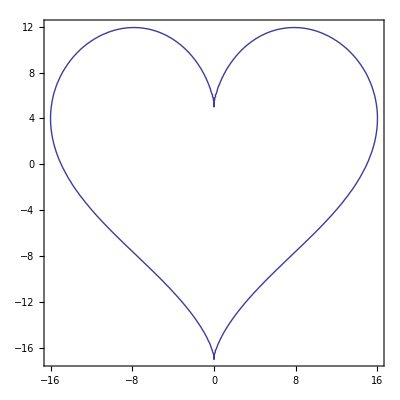

```mathematica
ContourPlot[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6==0,{x,-16,16},{y,-17,12}]
```

```mathematica
AlgebraicDegree[curve[[1]],{x,y}]
```

8

#### Polar

```mathematica
ArcTan[1/Divide@@par[t]]//FullSimplify
```

-ArcTan[1/16 (-13 Cos[t]+5 Cos[2 t]+2 Cos[3 t]+Cos[4 t]) Csc[t]^3]

```mathematica
Thread[{r Cos[q],r Sin[q]}-par[t]]
```

{r Cos[q]-12 Sin[t]+4 Sin[3 t],-13 Cos[t]+5 Cos[2 t]+2 Cos[3 t]+Cos[4 t]+r Sin[q]}

```mathematica
eq=Numerator[Factor[%]]
```

{r Cos[q]-12 Sin[t]+4 Sin[3 t],-13 Cos[t]+5 Cos[2 t]+2 Cos[3 t]+Cos[4 t]+r Sin[q]}

```mathematica
eq2=TrigExpand[eq]
```

{r Cos[q]-12 Sin[t]+12 Cos[t]^2 Sin[t]-4 Sin[t]^3,-13 Cos[t]+5 Cos[t]^2+2 Cos[t]^3+Cos[t]^4+r Sin[q]-5 Sin[t]^2-6 Cos[t] Sin[t]^2-6 Cos[t]^2 Sin[t]^2+Sin[t]^4}

```mathematica
eq3=TrigExpand[{eq,r^2-par[t].par[t]}]/.{Cos[t]->(1-s^2)/(1+s^2),Sin[t]->2 s/(1+s^2)};
```

```mathematica
eq4=Factor[Together[eq3]]
```

{{(-128 s^3+r Cos[q]+3 r s^2 Cos[q]+3 r s^4 Cos[q]+r s^6 Cos[q])/((1+s^2)^3),1/((1+s^2)^4)(-5-102 s^2+20 s^4+6 s^6+17 s^8+r Sin[q]+4 r s^2 Sin[q]+6 r s^4 Sin[q]+4 r s^6 Sin[q]+r s^8 Sin[q])},1/((1+s^2)^8)(-25+r^2-1020 s^2+8 r^2 s^2-10204 s^4+28 r^2 s^4-12244 s^6+56 r^2 s^6-31774 s^8+70 r^2 s^8-13156 s^10+56 r^2 s^10-716 s^12+28 r^2 s^12-204 s^14+8 r^2 s^14-289 s^16+r^2 s^16)}

```mathematica
eq5=Numerator[eq4]
```

{{-128 s^3+r Cos[q]+3 r s^2 Cos[q]+3 r s^4 Cos[q]+r s^6 Cos[q],-5-102 s^2+20 s^4+6 s^6+17 s^8+r Sin[q]+4 r s^2 Sin[q]+6 r s^4 Sin[q]+4 r s^6 Sin[q]+r s^8 Sin[q]},-25+r^2-1020 s^2+8 r^2 s^2-10204 s^4+28 r^2 s^4-12244 s^6+56 r^2 s^6-31774 s^8+70 r^2 s^8-13156 s^10+56 r^2 s^10-716 s^12+28 r^2 s^12-204 s^14+8 r^2 s^14-289 s^16+r^2 s^16}

```mathematica
curve=Factor[GroebnerBasis[eq5,{r},{s,q}]]
```

{-1+Cos[q]^2+Sin[q]^2,-10061824000-3937380544 r^2+15918304 r^4+8116 r^6+r^8+4261478400 r Sin[q]-471039744 r^3 Sin[q]+597312 r^5 Sin[q]+240 r^7 Sin[q]+3690883264 r^2 Sin[q]^2-25754816 r^4 Sin[q]^2+46116 r^6 Sin[q]^2-4 r^8 Sin[q]^2+399081216 r^3 Sin[q]^3+624000 r^5 Sin[q]^3-464 r^7 Sin[q]^3+12736480 r^4 Sin[q]^4-48996 r^6 Sin[q]^4+6 r^8 Sin[q]^4-631488 r^5 Sin[q]^5+208 r^7 Sin[q]^5+11148 r^6 Sin[q]^6-4 r^8 Sin[q]^6+16 r^7 Sin[q]^7+r^8 Sin[q]^8}

```mathematica
Solve[-10061824000-3937380544 r^2+15918304 r^4+8116 r^6+r^8+4261478400 r Sin[q]-471039744 r^3 Sin[q]+597312 r^5 Sin[q]+240 r^7 Sin[q]+3690883264 r^2 Sin[q]^2-25754816 r^4 Sin[q]^2+46116 r^6 Sin[q]^2-4 r^8 Sin[q]^2+399081216 r^3 Sin[q]^3+624000 r^5 Sin[q]^3-464 r^7 Sin[q]^3+12736480 r^4 Sin[q]^4-48996 r^6 Sin[q]^4+6 r^8 Sin[q]^4-631488 r^5 Sin[q]^5+208 r^7 Sin[q]^5+11148 r^6 Sin[q]^6-4 r^8 Sin[q]^6+16 r^7 Sin[q]^7+r^8 Sin[q]^8==0,r]
```

{{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,1]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,2]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,3]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,4]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,5]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,6]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,7]},{r→Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,8]}}

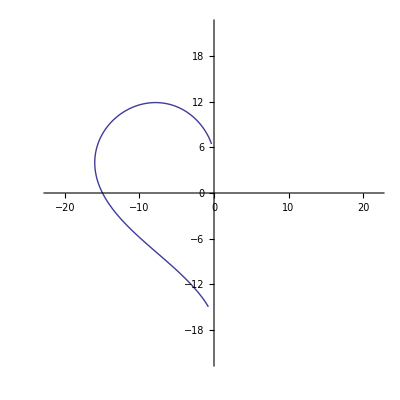

```mathematica
PolarPlot[Root[-1287913472000+545469235200 Sin[q] #1+(-267768180736-236216528896 Cos[2 q]) #1^2+(-21981290496 Sin[q]-12770598912 Sin[3 q]) #1^3+(1000585728+833173504 Cos[2 q]+203783680 Cos[4 q]) #1^4+(85840896 Sin[q]+5291520 Sin[3 q]-5051904 Sin[5 q]) #1^5+(2084384-484560 Cos[2 q]-516384 Cos[4 q]-44592 Cos[6 q]) #1^6+(3936 Sin[q]+5856 Sin[3 q]+1888 Sin[5 q]-32 Sin[7 q]) #1^7+(35+56 Cos[2 q]+28 Cos[4 q]+8 Cos[6 q]+Cos[8 q]) #1^8&,1],{q,-1.52,1.52},WorkingPrecision->20,PlotRange->All]
```

```mathematica
curve={12 Sin[x]-4 Sin[3 x],13 Cos[x]-5 Cos[2 x]-2 Cos[3 x]-Cos[4 x]}
```

{12 Sin[x]-4 Sin[3 x],13 Cos[x]-5 Cos[2 x]-2 Cos[3 x]-Cos[4 x]}

### Arc Length

```mathematica
FullSimplify[#.#&[D[par[t],t]]]
```

2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2

```mathematica
NIntegrate[Sqrt[2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2],{t,-π,π}]
```

102.168

```mathematica
2ArcLength[par[t],{t,0,π}]//Timing
```

{72.3609,2 ∫_0^π √((12 Cos[t]-12 Cos[3 t])^2+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2)ⅆt}

```mathematica
TrigExpand[2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2]//Factor
```

1/2 (609-92 Cos[t]-389 Cos[t]^2+156 Cos[t]^3-232 Cos[t]^4-16 Cos[t]^5+28 Cos[t]^6-48 Cos[t]^7-16 Cos[t]^8+389 Sin[t]^2-468 Cos[t] Sin[t]^2+1392 Cos[t]^2 Sin[t]^2+160 Cos[t]^3 Sin[t]^2-420 Cos[t]^4 Sin[t]^2+1008 Cos[t]^5 Sin[t]^2+448 Cos[t]^6 Sin[t]^2-232 Sin[t]^4-80 Cos[t] Sin[t]^4+420 Cos[t]^2 Sin[t]^4-1680 Cos[t]^3 Sin[t]^4-1120 Cos[t]^4 Sin[t]^4-28 Sin[t]^6+336 Cos[t] Sin[t]^6+448 Cos[t]^2 Sin[t]^6-16 Sin[t]^8)

```mathematica
NIntegrate[Sqrt[1/2 (609-92 Cos[t]-389 Cos[t]^2+156 Cos[t]^3-232 Cos[t]^4-16 Cos[t]^5+28 Cos[t]^6-48 Cos[t]^7-16 Cos[t]^8+389 Sin[t]^2-468 Cos[t] Sin[t]^2+1392 Cos[t]^2 Sin[t]^2+160 Cos[t]^3 Sin[t]^2-420 Cos[t]^4 Sin[t]^2+1008 Cos[t]^5 Sin[t]^2+448 Cos[t]^6 Sin[t]^2-232 Sin[t]^4-80 Cos[t] Sin[t]^4+420 Cos[t]^2 Sin[t]^4-1680 Cos[t]^3 Sin[t]^4-1120 Cos[t]^4 Sin[t]^4-28 Sin[t]^6+336 Cos[t] Sin[t]^6+448 Cos[t]^2 Sin[t]^6-16 Sin[t]^8)],{t,-π,π}]
```

102.168

```mathematica
2Integrate[Sqrt[1/2 (609-92 Cos[t]-389 Cos[t]^2+156 Cos[t]^3-232 Cos[t]^4-16 Cos[t]^5+28 Cos[t]^6-48 Cos[t]^7-16 Cos[t]^8+389 Sin[t]^2-468 Cos[t] Sin[t]^2+1392 Cos[t]^2 Sin[t]^2+160 Cos[t]^3 Sin[t]^2-420 Cos[t]^4 Sin[t]^2+1008 Cos[t]^5 Sin[t]^2+448 Cos[t]^6 Sin[t]^2-232 Sin[t]^4-80 Cos[t] Sin[t]^4+420 Cos[t]^2 Sin[t]^4-1680 Cos[t]^3 Sin[t]^4-1120 Cos[t]^4 Sin[t]^4-28 Sin[t]^6+336 Cos[t] Sin[t]^6+448 Cos[t]^2 Sin[t]^6-16 Sin[t]^8)],{t,0,π}]//Timing
```

$Aborted

### Arc Length Function

```mathematica
2ArcLength[par[t],t]//Timing
```

2 ∫_0^t √((12 Cos[t]-12 Cos[3 t])^2+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2)ⅆt

### Area

```mathematica
area[{f_,g_},{t_,t0_,t1_},assum___?OptionQ]:=integrate[f D[g,t]-g D[f,t],{t,t0,t1},assum]/2
```

```mathematica
2FullSimplify[area[par[t],{t,0,π}],0<t<π]
```

integrate[-8 (52-25 Cos[t]+14 Cos[2 t]-12 Cos[3 t]+Cos[5 t]) Sin[t]^2,{t,0,π}]

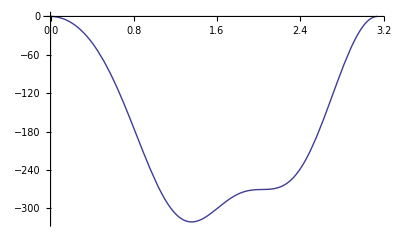

```mathematica
Plot[-8 (52-25 Cos[t]+14 Cos[2 t]-12 Cos[3 t]+Cos[5 t]) Sin[t]^2,{t,0,π}]
```

```mathematica
-NIntegrate[-8 (52-25 Cos[t]+14 Cos[2 t]-12 Cos[3 t]+Cos[5 t]) Sin[t]^2,{t,0,π}]
```

565.487

#### Parametric

```mathematica
-2Area[par[t],{t,0,π}]//Timing
```

{0.803449,180 π}

#### Inequality

```mathematica
N[%]
```

{0.803449,565.487}

```mathematica
NIntegrate[Boole[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6<0],{x,-20,20},{y,-20,20}]//Timing
```

{1.4141,565.487}

```mathematica
Integrate[Boole[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6<0],{x,-∞,∞},{y,-∞,∞}]//FullSimplify//Timing
```

{0.220497,∫_-16^16 (-Root[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+(4261478400-471039744 x^2+597312 x^4+240 x^6) #1+(-246497280+6081792 x^2+70464 x^4) #1^2+(-71958528+1818624 x^2+256 x^4) #1^3+(2899968+67584 x^2) #1^4+589824 #1^5+16384 #1^6&,1]+Root[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+(4261478400-471039744 x^2+597312 x^4+240 x^6) #1+(-246497280+6081792 x^2+70464 x^4) #1^2+(-71958528+1818624 x^2+256 x^4) #1^3+(2899968+67584 x^2) #1^4+589824 #1^5+16384 #1^6&,2])ⅆx}

```mathematica
Integrate[Boole[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6<0],{y,-∞,∞},{x,-∞,∞}]//FullSimplify//Timing
```

{0.788624,∫_-17^5 (-Root[-10061824000+4261478400 y-246497280 y^2-71958528 y^3+2899968 y^4+589824 y^5+16384 y^6+(-3937380544-471039744 y+6081792 y^2+1818624 y^3+67584 y^4) #1^2+(15918304+597312 y+70464 y^2+256 y^3) #1^4+(8116+240 y) #1^6+#1^8&,1]+Root[-10061824000+4261478400 y-246497280 y^2-71958528 y^3+2899968 y^4+589824 y^5+16384 y^6+(-3937380544-471039744 y+6081792 y^2+1818624 y^3+67584 y^4) #1^2+(15918304+597312 y+70464 y^2+256 y^3) #1^4+(8116+240 y) #1^6+#1^8&,2])ⅆy+∫_5^Root[-3558199-48432 #1+4672 #1^2+2048 #1^3&,1] (-Root[-10061824000+4261478400 y-246497280 y^2-71958528 y^3+2899968 y^4+589824 y^5+16384 y^6+(-3937380544-471039744 y+6081792 y^2+1818624 y^3+67584 y^4) #1^2+(15918304+597312 y+70464 y^2+256 y^3) #1^4+(8116+240 y) #1^6+#1^8&,1]+Root[-10061824000+4261478400 y-246497280 y^2-71958528 y^3+2899968 y^4+589824 y^5+16384 y^6+(-3937380544-471039744 y+6081792 y^2+1818624 y^3+67584 y^4) #1^2+(15918304+597312 y+70464 y^2+256 y^3) #1^4+(8116+240 y) #1^6+#1^8&,2])ⅆy+∫_5^Root[-3558199-48432 #1+4672 #1^2+2048 #1^3&,1] (-Root[-10061824000+4261478400 y-246497280 y^2-71958528 y^3+2899968 y^4+589824 y^5+16384 y^6+(-3937380544-471039744 y+6081792 y^2+1818624 y^3+67584 y^4) #1^2+(15918304+597312 y+70464 y^2+256 y^3) #1^4+(8116+240 y) #1^6+#1^8&,3]+Root[-10061824000+4261478400 y-246497280 y^2-71958528 y^3+2899968 y^4+589824 y^5+16384 y^6+(-3937380544-471039744 y+6081792 y^2+1818624 y^3+67584 y^4) #1^2+(15918304+597312 y+70464 y^2+256 y^3) #1^4+(8116+240 y) #1^6+#1^8&,4])ⅆy}

### Curvature

```mathematica
κ=FullSimplify[Curvature[par[t],t],-π<t<π]
```

-(48 (12+31 Cos[t]-7 Cos[2 t]+7 Cos[3 t]-2 Cos[5 t]) Sin[t]^2)/((2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2)^(3/2))

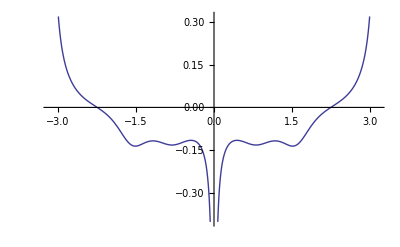

```mathematica
Plot[κ,{t,-π,π}]
```

#### Implicit

```mathematica
κs=Curvature[xy,{x,y}];//Timing
```

{25.985,Null}

```mathematica
ByteCount/@κs
```

{19800,241720,247216}

```mathematica
κs[[1]]
```

((-492994560+12163584 x^2+140928 x^4-431751168 y+10911744 x^2 y+1536 x^4 y+34799616 y^2+811008 x^2 y^2+11796480 y^3+491520 y^4) (-7874761088 x+63673216 x^3+48696 x^5+8 x^7-942079488 x y+2389248 x^3 y+1440 x^5 y+12163584 x y^2+281856 x^3 y^2+3637248 x y^3+1024 x^3 y^3+135168 x y^4)^2-2 (-942079488 x+2389248 x^3+1440 x^5+24327168 x y+563712 x^3 y+10911744 x y^2+3072 x^3 y^2+540672 x y^3) (-7874761088 x+63673216 x^3+48696 x^5+8 x^7-942079488 x y+2389248 x^3 y+1440 x^5 y+12163584 x y^2+281856 x^3 y^2+3637248 x y^3+1024 x^3 y^3+135168 x y^4) (4261478400-471039744 x^2+597312 x^4+240 x^6-492994560 y+12163584 x^2 y+140928 x^4 y-215875584 y^2+5455872 x^2 y^2+768 x^4 y^2+11599872 y^3+270336 x^2 y^3+2949120 y^4+98304 y^5)+(-7874761088+191019648 x^2+243480 x^4+56 x^6-942079488 y+7167744 x^2 y+7200 x^4 y+12163584 y^2+845568 x^2 y^2+3637248 y^3+3072 x^2 y^3+135168 y^4) (4261478400-471039744 x^2+597312 x^4+240 x^6-492994560 y+12163584 x^2 y+140928 x^4 y-215875584 y^2+5455872 x^2 y^2+768 x^4 y^2+11599872 y^3+270336 x^2 y^3+2949120 y^4+98304 y^5)^2)/((-7874761088 x+63673216 x^3+48696 x^5+8 x^7-942079488 x y+2389248 x^3 y+1440 x^5 y+12163584 x y^2+281856 x^3 y^2+3637248 x y^3+1024 x^3 y^3+135168 x y^4)^2+(4261478400-471039744 x^2+597312 x^4+240 x^6-492994560 y+12163584 x^2 y+140928 x^4 y-215875584 y^2+5455872 x^2 y^2+768 x^4 y^2+11599872 y^3+270336 x^2 y^3+2949120 y^4+98304 y^5)^2)^(3/2)

```mathematica
FullSimplify[κs[[1]]]
```

(12 (-12 x^2 (15 x^4+8 x^2 (3111+734 y+4 y^2)+16 (-613333+2 y (7919+16 y (222+11 y)))) (5 x^6+2048 (-5+y)^2 (6+y) (17+y)^2+4 x^4 (3111+734 y+4 y^2)+16 x^2 (-613333+2 y (7919+16 y (222+11 y)))) (x^6+3 x^4 (2029+60 y)+16 x^2 (497447+2 y (9333+y (1101+4 y)))+16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y)))))+4 x^2 (x^4 (367+4 y)+256 (-5+y) (17+y) (59+5 y (12+y))+4 x^2 (7919+48 y (148+11 y))) (x^6+3 x^4 (2029+60 y)+16 x^2 (497447+2 y (9333+y (1101+4 y)))+16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y)))))^2+3 (5 x^6+2048 (-5+y)^2 (6+y) (17+y)^2+4 x^4 (3111+734 y+4 y^2)+16 x^2 (-613333+2 y (7919+16 y (222+11 y))))^2 (7 x^6+15 x^4 (2029+60 y)+48 x^2 (497447+2 y (9333+y (1101+4 y)))+16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y)))))))/(36 (5 x^6+2048 (-5+y)^2 (6+y) (17+y)^2+4 x^4 (3111+734 y+4 y^2)+16 x^2 (-613333+2 y (7919+16 y (222+11 y))))^2+x^2 (x^6+3 x^4 (2029+60 y)+16 x^2 (497447+2 y (9333+y (1101+4 y)))+16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y)))))^2)^(3/2)

```mathematica
ByteCount[%]
```

17048

```mathematica
Factor[κs[[1]]]
```

(12 (-23275915001768045445120000-9556799576701228604456960 x^2+1035067655084314943856640 x^4-6867252419279887322112 x^6+3395099020105349120 x^8+89024840135250304 x^10+122175970938000 x^12+62392551332 x^14+13682501 x^16+1093 x^18+2600845581177109610496000 y-5545125047775301418876928 x^2 y+289503056074040066899968 x^4 y-3137700784073295982592 x^6 y+7900837856104752128 x^8 y+9430687197745408 x^10 y+7055604254080 x^12 y+2920979968 x^14 y+478188 x^16 y+16 x^18 y+2726911535089095750451200 y^2-399356222585855565889536 x^2 y^2+17303486944696816238592 x^4 y^2-376381211130691264512 x^6 y^2+928198578515112960 x^8 y^2+1001150074896384 x^10 y^2+701346360960 x^12 y^2+191622720 x^14 y^2+12768 x^16 y^2-152243153741910544220160 y^3+180938278735205892096000 x^2 y^3-2798977960516425613312 x^4 y^3-5299854343169458176 x^6 y^3+78787148953989120 x^8 y^3+52595577808896 x^10 y^3+22117853696 x^12 y^3+4216576 x^14 y^3-130332409238588586196992 y^4+35520387759988884635648 x^2 y^4-418096303736067719168 x^4 y^4+1603221292376637440 x^6 y^4+4609881624518656 x^8 y^4+2287544230912 x^10 y^4+1007595264 x^12 y^4+8448 x^14 y^4-594526187160348917760 y^5+1681319675812056662016 x^2 y^5-13674421937267539968 x^4 y^5+144970652652404736 x^6 y^5+150235835547648 x^8 y^5+89309958144 x^10 y^5+5041152 x^12 y^5+2937849620262121635840 y^6-109257905190708707328 x^2 y^6+688913729131118592 x^4 y^6+7208737571602432 x^6 y^6+6879007195136 x^8 y^6+1304780800 x^10 y^6+184716060234583375872 y^7-13979934056654045184 x^2 y^7+95362599129972736 x^4 y^7+293612484296704 x^6 y^7+124938289152 x^8 y^7+1671168 x^10 y^7-23363384225367588864 y^8-289455638889627648 x^2 y^8+6392322277244928 x^4 y^8+9565768777728 x^6 y^8+675938304 x^8 y^8-3262241385058664448 y^9+35427600952197120 x^2 y^9+281355661344768 x^4 y^9+87753228288 x^6 y^9-91364787971162112 y^10+3230770567053312 x^2 y^10+6360800428032 x^4 y^10+146800640 x^6 y^10+6736546413674496 y^11+120159360516096 x^2 y^11+32363249664 x^4 y^11+603900050669568 y^12+1912199970816 x^2 y^12+18476949307392 y^13+4831838208 x^2 y^13+212600881152 y^14))/(283753096151040000+906206418810685696 x^2-12122709728273920 x^4+42604216099936 x^6+96967940992 x^8+57449713 x^10+13074 x^12+x^14-65652677148672000 y+240709555491366912 x^2 y-2631982166897664 x^4 y+1115012256768 x^6 y+8987401920 x^8 y+3845592 x^10 y+360 x^12 y-24950853756518400 y^2+14590970082613248 x^2 y^2-199594401358848 x^4 y^2+768629159808 x^6 y^2+905049408 x^8 y^2+108624 x^10 y^2+4870565391237120 y^3-1554032116654080 x^2 y^3-3055820296192 x^4 y^3+58617059840 x^6 y^3+20560896 x^8 y^3+256 x^10 y^3+942189727186944 y^4-218004265512960 x^2 y^4+1286330683392 x^4 y^4+3030736896 x^6 y^4+89088 x^8 y^4-110597152702464 y^5-2768805494784 x^2 y^5+103710769152 x^4 y^5+22327296 x^6 y^5-19307119509504 y^6+896266469376 x^2 y^6+2952560640 x^4 y^6+16384 x^6 y^6+405874409472 y^7+57038340096 x^2 y^7+6684672 x^4 y^7+171530256384 y^8+1115947008 x^2 y^8+9059696640 y^9+150994944 y^10)^(3/2)

```mathematica
ByteCount[%]
```

31560

### Inflection Points

```mathematica
Numerator[κ]
```

-48 (12+31 Cos[t]-7 Cos[2 t]+7 Cos[3 t]-2 Cos[5 t]) Sin[t]^2

```mathematica
expr=-5 Abs[t]^(13/10) (4 t Cos[t]^4 (120+(21+50 t^2) Log[t^2])-8 Cos[t]^3 (9+50 t^2+45 t^2 Log[t^2]) Sin[t]-40 t^2 Cos[t] (-25+3 Log[t^2]) Sin[t]^3-100 t^3 Log[t^2] Sin[t]^4+t (40+7 (-3+25 t^2) Log[t^2]) Sin[2 t]^2);
```

```mathematica
FindInstance[Numerator[κ]==0&&2.2<t<2.4,t]
```

{{t→Root[{-12 Sin[#1]^2-31 Cos[#1] Sin[#1]^2+7 Cos[2 #1] Sin[#1]^2-7 Cos[3 #1] Sin[#1]^2+2 Cos[5 #1] Sin[#1]^2&,2.24560121313071796840053215968}]}}

```mathematica
FullSimplify[%]
```

{{t→Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.24560121313071796840053215968}]}}

```mathematica
i=InflectionPoints[par[t],t]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{0,5},{0,-17},{0,-17},{16 ⅈ (-1+Root[-19+14 #1^2-68 #1^3+32 #1^5&,1]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,1]},{-16 ⅈ (-1+Root[-19+14 #1^2-68 #1^3+32 #1^5&,1]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,1]},{-16 (1-Root[-19+14 #1^2-68 #1^3+32 #1^5&,2]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,3]},{16 (1-Root[-19+14 #1^2-68 #1^3+32 #1^5&,2]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,3]},{16 ⅈ (-1+Root[-19+14 #1^2-68 #1^3+32 #1^5&,3]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,2]},{-16 ⅈ (-1+Root[-19+14 #1^2-68 #1^3+32 #1^5&,3]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,2]},{-16 (1-Root[-19+14 #1^2-68 #1^3+32 #1^5&,4]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,4]},{16 (1-Root[-19+14 #1^2-68 #1^3+32 #1^5&,4]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,4]},{-16 (1-Root[-19+14 #1^2-68 #1^3+32 #1^5&,5]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,5]},{16 (1-Root[-19+14 #1^2-68 #1^3+32 #1^5&,5]^2)^(3/2),Root[813937087+79430692 #1-3950838 #1^2-40652 #1^3+12864 #1^4+256 #1^5&,5]}}

```mathematica
N[%]
```

{{0.,5.},{0.,-17.},{0.,-17.},{0.+22.0989 ⅈ,-42.2431},{0.-22.0989 ⅈ,-42.2431},{-7.61706,-7.91874},{7.61706,-7.91874},{0.+16.5722 ⅈ,-28.8124},{0.-16.5722 ⅈ,-28.8124},{-20.2272-10.5191 ⅈ,14.3621-11.1181 ⅈ},{20.2272+10.5191 ⅈ,14.3621-11.1181 ⅈ},{-20.2272+10.5191 ⅈ,14.3621+11.1181 ⅈ},{20.2272-10.5191 ⅈ,14.3621+11.1181 ⅈ}}

```mathematica
par[t]/.t->Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.2456012131307179684005321596772741194671173211545697112794`30.}]//FullSimplify
```

{16 Sin[Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.24560121313071796840053215968}]]^3,13 Cos[Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.24560121313071796840053215968}]]-5 Cos[2 Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.24560121313071796840053215968}]]-2 Cos[3 Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.24560121313071796840053215968}]]-Cos[4 Root[{(-12-31 Cos[#1]+7 Cos[2 #1]-7 Cos[3 #1]+2 Cos[5 #1]) Sin[#1]^2&,2.24560121313071796840053215968}]]}

### Singular Points

```mathematica
par/@{-π,0,π}
```

{{0,-17},{0,5},{0,-17}}

```mathematica
N[%]
```

{{0.,-17.},{0.,5.},{0.,-17.}}

```mathematica
Limit[par[t],t->0]
```

{0,5}

### Slope

```mathematica
Slope[{16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]},t]//FullSimplify
```

1/48 (-7+28 Cos[t]+12 Cos[2 t]+8 Cos[3 t]) Csc[t] Sec[t]

```mathematica
Slope[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6==0,{x,y}]//FullSimplify
```

(x (-x^6-3 x^4 (2029+60 y)-16 x^2 (497447+2 y (9333+y (1101+4 y)))-16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y))))))/(6 (5 x^6+2048 (-5+y)^2 (6+y) (17+y)^2+4 x^4 (3111+734 y+4 y^2)+16 x^2 (-613333+2 y (7919+16 y (222+11 y)))))

```mathematica
Slope[-10061824000-3937380544 x^2+15918304 x^4+8116 x^6+x^8+4261478400 y-471039744 x^2 y+597312 x^4 y+240 x^6 y-246497280 y^2+6081792 x^2 y^2+70464 x^4 y^2-71958528 y^3+1818624 x^2 y^3+256 x^4 y^3+2899968 y^4+67584 x^2 y^4+589824 y^5+16384 y^6==0,{x,y}]//FullSimplify
```

{(x (-x^6-3 x^4 (2029+60 y)-16 x^2 (497447+2 y (9333+y (1101+4 y)))-16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y))))))/(6 (5 x^6+2048 (-5+y)^2 (6+y) (17+y)^2+4 x^4 (3111+734 y+4 y^2)+16 x^2 (-613333+2 y (7919+16 y (222+11 y))))),(x (-x^6-3 x^4 (2029+60 y)-16 x^2 (497447+2 y (9333+y (1101+4 y)))-16 (-61521571+12 y (-613333+y (7919+8 y (296+11 y))))))/(6 (5 x^6+2048 (-5+y)^2 (6+y) (17+y)^2+4 x^4 (3111+734 y+4 y^2)+16 x^2 (-613333+2 y (7919+16 y (222+11 y)))))}

### SpecialAffineCurvature

```mathematica
ByteCount[k=SpecialAffineCurvature[{16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]},t]]//Timing
```

{0.001,26064}

```mathematica
ByteCount[k2=FullSimplify[k,0<t<2π]]//Timing
```

{4.01039,3760}

```mathematica
k2
```

((46818+79780 Cos[t]-3103 Cos[2 t]-81852 Cos[3 t]+8326 Cos[4 t]+18644 Cos[5 t]-6089 Cos[6 t]-5752 Cos[7 t]-3268 Cos[8 t]+700 Cos[9 t]-452 Cos[10 t]+40 Cos[12 t]) Sin[t]^2)/(288 6^(2/3) ((-12-31 Cos[t]+7 Cos[2 t]-7 Cos[3 t]+2 Cos[5 t]) Sin[t]^2)^(8/3))

### Tangential Angle

```mathematica
TangentialAngle[par[t],t]
```

-ArcTan[(24 Sin[2 t])/(-7+28 Cos[t]+12 Cos[2 t]+8 Cos[3 t])]

### Vector Properties

```mathematica
parm={16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]};
assum=-π<t<π;
xform={Abs[x_]^(n_/;Mod[n,2]==0):>x^n};
```

#### VectorLength

```mathematica
Assuming[assum,FullSimplify[Norm[parm]/.xform]]
```

√((-13 Cos[t]+5 Cos[2 t]+2 Cos[3 t]+Cos[4 t])^2+256 Sin[t]^6)

#### NormalVector

```mathematica
Assuming[assum,FullSimplify[NormalVector[parm,t]/.xform]]
```

{(13 Sin[t]-2 (5 Sin[2 t]+3 Sin[3 t]+2 Sin[4 t]))/(√(2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2)),(48 Cos[t] Sin[t]^2)/(√(2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2))}

#### TangentVector

```mathematica
Assuming[assum,FullSimplify[TangentVector[parm,t]/.xform]]
```

{(48 Cos[t] Sin[t]^2)/(√(2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2)),(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])/(√(2304 Cos[t]^2 Sin[t]^4+(-13 Sin[t]+10 Sin[2 t]+6 Sin[3 t]+4 Sin[4 t])^2))}

## HeartCurve6

From Judith Schroeder
October 16, 2021

Original:

```mathematica
x^2+(y-(x^2)^(1/3))^2==1
```

Nondimensionalized:

```mathematica
(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1
```

```mathematica
(x^2)^(1/3)/.x->-1
```

1

```mathematica
x^(2/3)/.x->-1
```

(-1)^(2/3)

```mathematica
cartesian=(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1;
```

```mathematica
reg=ImplicitRegion[x^2+(y-(x^2)^(1/3))^2<=1,{x,y}];
```

```mathematica
xy=-a^6 b^6+3 a^4 b^6 x^2-2 a^2 b^6 x^4+b^6 x^6-6 a^4 b^5 x^2 y+6 a^2 b^5 x^4 y+3 a^6 b^4 y^2-6 a^4 b^4 x^2 y^2+3 a^2 b^4 x^4 y^2-2 a^4 b^3 x^2 y^3-3 a^6 b^2 y^4+3 a^4 b^2 x^2 y^4+a^6 y^6==0;
```

### Bounds

```mathematica
x^2+(y-(x^2)^(1/3))^2==1
```

```mathematica
(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1
```

```mathematica
Assuming[a>0&&b>0,Simplify@Minimize[{x,(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1},{x,y}]]
```

{-a,{x→-a,y→Root[b^6-2 b^3 #1^3+#1^6&,1]}}

```mathematica
Assuming[a>0&&b>0,Simplify@Maximize[{x,(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1},{x,y}]]
```

{a,{x→a,y→Root[b^6-2 b^3 #1^3+#1^6&,1]}}

```mathematica
Assuming[a>0&&b>0,Simplify@Minimize[{y,(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1},{x,y}]]
```

{-b,{x→0,y→-b}}

```mathematica
Assuming[a>0&&b>0,Simplify@Maximize[{y,(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1},{x,y}]]
```

{-Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1],{x→Root[-a^6 b^6+3 a^6 b^4 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^2-3 a^6 b^2 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^4+a^6 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^6+(3 a^4 b^6+6 a^4 b^5 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]-6 a^4 b^4 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^2+2 a^4 b^3 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^3+3 a^4 b^2 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^4) #1^2+(-2 a^2 b^6-6 a^2 b^5 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]+3 a^2 b^4 Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]^2) #1^4+b^6 #1^6&,1],y→-Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]}}

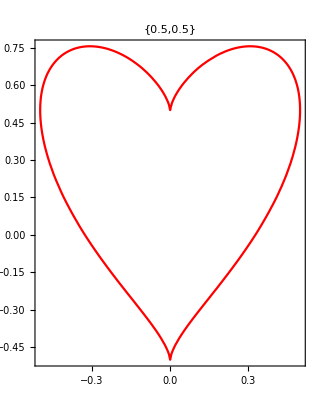
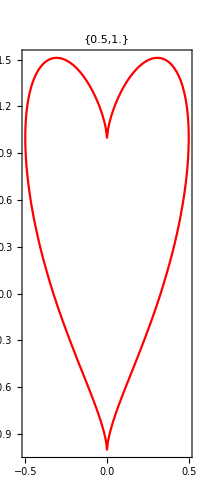
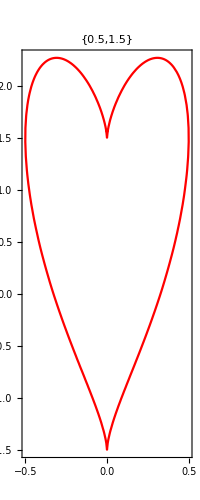
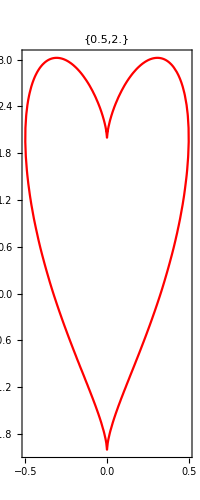
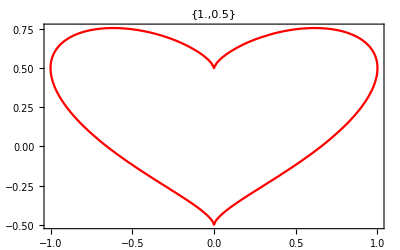
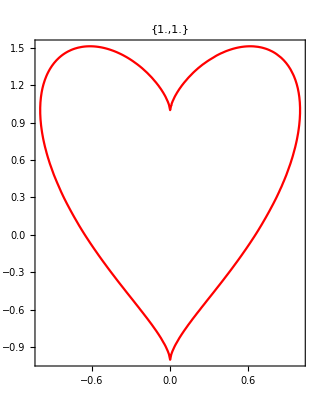
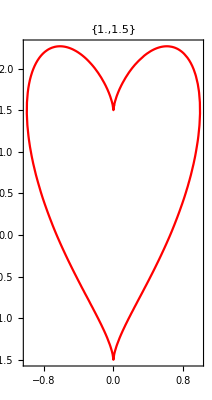
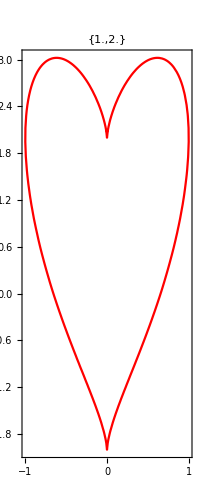

```mathematica
Table[ContourPlot[(x/a)^2+(y/b-((x/a)^2)^(1/3))^2==1,{x,-a,a},{y,-b,-Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]},AspectRatio->Automatic,ContourStyle->Red,PlotLabel->{a,b}],{a,.5,2,.5},{b,.5,2,.5}]
```

### AlgebraicEquation

```mathematica
cartesian
```

x^2/a^2+(-(x^2/a^2)^(1/3)+y/b)^2==1

```mathematica
Expand[x^2/a^2+(-(x^2/a^2)^(1/3)+y/b)^2-1/.(x^2/a^2)^(1/3)->z]//Together//Numerator
```

-a^2 b^2+b^2 x^2+a^2 y^2-2 a^2 b y z+a^2 b^2 z^2

```mathematica
gb=Factor@GroebnerBasis[{-a^2 b^2+b^2 x^2+a^2 y^2-2 a^2 b y z+a^2 b^2 z^2,x^2-z^3a^2},{x,y},z]
```

{-a^6 b^6+3 a^4 b^6 x^2-2 a^2 b^6 x^4+b^6 x^6-6 a^4 b^5 x^2 y+6 a^2 b^5 x^4 y+3 a^6 b^4 y^2-6 a^4 b^4 x^2 y^2+3 a^2 b^4 x^4 y^2-2 a^4 b^3 x^2 y^3-3 a^6 b^2 y^4+3 a^4 b^2 x^2 y^4+a^6 y^6}

```mathematica
gb[[1]]
```

-a^6 b^6+3 a^4 b^6 x^2-2 a^2 b^6 x^4+b^6 x^6-6 a^4 b^5 x^2 y+6 a^2 b^5 x^4 y+3 a^6 b^4 y^2-6 a^4 b^4 x^2 y^2+3 a^2 b^4 x^4 y^2-2 a^4 b^3 x^2 y^3-3 a^6 b^2 y^4+3 a^4 b^2 x^2 y^4+a^6 y^6

```mathematica
AlgebraicDegree[gb[[1]],{x,y}]
```

6

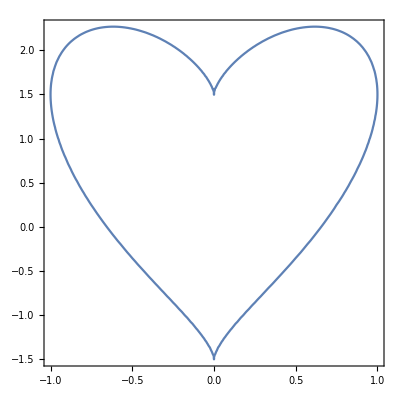

```mathematica
Block[{a=1,b=3/2},ContourPlot[-a^6 b^6+3 a^4 b^6 x^2-2 a^2 b^6 x^4+b^6 x^6-6 a^4 b^5 x^2 y+6 a^2 b^5 x^4 y+3 a^6 b^4 y^2-6 a^4 b^4 x^2 y^2+3 a^2 b^4 x^4 y^2-2 a^4 b^3 x^2 y^3-3 a^6 b^2 y^4+3 a^4 b^2 x^2 y^4+a^6 y^6==0,{x,-a,a},{y,-b,-Root[23 b^4+36 b^3 #1-54 b^2 #1^2-4 b #1^3+27 #1^4&,1]}]]
```

```mathematica
xy/.{a->1,b->1}
```

-1+3 x^2-2 x^4+x^6-6 x^2 y+6 x^4 y+3 y^2-6 x^2 y^2+3 x^4 y^2-2 x^2 y^3-3 y^4+3 x^2 y^4+y^6==0

```mathematica
FullSimplify[%]
```

x^6+(-1+y^2)^3+x^4 (-2+3 y (2+y))+x^2 (3+y (-6+y (-6+y (-2+3 y))))==0

```mathematica
x^6+(-1+y^2)^3+x^4 Factor[(-2+3 y (2+y))]+x^2 Factor[(3+y (-6+y (-6+y (-2+3 y))))]==0
```

x^6+(-1+y^2)^3+x^4 (-2+6 y+3 y^2)+x^2 (3-6 y-6 y^2-2 y^3+3 y^4)==0

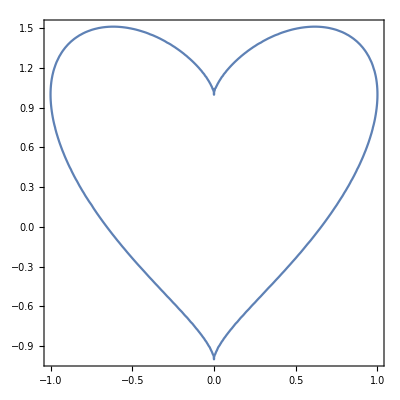

```mathematica
ContourPlot[-1+3 x^2-2 x^4+x^6-6 x^2 y+6 x^4 y+3 y^2-6 x^2 y^2+3 x^4 y^2-2 x^2 y^3-3 y^4+3 x^2 y^4+y^6==0,{x,-1,1},{y,-1,-Root[23+36 #1-54 #1^2-4 #1^3+27 #1^4&,1]}]
```

### ArcLength

```mathematica
reg=ImplicitRegion[x^2+(y-(x^2)^(1/3))^2<=1,{x,y}]
```

ImplicitRegion[x^2+(-(x^2)^(1/3)+y)^2≤1,{x,y}]

```mathematica
RegionPlot[reg]
```

-Graphics-

```mathematica
boundary=ImplicitRegion[x^2+(y-(x^2)^(1/3))^2==1,{x,y}]
```

ImplicitRegion[x^2+(-(x^2)^(1/3)+y)^2==1,{x,y}]

```mathematica
ArcLength[boundary]
```

7.68765

#### Solve for y

```mathematica
{bot,top}=y/.Solve[x^2+(y-(x^2)^(1/3))^2==1,y]
```

{(x^2)^(1/3)-√(1-x^2),(x^2)^(1/3)+√(1-x^2)}

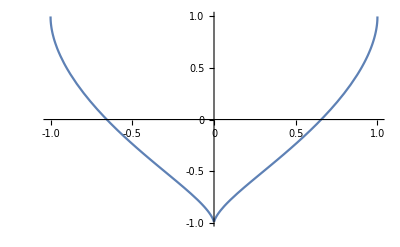
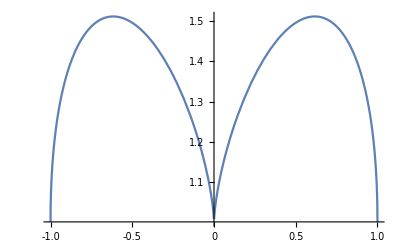
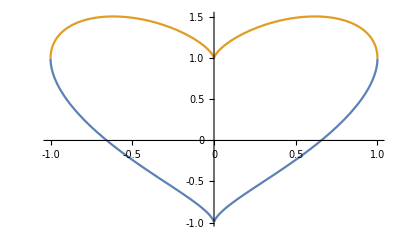

```mathematica
Plot[#,{x,-1,1}]&/@{bot,top,{bot,top}}
```

```mathematica
FullSimplify[√(D[bot,x]^2+1),0<x<1]
```

√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2)

```mathematica
FullSimplify[√(D[top,x]^2+1),0<x<1]
```

√(1+(-2/(3 x^(1/3))+x/(√(1-x^2)))^2)

```mathematica
FullSimplify[√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2)+√(1+(-2/(3 x^(1/3))+x/(√(1-x^2)))^2),0<x<1]
```

√(1+(-2/(3 x^(1/3))+x/(√(1-x^2)))^2)+√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2)

```mathematica
2(NIntegrate[√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2),{x,0,1}]+NIntegrate[√(1+(-2/(3 x^(1/3))+x/(√(1-x^2)))^2),{x,0,1}])
```

7.68765

```mathematica
(s=2(Integrate[√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2),{x,0,1}]+Integrate[√(1+(-2/(3 x^(1/3))+x/(√(1-x^2)))^2),{x,0,1}]))//Timing
```

{105.829,2 (∫_0^1 √(1+(-2/(3 x^(1/3))+x/(√(1-x^2)))^2)ⅆx+∫_0^1 √(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2)ⅆx)}

```mathematica
Integrate[√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2),x]
```

∫√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2)ⅆx

```mathematica
ResourceFunction["IntegrateAlgebraic"][√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2),x]
```

[√(1+(2/(3 x^(1/3))+x/(√(1-x^2)))^2),x]

#### Solve for x

```mathematica
{bot,top}=x/.Solve[x^2+(y-(x^2)^(1/3))^2==1,x]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Set::shape: Lists {bot,top} and {-√(2/3-2 y-y^2-(5 2^(1/3))/(3 (-11+«5»+Power[«2»])^(1/3))-(2 2^(1/3) y)/(-11+«5»+«1»)^(1/3)+(14 2^(1/3) y^2)/(-11+«5»+Power[«2»])^(1/3)+(14 2^(1/3) y^3)/(-11+Times[«2»]+«3»+Times[«2»]+Power[«2»])^(1/3)+(-11+Times[«2»]+Times[«2»]+«1»+Times[«2»]+Times[«2»]+Power[«2»])^(1/3)/(3 2^(1/3))),√(«10»+(«1»)/(«1»)^(«1»)+(«1»)^(1/3)/(3 2^(«1»))),«2»,-√(«15»+«3»),√(2/3-2 y-y^2+«10»+«3»)} are not the same shape.

{-√(2/3-2 y-y^2-(5 2^(1/3))/(3 (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))-(2 2^(1/3) y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(14 2^(1/3) y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(14 2^(1/3) y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+1/(3 2^(1/3))(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)),√(2/3-2 y-y^2-(5 2^(1/3))/(3 (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))-(2 2^(1/3) y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(14 2^(1/3) y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(14 2^(1/3) y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+1/(3 2^(1/3))(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)),-√(2/3-2 y-y^2+5/(3 2^(2/3) (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))-(5 ⅈ)/(2^(2/3) √3 (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))+(2^(1/3) y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(ⅈ 2^(1/3) √3 y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(7 ⅈ 2^(1/3) √3 y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(7 ⅈ 2^(1/3) √3 y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-1/(6 2^(1/3))(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-1/(2 2^(1/3) √3)ⅈ (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)),√(2/3-2 y-y^2+5/(3 2^(2/3) (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))-(5 ⅈ)/(2^(2/3) √3 (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))+(2^(1/3) y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(ⅈ 2^(1/3) √3 y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(7 ⅈ 2^(1/3) √3 y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(7 ⅈ 2^(1/3) √3 y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-1/(6 2^(1/3))(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-1/(2 2^(1/3) √3)ⅈ (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)),-√(2/3-2 y-y^2+5/(3 2^(2/3) (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))+(5 ⅈ)/(2^(2/3) √3 (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))+(2^(1/3) y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(ⅈ 2^(1/3) √3 y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 ⅈ 2^(1/3) √3 y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 ⅈ 2^(1/3) √3 y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-1/(6 2^(1/3))(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+1/(2 2^(1/3) √3)ⅈ (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)),√(2/3-2 y-y^2+5/(3 2^(2/3) (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))+(5 ⅈ)/(2^(2/3) √3 (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))+(2^(1/3) y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+(ⅈ 2^(1/3) √3 y)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 ⅈ 2^(1/3) √3 y^2)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 2^(1/3) y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-(7 ⅈ 2^(1/3) √3 y^3)/(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)-1/(6 2^(1/3))(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3)+1/(2 2^(1/3) √3)ⅈ (-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5+√(4 (5+6 y-42 y^2-42 y^3)^3+(-11+126 y+144 y^2-450 y^3-783 y^4-216 y^5)^2))^(1/3))}

### ArcLengthFunction

### Area

This curve:

```mathematica
reg=ImplicitRegion[x^2+(y-(x^2)^(1/3))^2<=1,{x,y}]
```

ImplicitRegion[x^2+(-(x^2)^(1/3)+y)^2≤1,{x,y}]

First heart curve:

```mathematica
reg2=ImplicitRegion[-x^2 y^3+(-1+x^2+y^2)^3<=0,{x,y}]
```

ImplicitRegion[-x^2 y^3+(-1+x^2+y^2)^3≤0,{x,y}]

```mathematica
RegionPlot/@{reg,reg2}
```

{-Graphics-,-Graphics-}

```mathematica
Area[reg]//Timing
```

{4.86341,3.14159}

```mathematica
Assuming[-1<y<1.5,Integrate[Boole[x^2+(y-(x^2)^(1/3))^2<=1],{x,-∞,∞}]]
```

Piecewise[{{2, y==1}, {-Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,1]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,2], y<Root-0.661Root[1+3 #1^2+8 #1^3&,1]-0.6610498029006993||y≥3/2||Root-0.661Root[1+3 #1^2+8 #1^3&,1]-0.6610498029006993<y<1}, {-Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,3]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,4], y==Root-0.661Root[1+3 #1^2+8 #1^3&,1]-0.6610498029006993}, {-Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,1]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,2]-Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,3]+Root[-1+3 y^2-3 y^4+y^6+(3-6 y-6 y^2-2 y^3+3 y^4) #1^2+(-2+6 y+3 y^2) #1^4+#1^6&,4], True}}]

```mathematica
Solve[x^2+(y-(x^2)^(1/3))^2==1,y]
```

{{y→(x^2)^(1/3)-√(1-x^2)},{y→(x^2)^(1/3)+√(1-x^2)}}

```mathematica
Assuming[-1<y<1.5,Integrate[Boole[x^2+(y-(x^2)^(1/3))^2<=1],{y,-∞,∞}]]
```

Piecewise[{{2, x==0}, {-Root[-1+3 x^2-2 x^4+x^6+(-6 x^2+6 x^4) #1+(3-6 x^2+3 x^4) #1^2-2 x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,1]+Root[-1+3 x^2-2 x^4+x^6+(-6 x^2+6 x^4) #1+(3-6 x^2+3 x^4) #1^2-2 x^2 #1^3+(-3+3 x^2) #1^4+#1^6&,2], -1<x<0||0<x<1}, {0, True}}]

### Curvature

```mathematica
κ=FullSimplify[Curvature[par[t],t],-π<t<π]
```

```mathematica
Plot[κ,{t,-π,π}]
```

### Cusps

```mathematica
reg=ImplicitRegion[x^2+(y-(x^2)^(1/3))^2<=1,{x,y}]
```

```mathematica
cartesian
```

-1+x^2/a^2+(-(x^2/a^2)^(1/3)+y/b)^2

```mathematica
Solve[cartesian==0/.x->0,y]
```

{{y→-b},{y→b}}

```mathematica
RegionPlot[reg,Epilog->{AbsolutePointSize[6],Point[{{0,1},{0,-1}}]}]
```

-Graphics-

### ImplicitCurvatue

```mathematica
kappa=Factor@Curvature[xy,{x,y}]
```

{(3 a^2 b^2 (9 a^12 b^14 x^2-69 a^10 b^14 x^4+193 a^8 b^14 x^6-242 a^6 b^14 x^8+169 a^4 b^14 x^10-69 a^2 b^14 x^12+9 b^14 x^14-18 a^12 b^13 x^2 y+90 a^10 b^13 x^4 y-288 a^8 b^13 x^6 y+442 a^6 b^13 x^8 y-234 a^4 b^13 x^10 y+9 a^14 b^12 y^2-90 a^12 b^12 x^2 y^2+393 a^10 b^12 x^4 y^2-1104 a^8 b^12 x^6 y^2+1395 a^6 b^12 x^8 y^2-690 a^4 b^12 x^10 y^2+63 a^2 b^12 x^12 y^2-18 a^14 b^11 y^3+258 a^12 b^11 x^2 y^3-578 a^10 b^11 x^4 y^3+604 a^8 b^11 x^6 y^3-380 a^6 b^11 x^8 y^3+114 a^4 b^11 x^10 y^3-54 a^14 b^10 y^4+165 a^12 b^10 x^2 y^4+90 a^10 b^10 x^4 y^4-168 a^8 b^10 x^6 y^4-192 a^6 b^10 x^8 y^4+189 a^4 b^10 x^10 y^4+66 a^14 b^9 y^5-756 a^12 b^9 x^2 y^5+1746 a^10 b^9 x^4 y^5-1344 a^8 b^9 x^6 y^5+450 a^6 b^9 x^8 y^5+135 a^14 b^8 y^6-524 a^12 b^8 x^2 y^6+706 a^10 b^8 x^4 y^6-380 a^8 b^8 x^6 y^6+315 a^6 b^8 x^8 y^6-84 a^14 b^7 y^7+900 a^12 b^7 x^2 y^7-1518 a^10 b^7 x^4 y^7+660 a^8 b^7 x^6 y^7-180 a^14 b^6 y^8+675 a^12 b^6 x^2 y^8-1053 a^10 b^6 x^4 y^8+315 a^8 b^6 x^6 y^8+36 a^14 b^5 y^9-474 a^12 b^5 x^2 y^9+420 a^10 b^5 x^4 y^9+135 a^14 b^4 y^10-298 a^12 b^4 x^2 y^10+189 a^10 b^4 x^4 y^10+6 a^14 b^3 y^11+90 a^12 b^3 x^2 y^11-54 a^14 b^2 y^12+63 a^12 b^2 x^2 y^12-6 a^14 b y^13+9 a^14 y^14))/(9 a^8 b^12 x^2+9 a^8 b^10 x^4-24 a^6 b^12 x^4-18 a^6 b^10 x^6+34 a^4 b^12 x^6+9 a^4 b^10 x^8-24 a^2 b^12 x^8+9 b^12 x^10-18 a^10 b^9 x^2 y-36 a^8 b^11 x^2 y+54 a^8 b^9 x^4 y+120 a^6 b^11 x^4 y-54 a^6 b^9 x^6 y-132 a^4 b^11 x^6 y+18 a^4 b^9 x^8 y+72 a^2 b^11 x^8 y+9 a^12 b^8 y^2-36 a^10 b^8 x^2 y^2+72 a^8 b^8 x^4 y^2-60 a^6 b^10 x^4 y^2-54 a^6 b^8 x^6 y^2+60 a^4 b^10 x^6 y^2+9 a^4 b^8 x^8 y^2+36 a^2 b^10 x^8 y^2+18 a^10 b^7 x^2 y^3+60 a^8 b^9 x^2 y^3-36 a^8 b^7 x^4 y^3-200 a^6 b^9 x^4 y^3+18 a^6 b^7 x^6 y^3+132 a^4 b^9 x^6 y^3-36 a^12 b^6 y^4+108 a^10 b^6 x^2 y^4+78 a^8 b^8 x^2 y^4-99 a^8 b^6 x^4 y^4-144 a^6 b^8 x^4 y^4+36 a^6 b^6 x^6 y^4+54 a^4 b^8 x^6 y^4+18 a^10 b^5 x^2 y^5-12 a^8 b^7 x^2 y^5-18 a^8 b^5 x^4 y^5+48 a^6 b^7 x^4 y^5+54 a^12 b^4 y^6-108 a^10 b^4 x^2 y^6-32 a^8 b^6 x^2 y^6+54 a^8 b^4 x^4 y^6+36 a^6 b^6 x^4 y^6-18 a^10 b^3 x^2 y^7-12 a^8 b^5 x^2 y^7-36 a^12 b^2 y^8+36 a^10 b^2 x^2 y^8+9 a^8 b^4 x^2 y^8+9 a^12 y^10)^(3/2),(3 a^4 b^11 x^2 (64 a^10 b^5-68 a^8 b^5 x^2-182 a^6 b^5 x^4+5 a^4 b^5 x^6+2 a^2 b^5 x^8-64 b^5 x^10+394 a^8 b^4 x^2 y+276 a^6 b^4 x^4 y-276 a^4 b^4 x^6 y-394 a^2 b^4 x^8 y-192 a^10 b^3 y^2+120 a^8 b^3 x^2 y^2+126 a^6 b^3 x^4 y^2+138 a^4 b^3 x^6 y^2-192 a^2 b^3 x^8 y^2+228 a^8 b^2 x^2 y^3+30 a^6 b^2 x^4 y^3+228 a^4 b^2 x^6 y^3+128 a^10 b y^4+588 a^8 b x^2 y^4-588 a^6 b x^4 y^4-128 a^4 b x^6 y^4+18 a^8 x^2 y^5-18 a^6 x^4 y^5))/(-a^6 b (5 a^4 b^11-9 a^4 b^9 x^2-18 a^2 b^11 x^2+18 a^2 b^9 x^4+7 b^11 x^4+72 a^6 b^8 y+6 a^4 b^10 y-216 a^4 b^8 x^2 y+30 a^2 b^10 x^2 y+90 a^2 b^8 x^4 y-48 b^10 x^4 y+162 a^6 b^7 y^2-57 a^4 b^9 y^2-27 a^4 b^7 x^2 y^2+165 a^2 b^9 x^2 y^2-297 a^2 b^7 x^4 y^2-93 b^9 x^4 y^2-126 a^6 b^6 y^3-60 a^4 b^8 y^3+1224 a^4 b^6 x^2 y^3-86 a^2 b^8 x^2 y^3-1206 a^2 b^6 x^4 y^3+200 b^8 x^4 y^3-486 a^6 b^5 y^4+141 a^4 b^7 y^4+1629 a^4 b^5 x^2 y^4-540 a^2 b^7 x^2 y^4-1035 a^2 b^5 x^4 y^4+387 b^7 x^4 y^4-54 a^6 b^4 y^5+144 a^4 b^6 y^5+540 a^4 b^4 x^2 y^5-396 a^2 b^6 x^2 y^5-162 a^2 b^4 x^4 y^5+114 b^6 x^4 y^5+486 a^6 b^3 y^6-131 a^4 b^5 y^6-297 a^4 b^3 x^2 y^6+41 a^2 b^5 x^2 y^6+198 a^6 b^2 y^7-132 a^4 b^4 y^7-252 a^4 b^2 x^2 y^7+156 a^2 b^4 x^2 y^7-162 a^6 b y^8+42 a^4 b^3 y^8-90 a^6 y^9+42 a^4 b^2 y^9))^(3/2),(3 a^12 b^4 (22 a^4 b^12-57 a^2 b^12 x^2+15 b^12 x^4+32 a^4 b^11 y+112 a^2 b^11 x^2 y-242 b^11 x^4 y-471 a^4 b^10 y^2+1704 a^2 b^10 x^2 y^2-1020 b^10 x^4 y^2-1498 a^4 b^9 y^3+1914 a^2 b^9 x^2 y^3+896 b^9 x^4 y^3-369 a^4 b^8 y^4-6443 a^2 b^8 x^2 y^4+8594 b^8 x^4 y^4+3540 a^4 b^7 y^5-17094 a^2 b^7 x^2 y^5+13890 b^7 x^4 y^5+3585 a^4 b^6 y^6-15238 a^2 b^6 x^2 y^6+9460 b^6 x^4 y^6-1952 a^4 b^5 y^7-4120 a^2 b^5 x^2 y^7+2802 b^5 x^4 y^7-4161 a^4 b^4 y^8+2658 a^2 b^4 x^2 y^8+192 b^4 x^4 y^8-884 a^4 b^3 y^9+1900 a^2 b^3 x^2 y^9+1266 a^4 b^2 y^10+320 a^2 b^2 x^2 y^10+762 a^4 b y^11+128 a^4 y^12))/(-a^6 b (5 a^4 b^11-9 a^4 b^9 x^2-18 a^2 b^11 x^2+18 a^2 b^9 x^4+7 b^11 x^4+72 a^6 b^8 y+6 a^4 b^10 y-216 a^4 b^8 x^2 y+30 a^2 b^10 x^2 y+90 a^2 b^8 x^4 y-48 b^10 x^4 y+162 a^6 b^7 y^2-57 a^4 b^9 y^2-27 a^4 b^7 x^2 y^2+165 a^2 b^9 x^2 y^2-297 a^2 b^7 x^4 y^2-93 b^9 x^4 y^2-126 a^6 b^6 y^3-60 a^4 b^8 y^3+1224 a^4 b^6 x^2 y^3-86 a^2 b^8 x^2 y^3-1206 a^2 b^6 x^4 y^3+200 b^8 x^4 y^3-486 a^6 b^5 y^4+141 a^4 b^7 y^4+1629 a^4 b^5 x^2 y^4-540 a^2 b^7 x^2 y^4-1035 a^2 b^5 x^4 y^4+387 b^7 x^4 y^4-54 a^6 b^4 y^5+144 a^4 b^6 y^5+540 a^4 b^4 x^2 y^5-396 a^2 b^6 x^2 y^5-162 a^2 b^4 x^4 y^5+114 b^6 x^4 y^5+486 a^6 b^3 y^6-131 a^4 b^5 y^6-297 a^4 b^3 x^2 y^6+41 a^2 b^5 x^2 y^6+198 a^6 b^2 y^7-132 a^4 b^4 y^7-252 a^4 b^2 x^2 y^7+156 a^2 b^4 x^2 y^7-162 a^6 b y^8+42 a^4 b^3 y^8-90 a^6 y^9+42 a^4 b^2 y^9))^(3/2)}

```mathematica
ByteCount/@kappa
```

{40784,23984,26600}

```mathematica
kappa[[-1]]
```

(3 a^12 b^4 (22 a^4 b^12-57 a^2 b^12 x^2+15 b^12 x^4+32 a^4 b^11 y+112 a^2 b^11 x^2 y-242 b^11 x^4 y-471 a^4 b^10 y^2+1704 a^2 b^10 x^2 y^2-1020 b^10 x^4 y^2-1498 a^4 b^9 y^3+1914 a^2 b^9 x^2 y^3+896 b^9 x^4 y^3-369 a^4 b^8 y^4-6443 a^2 b^8 x^2 y^4+8594 b^8 x^4 y^4+3540 a^4 b^7 y^5-17094 a^2 b^7 x^2 y^5+13890 b^7 x^4 y^5+3585 a^4 b^6 y^6-15238 a^2 b^6 x^2 y^6+9460 b^6 x^4 y^6-1952 a^4 b^5 y^7-4120 a^2 b^5 x^2 y^7+2802 b^5 x^4 y^7-4161 a^4 b^4 y^8+2658 a^2 b^4 x^2 y^8+192 b^4 x^4 y^8-884 a^4 b^3 y^9+1900 a^2 b^3 x^2 y^9+1266 a^4 b^2 y^10+320 a^2 b^2 x^2 y^10+762 a^4 b y^11+128 a^4 y^12))/(-a^6 b (5 a^4 b^11-9 a^4 b^9 x^2-18 a^2 b^11 x^2+18 a^2 b^9 x^4+7 b^11 x^4+72 a^6 b^8 y+6 a^4 b^10 y-216 a^4 b^8 x^2 y+30 a^2 b^10 x^2 y+90 a^2 b^8 x^4 y-48 b^10 x^4 y+162 a^6 b^7 y^2-57 a^4 b^9 y^2-27 a^4 b^7 x^2 y^2+165 a^2 b^9 x^2 y^2-297 a^2 b^7 x^4 y^2-93 b^9 x^4 y^2-126 a^6 b^6 y^3-60 a^4 b^8 y^3+1224 a^4 b^6 x^2 y^3-86 a^2 b^8 x^2 y^3-1206 a^2 b^6 x^4 y^3+200 b^8 x^4 y^3-486 a^6 b^5 y^4+141 a^4 b^7 y^4+1629 a^4 b^5 x^2 y^4-540 a^2 b^7 x^2 y^4-1035 a^2 b^5 x^4 y^4+387 b^7 x^4 y^4-54 a^6 b^4 y^5+144 a^4 b^6 y^5+540 a^4 b^4 x^2 y^5-396 a^2 b^6 x^2 y^5-162 a^2 b^4 x^4 y^5+114 b^6 x^4 y^5+486 a^6 b^3 y^6-131 a^4 b^5 y^6-297 a^4 b^3 x^2 y^6+41 a^2 b^5 x^2 y^6+198 a^6 b^2 y^7-132 a^4 b^4 y^7-252 a^4 b^2 x^2 y^7+156 a^2 b^4 x^2 y^7-162 a^6 b y^8+42 a^4 b^3 y^8-90 a^6 y^9+42 a^4 b^2 y^9))^(3/2)

```mathematica
curv=kappa[[-1]]/.{a->1,b->1}
```

(3 (22-57 x^2+15 x^4+32 y+112 x^2 y-242 x^4 y-471 y^2+1704 x^2 y^2-1020 x^4 y^2-1498 y^3+1914 x^2 y^3+896 x^4 y^3-369 y^4-6443 x^2 y^4+8594 x^4 y^4+3540 y^5-17094 x^2 y^5+13890 x^4 y^5+3585 y^6-15238 x^2 y^6+9460 x^4 y^6-1952 y^7-4120 x^2 y^7+2802 x^4 y^7-4161 y^8+2658 x^2 y^8+192 x^4 y^8-884 y^9+1900 x^2 y^9+1266 y^10+320 x^2 y^10+762 y^11+128 y^12))/(-5+27 x^2-25 x^4-78 y+186 x^2 y-42 x^4 y-105 y^2-138 x^2 y^2+390 x^4 y^2+186 y^3-1138 x^2 y^3+1006 x^4 y^3+345 y^4-1089 x^2 y^4+648 x^4 y^4-90 y^5-144 x^2 y^5+48 x^4 y^5-355 y^6+256 x^2 y^6-66 y^7+96 x^2 y^7+120 y^8+48 y^9)^(3/2)

### ImplicitSlope

```mathematica
slope1=FullSimplify[Slope[cartesian,{x,y}],a>0&&b>0]
```

{(b x (b (x^2/a^2)^(1/3) (2+3 (x^2/a^2)^(1/3))-2 y))/(3 b x^2-3 (a x^2)^(2/3) y),(b x (b (x^2/a^2)^(1/3) (2+3 (x^2/a^2)^(1/3))-2 y))/(3 b x^2-3 (a x^2)^(2/3) y)}

```mathematica
Equal@@%
```

True

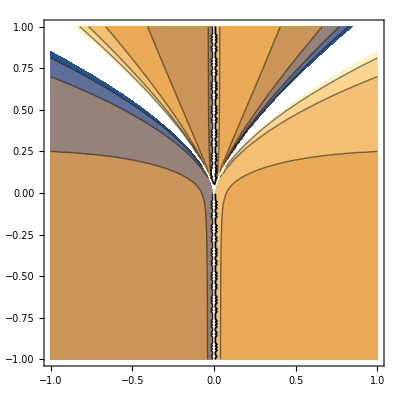

```mathematica
Block[{a=1,b=1},ContourPlot[(b x (b (x^2/a^2)^(1/3) (2+3 (x^2/a^2)^(1/3))-2 y))/(3 b x^2-3 (a x^2)^(2/3) y),{x,-1,1},{y,-1,1}]]
```

```mathematica
slope2=Slope[xy,{x,y}]//Factor
```

{-(b^2 x (3 a^4 b^4-4 a^2 b^4 x^2+3 b^4 x^4-6 a^4 b^3 y+12 a^2 b^3 x^2 y-6 a^4 b^2 y^2+6 a^2 b^2 x^2 y^2-2 a^4 b y^3+3 a^4 y^4))/(3 a^2 (-a^2 b^5 x^2+b^5 x^4+a^4 b^4 y-2 a^2 b^4 x^2 y+b^4 x^4 y-a^2 b^3 x^2 y^2-2 a^4 b^2 y^3+2 a^2 b^2 x^2 y^3+a^4 y^5)),-(b^2 x (3 a^4 b^4-4 a^2 b^4 x^2+3 b^4 x^4-6 a^4 b^3 y+12 a^2 b^3 x^2 y-6 a^4 b^2 y^2+6 a^2 b^2 x^2 y^2-2 a^4 b y^3+3 a^4 y^4))/(3 a^2 (-a^2 b^5 x^2+b^5 x^4+a^4 b^4 y-2 a^2 b^4 x^2 y+b^4 x^4 y-a^2 b^3 x^2 y^2-2 a^4 b^2 y^3+2 a^2 b^2 x^2 y^3+a^4 y^5))}

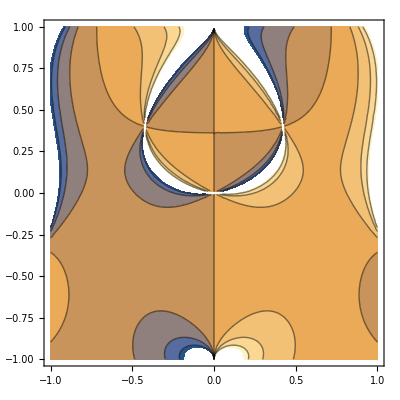

```mathematica
Block[{a=1,b=1},ContourPlot[-(b^2 x (3 a^4 b^4-4 a^2 b^4 x^2+3 b^4 x^4-6 a^4 b^3 y+12 a^2 b^3 x^2 y-6 a^4 b^2 y^2+6 a^2 b^2 x^2 y^2-2 a^4 b y^3+3 a^4 y^4))/(3 a^2 (-a^2 b^5 x^2+b^5 x^4+a^4 b^4 y-2 a^2 b^4 x^2 y+b^4 x^4 y-a^2 b^3 x^2 y^2-2 a^4 b^2 y^3+2 a^2 b^2 x^2 y^3+a^4 y^5)),{x,-1,1},{y,-1,1}]]
```

### InflectionPoints

```mathematica
kappa=Simplify[Curvature[cartesian,{x,y}],a>0&&b>0]
```

Power::infy: Infinite expression 1/0^(3/2) encountered.

{(3 (b^3 (9 x^4+9 a^(2/3) (x^2)^(5/3)-2 (a x^2)^(4/3))+6 a b^2 x^2 (a-3 (a x^2)^(1/3)) y+3 a^2 b (3 x^2-2 (a x^2)^(2/3)) y^2+2 a^(10/3) (x^2)^(1/3) y^3))/(b √((3 (3 x^2+4 (a x^2)^(2/3)))/a^4+(4 (a x^2)^(1/3) (b-3 y))/(a^3 b)-(8 y)/(a^2 b)-(18 (x^2)^(1/3) y)/(a^(2/3) b^3)+(9 y^2)/b^4+(9 x^2+4 y^2)/(a^(4/3) b^2 (x^2)^(1/3))) (b^4 (9 x^4+12 a^(2/3) (x^2)^(5/3)+4 (a x^2)^(4/3))-18 a^(10/3) b (x^2)^(4/3) y-4 a b^3 x^2 (2 a+3 (a x^2)^(1/3)) y+9 a^4 x^2 y^2+a^(8/3) b^2 (x^2)^(2/3) (9 x^2+4 y^2))),(3 (-2 a^(4/3) b (x^2)^(1/3)+(2 b (x^2)^(4/3))/a^(2/3)+9 b (a x^2)^(2/3)+2 a^2 y-2 x^2 y))/(a^(8/3) b^3 (x^2)^(2/3) ((3 (3 x^2+4 (a x^2)^(2/3)))/a^4+(4 (a x^2)^(1/3) (b-3 y))/(a^3 b)-(8 y)/(a^2 b)-(18 (x^2)^(1/3) y)/(a^(2/3) b^3)+(9 y^2)/b^4+(9 x^2+4 y^2)/(a^(4/3) b^2 (x^2)^(1/3)))^(3/2)),(3 ((9 b^3 (x^2)^(4/3))/a^(2/3)+(9 b^3 (x^2)^(5/3))/a^(4/3)-6 a^(4/3) b (x^2)^(1/3) y^2+2 a^2 y^3+3 b (a x^2)^(2/3) y (2 b+3 y)-2 b^2 x^2 (b+9 y)))/(a^(8/3) b^5 (x^2)^(2/3) ((3 (3 x^2+4 (a x^2)^(2/3)))/a^4+(4 (a x^2)^(1/3) (b-3 y))/(a^3 b)-(8 y)/(a^2 b)-(18 (x^2)^(1/3) y)/(a^(2/3) b^3)+(9 y^2)/b^4+(9 x^2+4 y^2)/(a^(4/3) b^2 (x^2)^(1/3)))^(3/2))}

#### Arbitrary a, b

```mathematica
eqns=Expand@PowerExpand[{cartesian,3 (-2 a^(4/3) b (x^2)^(1/3)+(2 b (x^2)^(4/3))/a^(2/3)+9 b (a x^2)^(2/3)+2 a^2 y-2 x^2 y)==0}]//FullSimplify
```

{x^(4/3)/a^(4/3)+x^2/a^2-(2 x^(2/3) y)/(a^(2/3) b)+y^2/b^2==1,(b x^(2/3) (-2 a^2+9 a^(4/3) x^(2/3)+2 x^2))/a^(2/3)+2 (a-x) (a+x) y==0}

```mathematica
Solve[{xy,-(3 a^12 b^4 (88 a^4 b^12+237 a^2 b^12 x^2-121 b^12 x^4+248 a^4 b^11 y+328 a^2 b^11 x^2 y+350 b^11 x^4 y-177 a^4 b^10 y^2-3048 a^2 b^10 x^2 y^2+2484 b^10 x^4 y^2-622 a^4 b^9 y^3-3166 a^2 b^9 x^2 y^3-164 b^9 x^4 y^3-3129 a^4 b^8 y^4+6365 a^2 b^8 x^2 y^4-8594 b^8 x^4 y^4-5736 a^4 b^7 y^5+18030 a^2 b^7 x^2 y^5-13890 b^7 x^4 y^5-3775 a^4 b^6 y^6+15238 a^2 b^6 x^2 y^6-9460 b^6 x^4 y^6+2156 a^4 b^5 y^7+4120 a^2 b^5 x^2 y^7-2802 b^5 x^4 y^7+4161 a^4 b^4 y^8-2658 a^2 b^4 x^2 y^8-192 b^4 x^4 y^8+884 a^4 b^3 y^9-1900 a^2 b^3 x^2 y^9-1266 a^4 b^2 y^10-320 a^2 b^2 x^2 y^10-762 a^4 b y^11-128 a^4 y^12))==0},{x,y},Reals]
```

$Aborted

```mathematica
FindInstance[eqns,{x,y}]
```

FindInstance::exvar: The system contains a nonconstant expression a independent of variables {x,y}.

FindInstance[{x^(4/3)/a^(4/3)+x^2/a^2-(2 x^(2/3) y)/(a^(2/3) b)+y^2/b^2==1,(b x^(2/3) (-2 a^2+9 a^(4/3) x^(2/3)+2 x^2))/a^(2/3)+2 (a-x) (a+x) y==0},{x,y}]

```mathematica
Solve[x^(4/3)/a^(4/3)+x^2/a^2-(2 x^(2/3) y)/(a^(2/3) b)+y^2/b^2==1,y]
```

{{y→(b x^(2/3))/a^(2/3)-(b √(a^2-x^2))/a},{y→(b x^(2/3))/a^(2/3)+(b √(a^2-x^2))/a}}

```mathematica
FullSimplify[(b x^(2/3) (-2 a^2+9 a^(4/3) x^(2/3)+2 x^2))/a^(2/3)+2 (a-x) (a+x) y==0/.y->(b x^(2/3))/a^(2/3)-(b √(a^2-x^2))/a]
```

9 a^(2/3) b x^(4/3)+(2 b x^2 √(a^2-x^2))/a==2 a b √(a^2-x^2)

```mathematica
Assuming[a>0&&b>0,Solve[(9 a^(2/3) b x^(4/3))/(√(a^2-x^2))+(2 b x^2)/a==2 a b ,x,Reals]]
```

{{x→Root[-64 a^18+576 a^16 #1^2-2304 a^14 #1^4+5376 a^12 #1^6+523377 a^10 #1^8+8064 a^8 #1^10-5376 a^6 #1^12+2304 a^4 #1^14-576 a^2 #1^16+64 #1^18&,2]}}

```mathematica
With[{a=1,b=1},Root[-64 a^18+576 a^16 #1^2-2304 a^14 #1^4+5376 a^12 #1^6+523377 a^10 #1^8+8064 a^8 #1^10-5376 a^6 #1^12+2304 a^4 #1^14-576 a^2 #1^16+64 #1^18&,2]]
```

Root0.293Root[-64+576 #1^2-2304 #1^4+5376 #1^6+523377 #1^8+8064 #1^10-5376 #1^12+2304 #1^14-576 #1^16+64 #1^18&,2]0.29264822355669645

```mathematica
(b x^(2/3))/a^(2/3)-(b √(a^2-x^2))/a/.x->Root[-64 a^18+576 a^16 #1^2-2304 a^14 #1^4+5376 a^12 #1^6+523377 a^10 #1^8+8064 a^8 #1^10-5376 a^6 #1^12+2304 a^4 #1^14-576 a^2 #1^16+64 #1^18&,2]//FullSimplify
```

1/a b (a^(1/3) Root[-64 a^18+576 a^16 #1^2-2304 a^14 #1^4+5376 a^12 #1^6+523377 a^10 #1^8+8064 a^8 #1^10-5376 a^6 #1^12+2304 a^4 #1^14-576 a^2 #1^16+64 #1^18&,2]^(2/3)-√(a^2-Root[-64 a^18+576 a^16 #1^2-2304 a^14 #1^4+5376 a^12 #1^6+523377 a^10 #1^8+8064 a^8 #1^10-5376 a^6 #1^12+2304 a^4 #1^14-576 a^2 #1^16+64 #1^18&,2]^2))

```mathematica
RegionPlot[reg,Epilog->{AbsolutePointSize[6],Point[{(Root"0.441"Root[-4+12 #1^3+81 #1^4-12 #1^6+4 #1^9&,3]0.4407888444494923)^(3/2),Root"-0.515"Root[883+1602 #1-1134 #1^2-1596 #1^3+927 #1^4+1134 #1^5-24 #1^6-180 #1^7+8 #1^9&,3]-0.5154313275031338}]}]
```

#### a==1, b==1

```mathematica
x/.Solve[(9 a^(2/3) b x^(4/3))/(√(a^2-x^2))+(2 b x^2)/a==2 a b /.{a->1,b->1},x,Reals]//RootReduce
```

{Root0.293Root[-64+576 #1^2-2304 #1^4+5376 #1^6+523377 #1^8+8064 #1^10-5376 #1^12+2304 #1^14-576 #1^16+64 #1^18&,2]0.29264822355669645}

```mathematica
(b x^(2/3))/a^(2/3)-(b √(a^2-x^2))/a/.{a->1,b->1,x->(Root"0.441"Root[-4+12 #1^3+81 #1^4-12 #1^6+4 #1^9&,3]0.4407888444494923)^(3/2)}//RootReduce
```

Root-0.515Root[883+1602 #1-1134 #1^2-1596 #1^3+927 #1^4+1134 #1^5-24 #1^6-180 #1^7+8 #1^9&,3]-0.5154313275031338

```mathematica
RegionPlot[reg,Epilog->{AbsolutePointSize[6],Point[{(Root"0.441"Root[-4+12 #1^3+81 #1^4-12 #1^6+4 #1^9&,3]0.4407888444494923)^(3/2),Root"-0.515"Root[883+1602 #1-1134 #1^2-1596 #1^3+927 #1^4+1134 #1^5-24 #1^6-180 #1^7+8 #1^9&,3]-0.5154313275031338}]}]
```

-Graphics-

### NormalVector

```mathematica
Assuming[assum,FullSimplify[NormalVector[parm,t]/.xform]]
```

### ParametricEquations

#### Solve for y

```mathematica
{bot,top}=y/.Solve[x^2+(y-(x^2)^(1/3))^2==1,y]
```

{(x^2)^(1/3)-√(1-x^2),(x^2)^(1/3)+√(1-x^2)}

```mathematica
Plot[#,{x,-1,1}]&/@{bot,top,{bot,top}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{bot,top}=Simplify[y/.Solve[cartesian,y],a>0&&b>0]
```

{(b ((a x^2)^(1/3)-√(a^2-x^2)))/a,(b ((a x^2)^(1/3)+√(a^2-x^2)))/a}

```mathematica
Block[{a=1,b=1},ParametricPlot[{x,(b ((a x^2)^(1/3)-#√(a^2-x^2)))/a},{x,-1,1}]&/@{-1,1}]
```

{-Graphics-,-Graphics-}

```mathematica
Show[%,PlotRange->Full]
```

-Graphics-

#### Solve for x

```mathematica
Assuming[a>0&&b>0,Simplify@Solve[cartesian,x,Reals]]
```

{{x→ConditionalExpression[-√Root[-a^6 b^6+3 a^6 b^4 y^2-3 a^6 b^2 y^4+a^6 y^6+(3 a^4 b^6-6 a^4 b^5 y-6 a^4 b^4 y^2-2 a^4 b^3 y^3+3 a^4 b^2 y^4) #1+(-2 a^2 b^6+6 a^2 b^5 y+3 a^2 b^4 y^2) #1^2+b^6 #1^3&,1], ]},{x→ConditionalExpression[√Root[-a^6 b^6+3 a^6 b^4 y^2-3 a^6 b^2 y^4+a^6 y^6+(3 a^4 b^6-6 a^4 b^5 y-6 a^4 b^4 y^2-2 a^4 b^3 y^3+3 a^4 b^2 y^4) #1+(-2 a^2 b^6+6 a^2 b^5 y+3 a^2 b^4 y^2) #1^2+b^6 #1^3&,1], ]},{x→ConditionalExpression[-√Root[-a^6 b^6+3 a^6 b^4 y^2-3 a^6 b^2 y^4+a^6 y^6+(3 a^4 b^6-6 a^4 b^5 y-6 a^4 b^4 y^2-2 a^4 b^3 y^3+3 a^4 b^2 y^4) #1+(-2 a^2 b^6+6 a^2 b^5 y+3 a^2 b^4 y^2) #1^2+b^6 #1^3&,2], ]},{x→ConditionalExpression[√Root[-a^6 b^6+3 a^6 b^4 y^2-3 a^6 b^2 y^4+a^6 y^6+(3 a^4 b^6-6 a^4 b^5 y-6 a^4 b^4 y^2-2 a^4 b^3 y^3+3 a^4 b^2 y^4) #1+(-2 a^2 b^6+6 a^2 b^5 y+3 a^2 b^4 y^2) #1^2+b^6 #1^3&,2], ]},{x→ConditionalExpression[-√Root[-a^6 b^6+3 a^6 b^4 y^2-3 a^6 b^2 y^4+a^6 y^6+(3 a^4 b^6-6 a^4 b^5 y-6 a^4 b^4 y^2-2 a^4 b^3 y^3+3 a^4 b^2 y^4) #1+(-2 a^2 b^6+6 a^2 b^5 y+3 a^2 b^4 y^2) #1^2+b^6 #1^3&,3], ]},{x→ConditionalExpression[√Root[-a^6 b^6+3 a^6 b^4 y^2-3 a^6 b^2 y^4+a^6 y^6+(3 a^4 b^6-6 a^4 b^5 y-6 a^4 b^4 y^2-2 a^4 b^3 y^3+3 a^4 b^2 y^4) #1+(-2 a^2 b^6+6 a^2 b^5 y+3 a^2 b^4 y^2) #1^2+b^6 #1^3&,3], ]}}

#### Polar

```mathematica
FullSimplify[x^2+(y-(x^2)^(1/3))^2==1/.{x->r Cos[t],y->r Sin[t]},r>0]
```

r^2 Cos[t]^2+((r^2 Cos[t]^2)^(1/3)-r Sin[t])^2==1

```mathematica
reqn=FullSimplify[r/.Solve[%,r]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{Root[-8+24 #1^2-48 Cos[t]^2 Sin[t] #1^3+(-21+4 Cos[2 t]+Cos[4 t]) #1^4+16 Cos[t]^2 Sin[3 t] #1^5+8 #1^6&,1],Root[-8+24 #1^2-48 Cos[t]^2 Sin[t] #1^3+(-21+4 Cos[2 t]+Cos[4 t]) #1^4+16 Cos[t]^2 Sin[3 t] #1^5+8 #1^6&,2],Root[-8+24 #1^2-48 Cos[t]^2 Sin[t] #1^3+(-21+4 Cos[2 t]+Cos[4 t]) #1^4+16 Cos[t]^2 Sin[3 t] #1^5+8 #1^6&,3],Root[-8+24 #1^2-48 Cos[t]^2 Sin[t] #1^3+(-21+4 Cos[2 t]+Cos[4 t]) #1^4+16 Cos[t]^2 Sin[3 t] #1^5+8 #1^6&,4],Root[-8+24 #1^2-48 Cos[t]^2 Sin[t] #1^3+(-21+4 Cos[2 t]+Cos[4 t]) #1^4+16 Cos[t]^2 Sin[3 t] #1^5+8 #1^6&,5],Root[-8+24 #1^2-48 Cos[t]^2 Sin[t] #1^3+(-21+4 Cos[2 t]+Cos[4 t]) #1^4+16 Cos[t]^2 Sin[3 t] #1^5+8 #1^6&,6]}

```mathematica
Plot[#,{t,0,2π}]&/@reqn
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PolarPlot[reqn[[2]],{t,0,2π},AspectRatio->Automatic,PlotStyle->Red]
```

-Graphics-

### Plot

```mathematica
ContourPlot[x^2+(y-(x^2)^(1/3))^2==1,{x,-1,1},{y,-1,1.6},AspectRatio->#,ContourStyle->Red]&/@{Automatic,1}
```

{-Graphics-,-Graphics-}

```mathematica
ContourPlot[x^2+(y-(x^2)^(1/3))^2==1,{x,-1,1},{y,-1,1.6},AspectRatio->1,ContourStyle->Red]
```

-Graphics-

### Region

```mathematica
reg=ImplicitRegion[x^2+(y-(x^2)^(1/3))^2<=1,{x,y}]
```

ImplicitRegion[x^2+(-(x^2)^(1/3)+y)^2≤1,{x,y}]

```mathematica
RegionPlot[reg]
```

-Graphics-

### Singular Points

### Slope

### SpecialAffineCurvature

### TangentialAngle

```mathematica
TangentialAngle[par[t],t]
```

### TangentVector

```mathematica
Assuming[assum,FullSimplify[TangentVector[parm,t]/.xform]]
```

### VectorLength

```mathematica
Assuming[assum,FullSimplify[Norm[parm]/.xform]]
```

## Bonne Projection

```mathematica
Show[Graphics[ProjectionPlot[Projection[Bonne[85.Degree,0.]]]],AspectRatio->Automatic,ImageSize->200]
```

⁃Graphics⁃